The code in this file was used to derive and/or confirm the results reported in the article "Asexual but not clonal: evolutionary processes in populations with automictic reproduction”.

Author: Jan Engelstädter, The University of Queensland, School of Biological Sciences, Brisbane, QLD 4072, Australia
j.engelstaedter@uq.edu.au

# Definitions

It is best to run this entire section before running any cells in the Results section.

## Helper functions & variables

### Labels of genotypes

```mathematica
diploidGenotypes={"aabb","aaBb","aaBB","Aabb","AaBb","AabB","AaBB","AAbb","AABb","AABB"};
```

```mathematica
metaphaseGenotypes={"aaaabbbb","aaaaBBBB","AAAAbbbb","AAAABBBB","aaaaBBbb","aaaaBbBb","AAAABBbb","AAAABbBb","AAaabbbb","AaAabbbb","AAaaBBBB","AaAaBBBB","AAaaBBbb","AAaabbBB","AAaaBbBb","AaAaBBbb","AaAaBbBb","AaAaBbbB","AaAabBbB"};
```

```mathematica
gameteGenotypes={"ab","aB","Ab","AB"};
```

### Styles

```mathematica
genotypeColours=Table[RGBColor[0.5*StringCount[diploidGenotypes⟦i⟧,"A"],0,0.5*StringCount[diploidGenotypes⟦i⟧,"B"]],{i,10}];
```

### Converting mean crossover numbers to recombination rates and back

```mathematica
convertMToC[nmean_]:=(1-Exp[-nmean])/2;
convertCToM[r_]:=-Log[1-2r];
```

## Defining the model

### Step 1: Mutation

```mathematica
MutationStep[p_,muA_,muB_]:=p.({{(1-muA)^2, 0, 0, 2muA(1-muA), 0, 0, 0, muA^2, 0, 0}, {0, (1-muA)^2, 0, 0, muA(1-muA), muA(1-muA), 0, 0, muA^2, 0}, {0, 0, (1-muA)^2, 0, 0, 0, 2muA(1-muA), 0, 0, muA^2}, {muA(1-muA), 0, 0, (1-muA)^2+muA^2, 0, 0, 0, muA(1-muA), 0, 0}, {0, muA(1-muA), 0, 0, (1-muA)^2, muA^2, 0, 0, muA(1-muA), 0}, {0, muA(1-muA), 0, 0, muA^2, (1-muA)^2, 0, 0, muA(1-muA), 0}, {0, 0, muA(1-muA), 0, 0, 0, (1-muA)^2+muA^2, 0, 0, muA(1-muA)}, {muA^2, 0, 0, 2muA(1-muA), 0, 0, 0, (1-muA)^2, 0, 0}, {0, muA^2, 0, 0, muA(1-muA), muA(1-muA), 0, 0, (1-muA)^2, 0}, {0, 0, muA^2, 0, 0, 0, 2muA(1-muA), 0, 0, (1-muA)^2}}).({{(1-muB)^2, 2muB(1-muB), muB^2, 0, 0, 0, 0, 0, 0, 0}, {muB(1-muB), (1-muB)^2+muB^2, muB(1-muB), 0, 0, 0, 0, 0, 0, 0}, {muB^2, 2muB(1-muB), (1-muB)^2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, (1-muB)^2, muB(1-muB), muB(1-muB), muB^2, 0, 0, 0}, {0, 0, 0, muB(1-muB), (1-muB)^2, muB^2, muB(1-muB), 0, 0, 0}, {0, 0, 0, muB(1-muB), muB^2, (1-muB)^2, muB(1-muB), 0, 0, 0}, {0, 0, 0, muB^2, muB(1-muB), muB(1-muB), (1-muB)^2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (1-muB)^2, 2muB(1-muB), muB^2}, {0, 0, 0, 0, 0, 0, 0, muB(1-muB), (1-muB)^2+muB^2, muB(1-muB)}, {0, 0, 0, 0, 0, 0, 0, muB^2, 2muB(1-muB), (1-muB)^2}});
```

### Step 2: Recombination

Helper function:

```mathematica
f[n_]:=1/3(1-(-1/2)^n);
```

The following function returns the proportions of recombinant genotypes following n crossovers between centromere and locus A and m crossovers between loci A and B in Prophase I. The recombinants are expressed using placeholders A1, A2, B1 and B2 that can stand for any of the respective alleles.

```mathematica
pHs={"A1A1A2A2B1B1B2B2","A1A1A2A2B2B2B1B1","A1A1A2A2B1B2B1B2","A1A2A1A2B1B1B2B2","A1A2A1A2B1B2B1B2","A1A2A1A2B1B2B2B1","A1A2A1A2B2B1B2B1"};

PHRecMatrix[n_,m_]:=If[m>0,({{(1/2-f[m]) (1-2 f[n]), (1/2-f[m]) (1-2 f[n]), 2 f[m] (1-2 f[n]), 2 f[m] f[n], (1-2 f[m]) f[n], 2 f[m] f[n], (1-2 f[m]) f[n]}, {(1/2-f[m]) (1-2 f[n]), (1/2-f[m]) (1-2 f[n]), 2 f[m] (1-2 f[n]), 2 f[m] f[n], (1-2 f[m]) f[n], 2 f[m] f[n], (1-2 f[m]) f[n]}, {1/2 f[m] (1-2 f[n]), 1/2 f[m] (1-2 f[n]), (1-f[m]) (1-2 f[n]), (1-f[m]) f[n], f[m] f[n], (1-f[m]) f[n], f[m] f[n]}, {(f[m] f[n])/2, (f[m] f[n])/2, (1-f[m]) f[n], 1/2((1-f[m]) (1-f[n])+1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n]), 1/2((1-f[m]) (1-f[n])-1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n])}, {(1/2-f[m]) f[n], (1/2-f[m]) f[n], 2 f[m] f[n], f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n]), f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n])}, {(f[m] f[n])/2, (f[m] f[n])/2, (1-f[m]) f[n], 1/2((1-f[m]) (1-f[n])-1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n]), 1/2((1-f[m]) (1-f[n])+1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n])}, {(1/2-f[m]) f[n], (1/2-f[m]) f[n], 2 f[m] f[n], f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n]), f[m] (1-f[n]), 1/2 (-1+2 f[m]) (-1+f[n])}}),({{1-2f[n], 0, 0, 0, 2f[n], 0, 0}, {0, 1-2f[n], 0, 0, 0, 0, 2f[n]}, {0, 0, 1-2f[n], f[n], 0, f[n], 0}, {0, 0, f[n], 1/2(1-f[n])+(1/2)^(n+1), 0, 1/2(1-f[n])-(1/2)^(n+1), 0}, {f[n], 0, 0, 0, 1-f[n], 0, 0}, {0, 0, f[n], 1/2(1-f[n])-(1/2)^(n+1), 0, 1/2(1-f[n])+(1/2)^(n+1), 0}, {0, f[n], 0, 0, 0, 0, 1-f[n]}})];
```

```mathematica
PHRecombinantFractions[n_,m_]:=PHRecMatrix[n,m]⟦1⟧;
```

The function below gives the proportion of recombinants under the assumption that the numbers of crossover events follow two independent Poisson distributions with means nmean and mmean, respectively.

```mathematica
PHRecombinantFractionsPoisson[nmean_,mmean_]:={1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2))};
```

Converting some genotype labels to equivalent ones that are used:

```mathematica
StandardizeMetaphaseGenotypeString[genotypeString_]:=Module[{sString=genotypeString},
If[genotypeString=="aaaabbBB",sString="aaaaBBbb"];
If[genotypeString=="aaaabBbB",sString="aaaaBbBb"];
If[genotypeString=="aaaabBBb",sString="aaaaBBbb"];
If[genotypeString=="aaaaBbbB",sString="aaaaBbBb"];
If[genotypeString=="AAAAbbBB",sString="AAAABBbb"];
If[genotypeString=="AAAAbBbB",sString="AAAABbBb"];
If[genotypeString=="AAAAbBBb",sString="AAAABBbb"];
If[genotypeString=="AAAABbbB",sString="AAAABbBb"];
If[genotypeString=="AAaabBbB",sString="AAaaBbBb"];
If[genotypeString=="AaAabbBB",sString="AaAaBBbb"];
If[genotypeString=="AaAabBBb",sString="AaAaBbbB"];
Return[sString];
];
```

The following function calculates a matrix R_ij giving the proportion of recombinant genotype j arising from diploid genotype i, either assuming a Poisson distribution or with actual numbers of crossovers.

```mathematica
getRecombinantMatrix[n_,m_]:=Module[{Rmatrix,i,j,recfracs,genotypeString},
Rmatrix=Table[0,{Length[diploidGenotypes]},{Length[metaphaseGenotypes]}];
recfracs=PHRecombinantFractions[n,m];
For[i=1,i≤Length[diploidGenotypes],i++,
For[j=1,j≤Length[recfracs],j++,
genotypeString=StringReplace[pHs⟦j⟧,{"A1"->StringTake[diploidGenotypes⟦i⟧,{1}],"A2"->StringTake[diploidGenotypes⟦i⟧,{2}],"B1"->StringTake[diploidGenotypes⟦i⟧,{3}],"B2"->StringTake[diploidGenotypes⟦i⟧,{4}]}];
genotypeString=StandardizeMetaphaseGenotypeString[genotypeString];
Rmatrix⟦i,Flatten[Position[metaphaseGenotypes,genotypeString]]⟦1⟧⟧+=recfracs⟦j⟧;
];
];
Return[Rmatrix]];

getRecombinantMatrixPoisson[nmean_,mmean_]:=Module[{Rmatrix,i,j,recfracs,genotypeString},
Rmatrix=Table[0,{Length[diploidGenotypes]},{Length[metaphaseGenotypes]}];
recfracs=PHRecombinantFractionsPoisson[nmean,mmean];
For[i=1,i≤Length[diploidGenotypes],i++,
For[j=1,j≤Length[recfracs],j++,
genotypeString=StringReplace[pHs⟦j⟧,{"A1"->StringTake[diploidGenotypes⟦i⟧,{1}],"A2"->StringTake[diploidGenotypes⟦i⟧,{2}],"B1"->StringTake[diploidGenotypes⟦i⟧,{3}],"B2"->StringTake[diploidGenotypes⟦i⟧,{4}]}];
genotypeString=StandardizeMetaphaseGenotypeString[genotypeString];
Rmatrix⟦i,Flatten[Position[metaphaseGenotypes,genotypeString]]⟦1⟧⟧+=recfracs⟦j⟧;
];
];
Return[Rmatrix]];
```

### Step 3: Automixis

The following function calculates a matrix giving the frequency of diploid genotype j that arises from genotype i following recombination and automixis for a given mode of automixis. It assumes a Poisson distribution of crossovers between centromer and locus A (nmean) and between A and B (mmean).

```mathematica
getAutomixisMatrixPoisson[nmean_,mmean_,mode_]:=Module[{Rmatrix,Amatrix},
Rmatrix=getRecombinantMatrixPoisson[nmean,mmean];
Amatrix=Table[0,{Length[diploidGenotypes]},{Length[diploidGenotypes]}];
If[mode=="CentralFusion",
Amatrix⟦All,1⟧=Rmatrix⟦All,1⟧+Rmatrix⟦All,6⟧/4+Rmatrix⟦All,10⟧/4+Rmatrix⟦All,17⟧/4;
Amatrix⟦All,2⟧=Rmatrix⟦All,5⟧+Rmatrix⟦All,6⟧/2+Rmatrix⟦All,16⟧/4+Rmatrix⟦All,18⟧/4;
Amatrix⟦All,3⟧=Rmatrix⟦All,2⟧+Rmatrix⟦All,6⟧/4+Rmatrix⟦All,12⟧/4+Rmatrix⟦All,19⟧/4;
Amatrix⟦All,4⟧=Rmatrix⟦All,9⟧+Rmatrix⟦All,10⟧/2+Rmatrix⟦All,15⟧/4+Rmatrix⟦All,18⟧/4;
Amatrix⟦All,5⟧=Rmatrix⟦All,13⟧+Rmatrix⟦All,15⟧/4+Rmatrix⟦All,16⟧/4+Rmatrix⟦All,17⟧/2;
Amatrix⟦All,6⟧=Rmatrix⟦All,14⟧+Rmatrix⟦All,15⟧/4+Rmatrix⟦All,16⟧/4+Rmatrix⟦All,19⟧/2;
Amatrix⟦All,7⟧=Rmatrix⟦All,11⟧+Rmatrix⟦All,12⟧/2+Rmatrix⟦All,15⟧/4+Rmatrix⟦All,18⟧/4;
Amatrix⟦All,8⟧=Rmatrix⟦All,3⟧+Rmatrix⟦All,8⟧/4+Rmatrix⟦All,10⟧/4+Rmatrix⟦All,19⟧/4;
Amatrix⟦All,9⟧=Rmatrix⟦All,7⟧+Rmatrix⟦All,8⟧/2+Rmatrix⟦All,16⟧/4+Rmatrix⟦All,18⟧/4;
Amatrix⟦All,10⟧=Rmatrix⟦All,4⟧+Rmatrix⟦All,8⟧/4+Rmatrix⟦All,12⟧/4+Rmatrix⟦All,17⟧/4;
];

If[mode=="TerminalFusion",
Amatrix⟦All,1⟧=Rmatrix.{1,0,0,0,1/2,0,0,0,1/2,0,0,0,1/2,0,0,0,0,0,0};
Amatrix⟦All,2⟧=Rmatrix.{0,0,0,0,0,1,0,0,0,0,0,0,0,0,1/2,0,0,0,0};
Amatrix⟦All,3⟧=Rmatrix.{0,1,0,0,1/2,0,0,0,0,0,1/2,0,0,1/2,0,0,0,0,0};
Amatrix⟦All,4⟧=Rmatrix.{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1/2,0,0,0};
Amatrix⟦All,5⟧=Rmatrix.{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1/2,0};
Amatrix⟦All,6⟧=Rmatrix.{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,1};
Amatrix⟦All,7⟧=Rmatrix.{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1/2,0,0,0};
Amatrix⟦All,8⟧=Rmatrix.{0,0,1,0,0,0,1/2,0,1/2,0,0,0,0,1/2,0,0,0,0,0};
Amatrix⟦All,9⟧=Rmatrix.{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/2,0,0,0,0};
Amatrix⟦All,10⟧=Rmatrix.{0,0,0,1,0,0,1/2,0,0,0,1/2,0,1/2,0,0,0,0,0,0};
];

(*If[mode=="RandomFusion",
];*)
If[mode=="GameteDuplication",
Amatrix⟦All,1⟧=Rmatrix.{1,0,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,0,1/4,1/4,1/2,1/4,0};
Amatrix⟦All,2⟧=0;
Amatrix⟦All,3⟧=Rmatrix.{0,1,0,0,1/2,1/2,0,0,0,0,1/2,1/2,0,1/2,1/4,1/4,0,1/4,1/2};
Amatrix⟦All,4⟧=0;
Amatrix⟦All,5⟧=0;
Amatrix⟦All,6⟧=0;
Amatrix⟦All,7⟧=0;
Amatrix⟦All,8⟧=Rmatrix.{0,0,1,0,0,0,1/2,1/2,1/2,1/2,0,0,0,1/2,1/4,1/4,0,1/4,1/2};
Amatrix⟦All,9⟧=0;
Amatrix⟦All,10⟧=Rmatrix.{0,0,0,1,0,0,1/2,1/2,0,0,1/2,1/2,1/2,0,1/4,1/4,1/2,1/4,0};
];

Return[Amatrix];
];
```

The following function calculates the tensor giving the frequencies of genotypes produced by a mother with genotype i and a father with genotype j under the assumption of sexual reproduction. It assumes a Poisson distribution of crossovers between centromer and locus A (nmean) and between A and B (mmean).

```mathematica
getSexTensor[nmean_,mmean_]:=Module[{Rmatrix,Stensor,pnext,gameteFreqs,gamete,offspring},
Rmatrix=getRecombinantMatrixPoisson[nmean,mmean];
gameteFreqs=Table[0,{Length[diploidGenotypes]},{Length[gameteGenotypes]}];  (* proportion of gametes produced by a certain genotype *)
Do[
gamete=StringJoin[StringTake[metaphaseGenotypes⟦j⟧,{{k},{k+4}}]];
gameteFreqs⟦i,Position[gameteGenotypes,gamete]⟦1,1⟧⟧+=Rmatrix⟦i,j⟧/4;
,{i,Length[diploidGenotypes]},{j,Length[metaphaseGenotypes]},{k,1,4}
];
(*Print[TableForm[gameteFreqs,TableHeadings->{diploidGenotypes,gameteGenotypes}]];*)
Stensor=Table[0,{Length[diploidGenotypes]},{Length[diploidGenotypes]},{Length[diploidGenotypes]}];
Do[
offspring=StringJoin[StringTake[gameteGenotypes⟦jm⟧,{1}],StringTake[gameteGenotypes⟦jp⟧,{1}],StringTake[gameteGenotypes⟦jm⟧,{2}],StringTake[gameteGenotypes⟦jp⟧,{2}]];
If[offspring=="aabB",offspring="aaBb"];
If[offspring=="AAbB",offspring="AABb"];
If[offspring=="aAbb",offspring="Aabb"];
If[offspring=="aABB",offspring="AaBB"];
If[offspring=="aAbB",offspring="AaBb"];
If[offspring=="aABb",offspring="AabB"];

Stensor⟦im,ip,Position[diploidGenotypes,offspring]⟦1,1⟧⟧+=gameteFreqs⟦im,jm⟧*gameteFreqs⟦ip,jp⟧;
,{im,Length[diploidGenotypes]},{ip,Length[diploidGenotypes]},{jm,Length[gameteGenotypes]},{jp,Length[gameteGenotypes]}];
Return[Stensor];
]
```

### Step 4: Natural Selection

```mathematica
SelectionStep[p_,sA_,hA_,sB_,hB_]:=Module[{pnext},
pnext=p{1,1+hB sB,1+sB,1+hA sA,(1+hA sA)(1+hB sB),(1+hA sA)(1+hB sB),(1+hA sA)(1+sB),(1+sA),(1+sA)(1+hB sB),(1+sA)(1+sB)};
pnext=pnext/Total[pnext];
Return[pnext];
];
```

```mathematica
SelectionStepCompetition[p_,q_,sA_,hA_,sB_,hB_]:=Module[{pnext,qnext},
pnext=p{1,1+hB sB,1+sB,1+hA sA,(1+hA sA)(1+hB sB),(1+hA sA)(1+hB sB),(1+hA sA)(1+sB),(1+sA),(1+sA)(1+hB sB),(1+sA)(1+sB)};
qnext=q{1,1+hB sB,1+sB,1+hA sA,(1+hA sA)(1+hB sB),(1+hA sA)(1+hB sB),(1+hA sA)(1+sB),(1+sA),(1+sA)(1+hB sB),(1+sA)(1+sB)};
{pnext,qnext}={pnext,qnext}/Total[{pnext,qnext},2];
Return[{pnext,qnext}];
];
```

### Overall recursion equations

```mathematica
Recursion[p_,AutomixisMatrix_,muA_,muB_,sA_,hA_,sB_,hB_]:=Module[{pnext},
pnext=SelectionStep[p,sA,hA,sB,hB];
pnext=MutationStep[pnext,muA,muB];
pnext=pnext.AutomixisMatrix;
Return[pnext];
];
```

```mathematica
RecursionSexual[p_,SexTensor_,muA_,muB_,sA_,hA_,sB_,hB_]:=Module[{pnext},
pnext=SelectionStep[p,sA,hA,sB,hB];
pnext=MutationStep[pnext,muA,muB];
pnext=Transpose[pnext.SexTensor].pnext;
Return[pnext];
];
```

```mathematica
RecursionFiniteN[p_,AutomixisMatrix_,muA_,muB_,sA_,hA_,sB_,hB_,NN_]:=Module[{pnext},
pnext=SelectionStep[p,sA,hA,sB,hB];
pnext=MutationStep[pnext,muA,muB];
pnext=pnext.AutomixisMatrix;
pnext=RandomVariate[MultinomialDistribution[NN,pnext]]/NN;
Return[pnext];
];
```

```mathematica
RecursionSexualFiniteN[p_,SexTensor_,muA_,muB_,sA_,hA_,sB_,hB_,NN_]:=Module[{pnext},
pnext=SelectionStep[p,sA,hA,sB,hB];
pnext=MutationStep[pnext,muA,muB];
pnext=pnext=Transpose[pnext.SexTensor].pnext;
pnext=RandomVariate[MultinomialDistribution[NN,pnext]]/NN;
Return[pnext];
];
```

## Simulating and analysing the results

### Simulation routines

```mathematica
Simulate[p0_,gens_,meannCA_,meannAB_,AutomixisMode_,muA_,muB_,sA_,hA_,sB_,hB_]:=Module[{ps,AutomixisMatrix,SexTensor,t},
ps={p0};
If[AutomixisMode≠"Sex",
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,AutomixisMode]];
For[t=1,t≤gens,t++,
ps=Append[ps,Recursion[ps⟦t⟧,AutomixisMatrix,muA,muB,sA,hA,sB,hB]];
];
];

If[AutomixisMode=="Sex",
SexTensor=N[getSexTensor[meannCA,meannAB]];
For[t=1,t≤gens,t++,
ps=Append[ps,RecursionSexual[ps⟦t⟧,SexTensor,muA,muB,sA,hA,sB,hB]];
];
];

Return[ps];
];
```

```mathematica
SimulateFiniteN[p0_,gens_,meannCA_,meannAB_,AutomixisMode_,muA_,muB_,sA_,hA_,sB_,hB_,NN_]:=Module[{ps,AutomixisMatrix,SexTensor,t},
ps={p0};
If[AutomixisMode≠"Sex",
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,AutomixisMode]];
For[t=1,t≤gens,t++,
ps=Append[ps,RecursionFiniteN[ps⟦t⟧,AutomixisMatrix,muA,muB,sA,hA,sB,hB,NN]];
];
];

If[AutomixisMode=="Sex",
SexTensor=N[getSexTensor[meannCA,meannAB]];
For[t=1,t≤gens,t++,
ps=Append[ps,RecursionSexualFiniteN[ps⟦t⟧,SexTensor,muA,muB,sA,hA,sB,hB,NN]];
];
];

Return[ps];
];
```

The following function simulates competition between two subpopulation evolving with different reproduction modes and/or crossover rates:

```mathematica
SimulateCompetition[p0_,q0_,gens_,meannCA1_,meannAB1_,meannCA2_,meannAB2_,AutomixisMode1_,AutomixisMode2_,muA_,muB_,sA_,hA_,sB_,hB_]:=Module[{ps,qs,pnext,qnext,ptot,qtot,AutomixisMatrix1,AutomixisMatrix2,SexTensor1,SexTensor2,t},
ps={p0};
qs={q0};
If[AutomixisMode1≠"Sex",AutomixisMatrix1=N[getAutomixisMatrixPoisson[meannCA1,meannAB1,AutomixisMode1]]];
If[AutomixisMode2≠"Sex",AutomixisMatrix2=N[getAutomixisMatrixPoisson[meannCA2,meannAB2,AutomixisMode2]]];
If[AutomixisMode1=="Sex",SexTensor1=N[getSexTensor[meannCA1,meannAB1]]];
If[AutomixisMode2=="Sex",SexTensor2=N[getSexTensor[meannCA2,meannAB2]]];

For[t=1,t≤gens,t++,
{pnext,qnext}=SelectionStepCompetition[ps⟦t⟧,qs⟦t⟧,sA,hA,sB,hB];
ptot=Total[pnext];
qtot=Total[qnext];
pnext=pnext/ptot;
qnext=qnext/qtot; (* temporarily removing differences due to selection *)

pnext=MutationStep[pnext,muA,muB];
qnext=MutationStep[qnext,muA,muB];

If[AutomixisMode1=="Sex",pnext=Transpose[pnext.SexTensor1].pnext,pnext=pnext.AutomixisMatrix1];
If[AutomixisMode2=="Sex",qnext=Transpose[qnext.SexTensor2].qnext,qnext=qnext.AutomixisMatrix2];

pnext=pnext*ptot;
qnext=qnext*qtot; (* re-applying differences due to selection *)

ps=Append[ps,pnext];
qs=Append[qs,qnext];
];

Return[{ps,qs}];
];
```

Trying to avoid kernel crashes:

```mathematica
ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];
```

### Some simple population statistics

```mathematica
LD[p_]:=((2p⟦1⟧+p⟦2⟧+p⟦4⟧+p⟦5⟧)(p⟦5⟧+p⟦7⟧+p⟦9⟧+2p⟦10⟧)-(p⟦2⟧+2p⟦3⟧+p⟦6⟧+p⟦7⟧)(p⟦4⟧+p⟦6⟧+2p⟦8⟧+p⟦9⟧))/4;
freqA[p_]:=(p⟦4⟧+p⟦5⟧+p⟦6⟧+p⟦7⟧)/2+p⟦8⟧+p⟦9⟧+p⟦10⟧;
freqB[p_]:=(p⟦2⟧+p⟦5⟧+p⟦6⟧+p⟦9⟧)/2+p⟦3⟧+p⟦7⟧+p⟦10⟧;
HWDA[p_]:=2freqA[p](1-freqA[p])-(p⟦4⟧+p⟦5⟧+p⟦6⟧+p⟦7⟧); (* deviation from Hardy-Weinberg equilibrium at locus A*)
HWDB[p_]:=2freqB[p](1-freqB[p])-(p⟦2⟧+p⟦5⟧+p⟦6⟧+p⟦9⟧); (* deviation from Hardy-Weinberg equilibrium at locus B *)
```

```mathematica
getMeanFitness[p_,sA_,hA_,sB_,hB_]:=p.{1,1+hB sB,1+sB,1+hA sA,(1+hA sA)(1+hB sB),(1+hA sA)(1+hB sB),(1+hA sA)(1+sB),(1+sA),(1+sA)(1+hB sB),(1+sA)(1+sB)};
```

### Functions for simulating neutral evolution

```mathematica
sampleStates={"AA AA","AA AB","AA BC","AA BB","AB AB","AB AC","AB CD"};
SingleGeneration[pop_,γ_,μ_,NN_]:=Module[{i,newpop},
newpop=pop;
(* mutation *)
For[i=1,i≤NN,i++,
If[RandomReal[]<μ,newpop⟦i,1⟧=RandomInteger[{1,maxAlleles}]];
If[RandomReal[]<μ,newpop⟦i,2⟧=RandomInteger[{1,maxAlleles}]];
];
(* automixis *)
For[i=1,i≤NN,i++,
If[newpop⟦i,1⟧≠newpop⟦i,2⟧ && RandomReal[]<γ,
If[RandomInteger[]==0,newpop⟦i,1⟧=newpop⟦i,2⟧,newpop⟦i,2⟧=newpop⟦i,1⟧]
];
];
(* drift *)
newpop=RandomChoice[newpop,NN];
Return[newpop]
];
SimulatePop[inipop_,γ_,μ_,NN_,tmax_]:=Module[{pops,t},
pops=Table[{0,0},{tmax+1},{NN}];
pops⟦1⟧=inipop;
For[t=1,t≤tmax,t++,
pops⟦t+1⟧=SingleGeneration[pops⟦t⟧,γ,μ,NN];
];
Return[pops];
];
CalculatePs[pop_]:=Module[{i,j,ps,NN},
NN=Length[pop];
ps=Table[0,{7}];
For[i=1,i≤NN,i++,
For[j=1,j<i,j++,
Switch[Length[Union[pop⟦i⟧,pop⟦j⟧]],
1,ps⟦1⟧+=1,
2,If[pop⟦i,1⟧==pop⟦i,2⟧||pop⟦j,1⟧==pop⟦j,2⟧,If[pop⟦i,1⟧==pop⟦i,2⟧&&pop⟦j,1⟧==pop⟦j,2⟧,ps⟦4⟧+=1,ps⟦2⟧+=1],ps⟦5⟧+=1],
3,If[pop⟦i,1⟧==pop⟦i,2⟧||pop⟦j,1⟧==pop⟦j,2⟧,ps⟦3⟧+=1,ps⟦6⟧+=1],
4,ps⟦7⟧+=1];
];
];
ps=2ps/(NN*(NN-1));
Return[ps];
];
CalculateHetI[pop_]:=Module[{i,HI,NN},
NN=Length[pop];
HI=0;
For[i=1,i≤NN,i++,
If[pop⟦i,1⟧!=pop⟦i,2⟧,HI+=1]
];
HI=HI/NN;
Return[HI];
];
CalculateHetT[pop_]:=Module[{i1,i2,j1,j2,HT,NN},
NN=Length[pop];
HT=0;
Do[
If[i1≠i2 || j1≠j2,
If[pop⟦i1,j1⟧!=pop⟦i2,j2⟧,HT+=1]
]
,{i1,NN},{j1,2},{i2,NN},{j2,2}];
HT=HT/(2NN*(2NN-1));
Return[HT];
];
```

```mathematica
EstimatePs[pop_,samplesize_]:=Module[{NN,i,j,ps},
NN=Length[pop];
ps=Table[0,{7}];
Do[
{i,j}=RandomChoice[Range[NN],2];
Switch[Length[Union[pop⟦i⟧,pop⟦j⟧]],
1,ps⟦1⟧+=1,
2,If[pop⟦i,1⟧==pop⟦i,2⟧||pop⟦j,1⟧==pop⟦j,2⟧,If[pop⟦i,1⟧==pop⟦i,2⟧&&pop⟦j,1⟧==pop⟦j,2⟧,ps⟦4⟧+=1,ps⟦2⟧+=1],ps⟦5⟧+=1],
3,If[pop⟦i,1⟧==pop⟦i,2⟧||pop⟦j,1⟧==pop⟦j,2⟧,ps⟦3⟧+=1,ps⟦6⟧+=1],
4,ps⟦7⟧+=1];
,{samplesize}];
Return[ps/samplesize];
];
```

### Statistics describing neutral genetic variation

```mathematica
(*Heterozygosity[ps_]:=√(ps⟦5⟧+ps⟦6⟧+ps⟦7⟧);*) (* old definition for the probability that a sampled individual is heterozygous, seems problematic for unknown reasons *)
HetI[ps_]:=(ps⟦2⟧+ps⟦3⟧)/2+ps⟦5⟧+ps⟦6⟧+ps⟦7⟧; (* the probability that a sampled individual is heterozygous *)
HetG[ps_]:=1-ps⟦1⟧-ps⟦5⟧; (* the probability that two sampled genotypes are different *)
HetTold[ps_,NN_]:=1/(2NN-1)ps.{0,1/2,1/2,0,1,1,1}+(1-1/(2NN-1))ps.{0,1/2,1,1,1/2,3/4,1};

HetT[ps_,NN_]:=ps.{0,1/2,1,1,1/2,3/4,1};  (* the probability that two sampled alleles drawn from the total population are different (= expected heterozygosity in sexual population) *)
FIT[ps_,NN_]:=(HetT[ps,NN]-HetI[ps])/HetT[ps,NN];  (* heterozygosity relative to expected heterozygosity in total population if it were sexual *)
HetD[ps_,NN_]:=ps.{0,1/2,1,1,1/2,3/4,1};  (* probability that two alleles sampled in different individuals are different*)
```

### Plotting routines

```mathematica
PlotDynamics[ps_]:=Module[{genotypeColours,genotypeStyles,genotypeLabels},
genotypeColours=RGBColor/@{{0.3,0.3,0.3},{0.7,0.2,0.2},{1,0.1,0.1},{0.2,0.2,0.7},{0.6,0.1,0.6},{0.6,0.1,0.6},{1,0.1,0.6},{0.1,0.1,1},{0.6,0.1,1},{1,0,1}};
genotypeStyles=Directive/@Table[{Thick,genotypeColours⟦i⟧},{i,10}];
genotypeStyles⟦6⟧=Directive[{Dashed,Thick,genotypeColours⟦6⟧}];
genotypeLabels=Row[Table[Style[diploidGenotypes⟦i⟧<>" ",genotypeColours⟦i⟧,16],{i,Length[diploidGenotypes]}]];
ListLinePlot[Transpose[ps],PlotRange->{-0.02,1.02},Frame->True,PlotStyle->genotypeStyles,ImageSize->600,FrameStyle->20,FrameLabel->{{"Frequencies",""},{"Generations",genotypeLabels}}]
];
```

# Results

## Deriving and testing recombination & automixis routines

### Deriving matrices for recombination with fixed number of crossovers

Genotype configurations:

```mathematica
pHs={"A1A1A2A2B1B1B2B2","A1A1A2A2B2B2B1B1","A1A1A2A2B1B2B1B2","A1A2A1A2B1B1B2B2","A1A2A1A2B1B2B1B2","A1A2A1A2B1B2B2B1","A1A2A1A2B2B1B2B1"};
```

Matrices for single crossover:

```mathematica
matrixRecCA=({{0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1/2, 0, 1/2, 0}, {0, 0, 1/2, 1/2, 0, 0, 0}, {1/2, 0, 0, 0, 1/2, 0, 0}, {0, 0, 1/2, 0, 0, 1/2, 0}, {0, 1/2, 0, 0, 0, 0, 1/2}});
matrixRecAB=({{0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {1/4, 1/4, 1/2, 0, 0, 0, 0}, {0, 0, 0, 0, 1/4, 1/2, 1/4}, {0, 0, 0, 1/2, 0, 1/2, 0}, {0, 0, 0, 1/2, 1/4, 0, 1/4}, {0, 0, 0, 1/2, 0, 1/2, 0}});
```

Matrix multiplication is communitive:

```mathematica
Simplify[matrixRecAB.matrixRecCA==matrixRecCA.matrixRecAB]
```

True

Limits with high recombination rates:

```mathematica
Limit[MatrixPower[matrixRecCA,n],n->Infinity]//MatrixForm
Limit[MatrixPower[matrixRecAB,n],n->Infinity]//MatrixForm
Limit[MatrixPower[matrixRecAB.matrixRecCA,n],n->Infinity]//MatrixForm
```

(1/3 | 0 | 0 | 0 | 2/3 | 0 | 0
0 | 1/3 | 0 | 0 | 0 | 0 | 2/3
0 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0
0 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0
1/3 | 0 | 0 | 0 | 2/3 | 0 | 0
0 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0
0 | 1/3 | 0 | 0 | 0 | 0 | 2/3)

(1/6 | 1/6 | 2/3 | 0 | 0 | 0 | 0
1/6 | 1/6 | 2/3 | 0 | 0 | 0 | 0
1/6 | 1/6 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/3 | 1/6 | 1/3 | 1/6
0 | 0 | 0 | 1/3 | 1/6 | 1/3 | 1/6
0 | 0 | 0 | 1/3 | 1/6 | 1/3 | 1/6
0 | 0 | 0 | 1/3 | 1/6 | 1/3 | 1/6)

(1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9
1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9
1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9
1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9
1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9
1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9
1/18 | 1/18 | 2/9 | 2/9 | 1/9 | 2/9 | 1/9)

```mathematica
Simplify[MatrixPower[matrixRecCA,n]]//MatrixForm
```

(1/3 2^-n (2 (-1)^n+2^n) | 0 | 0 | 0 | 2/3 (1+(-1)^(1+n) 2^-n) | 0 | 0
0 | 1/3 2^-n (2 (-1)^n+2^n) | 0 | 0 | 0 | 0 | 2/3 (1+(-1)^(1+n) 2^-n)
0 | 0 | 1/3 2^-n (2 (-1)^n+2^n) | 1/3-1/3 (-1/2)^n | 0 | 1/3-1/3 (-1/2)^n | 0
0 | 0 | 1/3-1/3 (-1/2)^n | 1/3 2^(-1-n) (3+(-1)^n+2^(1+n)) | 0 | 1/3 2^(-1-n) (-3+(-1)^n+2^(1+n)) | 0
1/3-1/3 (-1/2)^n | 0 | 0 | 0 | 1/3 (2+(-1/2)^n) | 0 | 0
0 | 0 | 1/3-1/3 (-1/2)^n | 1/3 2^(-1-n) (-3+(-1)^n+2^(1+n)) | 0 | 1/3 2^(-1-n) (3+(-1)^n+2^(1+n)) | 0
0 | 1/3-1/3 (-1/2)^n | 0 | 0 | 0 | 0 | 1/3 (2+(-1/2)^n))

```mathematica
f[n]=1/3(1-(-1/2)^n);
Simplify[MatrixPower[matrixRecCA,n]==({{1-2f[n], 0, 0, 0, 2f[n], 0, 0}, {0, 1-2f[n], 0, 0, 0, 0, 2f[n]}, {0, 0, 1-2f[n], f[n], 0, f[n], 0}, {0, 0, f[n], 1/2(1-f[n])+(1/2)^(n+1), 0, 1/2(1-f[n])-(1/2)^(n+1), 0}, {f[n], 0, 0, 0, 1-f[n], 0, 0}, {0, 0, f[n], 1/2(1-f[n])-(1/2)^(n+1), 0, 1/2(1-f[n])+(1/2)^(n+1), 0}, {0, f[n], 0, 0, 0, 0, 1-f[n]}})]
```

True

```mathematica
FullSimplify[MatrixPower[matrixRecAB,m],Assumptions->m ∈ Integers && m>0]//MatrixForm
```

(1/6+1/3 (-1/2)^m | 1/6+1/3 (-1/2)^m | 2/3 (1+(-1)^(1+m) 2^-m) | 0 | 0 | 0 | 0
1/6+1/3 (-1/2)^m | 1/6+1/3 (-1/2)^m | 2/3 (1+(-1)^(1+m) 2^-m) | 0 | 0 | 0 | 0
1/6 (1+(-1)^(1+m) 2^-m) | 1/6 (1+(-1)^(1+m) 2^-m) | 1/3 (2+(-1/2)^m) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/3 (1+(-1)^m 2^(1-m)) | 1/6 (1+(-1)^(1+m) 2^-m) | 1/3-1/3 (-1/2)^m | 1/6 (1+(-1)^(1+m) 2^-m)
0 | 0 | 0 | 1/3-1/3 (-1/2)^m | 1/6+1/3 (-1/2)^m | 1/3-1/3 (-1/2)^m | 1/6+1/3 (-1/2)^m
0 | 0 | 0 | 1/3-1/3 (-1/2)^m | 1/6 (1+(-1)^(1+m) 2^-m) | 1/3 (1+(-1)^m 2^(1-m)) | 1/6 (1+(-1)^(1+m) 2^-m)
0 | 0 | 0 | 1/3-1/3 (-1/2)^m | 1/6+1/3 (-1/2)^m | 1/3-1/3 (-1/2)^m | 1/6+1/3 (-1/2)^m)

```mathematica
FullSimplify[MatrixPower[matrixRecAB,m]==({{1/2-f[m], 1/2-f[m], 2f[m], 0, 0, 0, 0}, {1/2-f[m], 1/2-f[m], 2f[m], 0, 0, 0, 0}, {f[m]/2, f[m]/2, 1-f[m], 0, 0, 0, 0}, {0, 0, 0, 1-2f[m], f[m]/2, f[m], f[m]/2}, {0, 0, 0, f[m], 1/2-f[m], f[m], 1/2-f[m]}, {0, 0, 0, f[m], f[m]/2, 1-2f[m], f[m]/2}, {0, 0, 0, f[m], 1/2-f[m], f[m], 1/2-f[m]}}),Assumptions->m ∈ Integers && m>0]
```

True

```mathematica
FullSimplify[MatrixPower[matrixRecCA,n].MatrixPower[matrixRecAB,m],Assumptions->m ∈ Integers && m>0]//MatrixForm
```

(1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n)
1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n)
1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) (2 (-1)^n+2^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 (-1+(-1/2)^m) (-1+(-1/2)^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 (-1+(-1/2)^m) (-1+(-1/2)^n)
1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (-9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n))
1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n))
1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (-9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n))
1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n)))

```mathematica
FullSimplify[({{1-2f[n], 0, 0, 0, 2f[n], 0, 0}, {0, 1-2f[n], 0, 0, 0, 0, 2f[n]}, {0, 0, 1-2f[n], f[n], 0, f[n], 0}, {0, 0, f[n], 1/2(1-f[n])+(1/2)^(n+1), 0, 1/2(1-f[n])-(1/2)^(n+1), 0}, {f[n], 0, 0, 0, 1-f[n], 0, 0}, {0, 0, f[n], 1/2(1-f[n])-(1/2)^(n+1), 0, 1/2(1-f[n])+(1/2)^(n+1), 0}, {0, f[n], 0, 0, 0, 0, 1-f[n]}}).({{1/2-f[m], 1/2-f[m], 2f[m], 0, 0, 0, 0}, {1/2-f[m], 1/2-f[m], 2f[m], 0, 0, 0, 0}, {f[m]/2, f[m]/2, 1-f[m], 0, 0, 0, 0}, {0, 0, 0, 1-2f[m], f[m]/2, f[m], f[m]/2}, {0, 0, 0, f[m], 1/2-f[m], f[m], 1/2-f[m]}, {0, 0, 0, f[m], f[m]/2, 1-2f[m], f[m]/2}, {0, 0, 0, f[m], 1/2-f[m], f[m], 1/2-f[m]}})]//MatrixForm
```

(1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 2/9 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 2/9 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n)
1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) (2 (-1)^n+2^n) | 1/9 2^(1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 2/9 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 2/9 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n)
1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) (2 (-1)^n+2^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) (2 (-1)^n+2^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 (-1+(-1/2)^m) (-1+(-1/2)^n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 (-1+(-1/2)^m) (-1+(-1/2)^n)
1/18 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/18 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (-9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n))
1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 2/9 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n))
1/18 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/18 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) ((-1)^m+2^(1+m)) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (-9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (9 (-1)^m+(-1)^(m+n)+(-1)^n 2^(1+m)+(-1)^m 2^(1+n)+2^(2+m+n)) | 1/9 2^(-1-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n))
1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^(1+n)+2^n) | 2/9 (1+(-1)^(1+m) 2^-m) (1+(-1)^(1+n) 2^-n) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-m-n) ((-1)^(1+m)+2^m) ((-1)^n+2^(1+n)) | 1/9 2^(-1-m-n) (2 (-1)^m+2^m) ((-1)^n+2^(1+n)))

```mathematica
FullSimplify[({{1-2f[n], 0, 0, 0, 2f[n], 0, 0}, {0, 1-2f[n], 0, 0, 0, 0, 2f[n]}, {0, 0, 1-2f[n], f[n], 0, f[n], 0}, {0, 0, f[n], 1/2(1-f[n])+(1/2)^(n+1), 0, 1/2(1-f[n])-(1/2)^(n+1), 0}, {f[n], 0, 0, 0, 1-f[n], 0, 0}, {0, 0, f[n], 1/2(1-f[n])-(1/2)^(n+1), 0, 1/2(1-f[n])+(1/2)^(n+1), 0}, {0, f[n], 0, 0, 0, 0, 1-f[n]}}).({{1/2-f[m], 1/2-f[m], 2f[m], 0, 0, 0, 0}, {1/2-f[m], 1/2-f[m], 2f[m], 0, 0, 0, 0}, {f[m]/2, f[m]/2, 1-f[m], 0, 0, 0, 0}, {0, 0, 0, 1-2f[m], f[m]/2, f[m], f[m]/2}, {0, 0, 0, f[m], 1/2-f[m], f[m], 1/2-f[m]}, {0, 0, 0, f[m], f[m]/2, 1-2f[m], f[m]/2}, {0, 0, 0, f[m], 1/2-f[m], f[m], 1/2-f[m]}})==({{(1/2-f[m]) (1-2 f[n]), (1/2-f[m]) (1-2 f[n]), 2 f[m] (1-2 f[n]), 2 f[m] f[n], (1-2 f[m]) f[n], 2 f[m] f[n], (1-2 f[m]) f[n]}, {(1/2-f[m]) (1-2 f[n]), (1/2-f[m]) (1-2 f[n]), 2 f[m] (1-2 f[n]), 2 f[m] f[n], (1-2 f[m]) f[n], 2 f[m] f[n], (1-2 f[m]) f[n]}, {1/2 f[m] (1-2 f[n]), 1/2 f[m] (1-2 f[n]), (1-f[m]) (1-2 f[n]), (1-f[m]) f[n], f[m] f[n], (1-f[m]) f[n], f[m] f[n]}, {(f[m] f[n])/2, (f[m] f[n])/2, (1-f[m]) f[n], 1/2((1-f[m]) (1-f[n])+1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n]), 1/2((1-f[m]) (1-f[n])-1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n])}, {(1/2-f[m]) f[n], (1/2-f[m]) f[n], 2 f[m] f[n], f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n]), f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n])}, {(f[m] f[n])/2, (f[m] f[n])/2, (1-f[m]) f[n], 1/2((1-f[m]) (1-f[n])-1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n]), 1/2((1-f[m]) (1-f[n])+1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n])}, {(1/2-f[m]) f[n], (1/2-f[m]) f[n], 2 f[m] f[n], f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n]), f[m] (1-f[n]), 1/2 (-1+2 f[m]) (-1+f[n])}})]
```

True

End result:

```mathematica
RecMatrix[n_,m_]:=If[m>0,({{(1/2-f[m]) (1-2 f[n]), (1/2-f[m]) (1-2 f[n]), 2 f[m] (1-2 f[n]), 2 f[m] f[n], (1-2 f[m]) f[n], 2 f[m] f[n], (1-2 f[m]) f[n]}, {(1/2-f[m]) (1-2 f[n]), (1/2-f[m]) (1-2 f[n]), 2 f[m] (1-2 f[n]), 2 f[m] f[n], (1-2 f[m]) f[n], 2 f[m] f[n], (1-2 f[m]) f[n]}, {1/2 f[m] (1-2 f[n]), 1/2 f[m] (1-2 f[n]), (1-f[m]) (1-2 f[n]), (1-f[m]) f[n], f[m] f[n], (1-f[m]) f[n], f[m] f[n]}, {(f[m] f[n])/2, (f[m] f[n])/2, (1-f[m]) f[n], 1/2((1-f[m]) (1-f[n])+1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n]), 1/2((1-f[m]) (1-f[n])-1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n])}, {(1/2-f[m]) f[n], (1/2-f[m]) f[n], 2 f[m] f[n], f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n]), f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n])}, {(f[m] f[n])/2, (f[m] f[n])/2, (1-f[m]) f[n], 1/2((1-f[m]) (1-f[n])-1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n]), 1/2((1-f[m]) (1-f[n])+1/2^n(1-3 f[m])), 1/2 f[m] (1-f[n])}, {(1/2-f[m]) f[n], (1/2-f[m]) f[n], 2 f[m] f[n], f[m] (1-f[n]), 1/2 (1-2 f[m]) (1-f[n]), f[m] (1-f[n]), 1/2 (-1+2 f[m]) (-1+f[n])}}),({{1-2f[n], 0, 0, 0, 2f[n], 0, 0}, {0, 1-2f[n], 0, 0, 0, 0, 2f[n]}, {0, 0, 1-2f[n], f[n], 0, f[n], 0}, {0, 0, f[n], 1/2(1-f[n])+(1/2)^(n+1), 0, 1/2(1-f[n])-(1/2)^(n+1), 0}, {f[n], 0, 0, 0, 1-f[n], 0, 0}, {0, 0, f[n], 1/2(1-f[n])-(1/2)^(n+1), 0, 1/2(1-f[n])+(1/2)^(n+1), 0}, {0, f[n], 0, 0, 0, 0, 1-f[n]}})];
```

```mathematica
PHRecombinantFractions[n_,m_]:=RecMatrix[n,m]⟦1⟧;
```

```mathematica
RecMatrix[1,1]⟦1⟧//N
```

{0.,0.,0.,0.5,0.,0.5,0.}

### Matrices with Poisson distribution of crossovers

```mathematica
Simplify[∑_(n=0)^∞ ∑_(m=0)^∞ (nmean^n Exp[-nmean])/(n!)(mmean^m Exp[-mmean])/(m!)RecMatrix[n,m]]
```

{{1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2))},{1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (2+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))},{1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))},{1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)+9 ⅇ^nmean+2 ⅇ^(3 nmean/2)+4 ⅇ^((3 (mmean+nmean))/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)-9 ⅇ^nmean+2 ⅇ^(3 nmean/2)+4 ⅇ^((3 (mmean+nmean))/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2))},{1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (1+2 ⅇ^(3 nmean/2))},{1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)-9 ⅇ^nmean+2 ⅇ^(3 nmean/2)+4 ⅇ^((3 (mmean+nmean))/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)+9 ⅇ^nmean+2 ⅇ^(3 nmean/2)+4 ⅇ^((3 (mmean+nmean))/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2))},{1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2))}}

Extracting the first row and wrting :

```mathematica
Subscript[g, n]=1/3(1-ⅇ^(-3 nmean/2));
 Subscript[g, m]=1/3(1-ⅇ^(-3 mmean/2));
Subscript[h, n]=1/3(1+2 ⅇ^(-3 nmean/2));
 Subscript[h, m]=1/3(1+2 ⅇ^(-3 mmean/2));
```

Extracting the first row and writing as a function:

```mathematica
PHRecombinantFractionsPoisson[nmean_,mmean_]:={1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2))};
```

Expressing in human - friendly form:

```mathematica
Subscript[g, n]=1/3(1-ⅇ^(-3 nmean/2));
 Subscript[g, m]=1/3(1-ⅇ^(-3 mmean/2));
Subscript[h, n]=1/3(1+2 ⅇ^(-3 nmean/2));
 Subscript[h, m]=1/3(1+2 ⅇ^(-3 mmean/2));
```

```mathematica
Simplify[{1/2  Subscript[h, n](Subscript[h, m]+ ⅇ^(- mmean)),1/2 Subscript[h, n] (Subscript[h, m]-ⅇ^(- mmean)) ,2 Subscript[h, n] Subscript[g, m],2 Subscript[g, n] Subscript[g, m], Subscript[g, n] (Subscript[h, m]+ ⅇ^(- mmean)) ,2 Subscript[g, n] Subscript[g, m],Subscript[g, n] (Subscript[h, m]-ⅇ^(- mmean)) }=={1/18 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),1/18 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (2+3 ⅇ^(mmean/2)+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(mmean/2))^2 (2+ⅇ^(mmean/2)) (-1+ⅇ^(3 nmean/2))}]
```

True

```mathematica
Manipulate[N[PHRecombinantFractionsPoisson[nmean,mmean]],{nmean,0,10},{mmean,0,10}]
```

What is the fraction of recombinant gametes (between A and B) that would arise without automixis?

```mathematica
RecGametes[PHrecfracs_]:=PHrecfracs.{0,1,1/2,1/2,0,1/2,1};
Manipulate[N[RecGametes[PHRecombinantFractionsPoisson[nmean,mmean]]],{nmean,0,10},{mmean,0,10}]
```

```mathematica
Simplify[RecGametes[PHRecombinantFractionsPoisson[nmean,mmean]]]
```

1/2-ⅇ^-mmean/2

This result demonstrates that the expected number of crossovers, mmean, corresponds to 2m in Haldane’s mapping function.

### Testing overall recombination routine

```mathematica
Manipulate[TableForm[N[getRecombinantMatrix[n,m]],TableHeadings->{diploidGenotypes, metaphaseGenotypes}],{n,0,10},{m,0,10}]
```

```mathematica
Manipulate[TableForm[N[getRecombinantMatrixPoisson[nmean,mmean]],TableHeadings->{diploidGenotypes, metaphaseGenotypes}],{nmean,0,10},{mmean,0,10}]
```

### Offspring fractions with different modes of automixis - one locus

```mathematica
Manipulate[TableForm[N[getAutomixisMatrixPoisson[nmean,0,mode]⟦{1,4,8},{1,4,8}⟧],TableHeadings->{{"aa","Aa","AA"}, {"aa","Aa","AA"}}],{mode,{"CentralFusion","TerminalFusion","GameteDuplication"}},{nmean,0,10}]
```

Formulae for γ, the fraction of homozygous offspring produced by heterozygous mother:

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[nmean,0,"CentralFusion"]⟦4,i⟧,{i,{1,8}}]]
```

1/3-1/3 ⅇ^(-3 nmean/2)

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[nmean,0,"TerminalFusion"]⟦4,i⟧,{i,{1,8}}]]
```

1/3+2/3 ⅇ^(-3 nmean/2)

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[nmean,0,"GameteDuplication"]⟦4,i⟧,{i,{1,8}}]]
```

1

Same quantities expressed in Morgans:

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[convertMToCOs[c],0,"CentralFusion"]⟦4,i⟧,{i,{1,8}}],Assumptions->c<1/2 && c>0]
```

1/3 (-1+1/(1-2 c)^(3/2)) (1-2 c)^(3/2)

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[convertMToCOs[c],0,"CentralFusion"]⟦4,i⟧,{i,{1,8}}]==1/3 (1-(1-2 c)^(3/2)) ]
```

True

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[convertMToCOs[c],0,"TerminalFusion"]⟦4,i⟧,{i,{1,8}}],Assumptions->c<1/2 && c>0]
```

1/3 (2+1/(1-2 c)^(3/2)) (1-2 c)^(3/2)

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[convertMToCOs[c],0,"TerminalFusion"]⟦4,i⟧,{i,{1,8}}]==1/3 (1+2(1-2 c)^(3/2))  ]
```

True

```mathematica
FullSimplify[Sum[getAutomixisMatrixPoisson[convertMToCOs[c],0,"GameteDuplication"]⟦4,i⟧,{i,{1,8}}],Assumptions->c<1/2 && c>0]
```

1

### Offspring fractions with different modes of automixis - two loci

Checking if offspring fraction always sum to 1 for all modes of automixis considered:

```mathematica
Simplify[Total[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"],{2}]]
Simplify[Total[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"],{2}]]
Simplify[Total[getAutomixisMatrixPoisson[nmean,mmean,"GameteDuplication"],{2}]]
```

{1,1,1,1,1,1,1,1,1,1}

{1,1,1,1,1,1,1,1,1,1}

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Manipulate[TableForm[N[getAutomixisMatrixPoisson[nmean,mmean,mode]],TableHeadings->{diploidGenotypes, diploidGenotypes}],{mode,{"CentralFusion","TerminalFusion","GameteDuplication"}},{nmean,0,10},{mmean,0,10}]
```

### Specific results for central fusion automixis

Total fractions of double-heterozygotes, single-heterozygotes and double-homozygotes produced by double-heterozygous mother:

```mathematica
Print["Offspring homozygous at locus A:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"]⟦5⟧.{1,1,1,0,0,0,0,1,1,1}]
Print["Offspring homozygous at locus B:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"]⟦5⟧.{1,0,1,1,0,0,1,1,0,1}]

Print["Offspring heterozygous at both loci:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"]⟦5⟧.{0,0,0,0,1,1,0,0,0,0}]
Print["Offspring heterozygous only at A:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"]⟦5⟧.{0,0,0,1,0,0,1,0,0,0}]
Print["Offspring heterozygous only at B:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"]⟦5⟧.{0,1,0,0,0,0,0,0,1,0}]
Print["Offspring homozygous at both loci:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"CentralFusion"]⟦5⟧.{1,0,1,0,0,0,0,1,0,1}]
```

Offspring homozygous at locus A:

1/3-1/3 ⅇ^(-3 nmean/2)

Offspring homozygous at locus B:

1/3-1/3 ⅇ^(-3/2 (mmean+nmean))

Offspring heterozygous at both loci:

1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2))

Offspring heterozygous only at A:

1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2))

Offspring heterozygous only at B:

2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))

Offspring homozygous at both loci:

1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))

```mathematica
γA=1/3(1-Exp[-3/2 nmean]);
γB=1/3(1-Exp[-3/2(nmean+mmean)]);
```

```mathematica
FullSimplify[1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))==γA(γB+1/3(ⅇ^(-3/2 mmean)(2+ⅇ^(-3/2 nmean))) )]
```

True

```mathematica
FullSimplify[1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))==1/3 (1-ⅇ^(-3 nmean/2))1/3(1+2 ⅇ^(-3/2 mmean)) ]
```

True

Plotting this result. The orange surface shows the actual results above whereas the blue surface shows expectations based on independence of homozygosity acquisition rates at the two loci.

```mathematica
GraphicsGrid[{{
Plot3D[{1/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),(1-1/3(1-Exp[-3/2 nmean]))(1-1/3(1-Exp[-3/2(nmean+mmean)]))},{nmean,0,5},{mmean,0,5},PlotRange->{1/3,1},PlotLabel->Style["Both heterozygous",12],AxesLabel->{"n","m","frac"},AxesStyle->12],
Plot3D[{1/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (1+2 ⅇ^(3 nmean/2)),(1-1/3(1-Exp[-3/2 nmean]))(1/3(1-Exp[-3/2(nmean+mmean)]))},{nmean,0,10},{mmean,0,10},PlotRange->{0,1/3},PlotLabel->Style["A hetero, B homo",12],AxesLabel->{"n","m","frac"},AxesStyle->12]},{Plot3D[{2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),(1/3(1-Exp[-3/2 nmean]))(1-1/3(1-Exp[-3/2(nmean+mmean)]))},{nmean,0,10},{mmean,0,10},PlotRange->{0,1/3},PlotLabel->Style["A homo, B hetero",12],AxesLabel->{"n","m","frac"},AxesStyle->12],Plot3D[{1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),(1/3(1-Exp[-3/2 nmean]))(1/3(1-Exp[-3/2(nmean+mmean)]))},{nmean,0,10},{mmean,0,10},PlotRange->{0,1/3},PlotLabel->Style["Both homozygous",12],AxesLabel->{"n","m","frac"},AxesStyle->12]}}]
```

### Specific results for terminal fusion automixis

Total fractions of double-heterozygotes, single-heterozygotes and double-homozygotes produced by double-heterozygous mother:

```mathematica
Print["Offspring homozygous at locus A:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"]⟦5⟧.{1,1,1,0,0,0,0,1,1,1}]
Print["Offspring homozygous at locus B:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"]⟦5⟧.{1,0,1,1,0,0,1,1,0,1}]

Print["Offspring heterozygous at both loci:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"]⟦5⟧.{0,0,0,0,1,1,0,0,0,0}]
Print["Offspring heterozygous only at A:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"]⟦5⟧.{0,0,0,1,0,0,1,0,0,0}]
Print["Offspring heterozygous only at B:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"]⟦5⟧.{0,1,0,0,0,0,0,0,1,0}]
Print["Offspring homozygous at both loci:"];
Simplify[getAutomixisMatrixPoisson[nmean,mmean,"TerminalFusion"]⟦5⟧.{1,0,1,0,0,0,0,1,0,1}]
```

Offspring homozygous at locus A:

1/3+2/3 ⅇ^(-3 nmean/2)

Offspring homozygous at locus B:

1/3+2/3 ⅇ^(-3/2 (mmean+nmean))

Offspring heterozygous at both loci:

2/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))

Offspring heterozygous only at A:

2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2))

Offspring heterozygous only at B:

2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2))

Offspring homozygous at both loci:

1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2))

```mathematica
γA=1/3(1+2 ⅇ^(-3 nmean/2));
γB=1/3(1+2 ⅇ^(-3/2 (mmean+nmean)));
```

```mathematica
FullSimplify[1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2))==1/3  (1+2 ⅇ^(-3/2 nmean))1/3(1+2 ⅇ^(-3/2 mmean))  ]
```

True

Plotting this result. The orange surface shows the actual results above whereas the blue surface shows expectations based on independence of homozygosity acquisition rates at the two loci.

```mathematica
GraphicsGrid[{{
Plot3D[{2/9 ⅇ^(-3/2 (mmean+nmean)) (1+2 ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),(1-1/3(1+2 ⅇ^(-3 nmean/2)))(1-1/3(1+2 ⅇ^(-3/2 (mmean+nmean))))},{nmean,0,5},{mmean,0,5},PlotRange->{1/3,1},PlotLabel->Style["Both heterozygous",12],AxesLabel->{"n","m","frac"},AxesStyle->12],
Plot3D[{2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (-1+ⅇ^(3 nmean/2)),(1-1/3(1+2 ⅇ^(-3 nmean/2)))(1/3(1+2 ⅇ^(-3/2 (mmean+nmean))))},{nmean,0,10},{mmean,0,10},PlotRange->{0,1/3},PlotLabel->Style["A hetero, B homo",12],AxesLabel->{"n","m","frac"},AxesStyle->12]},{Plot3D[{2/9 ⅇ^(-3/2 (mmean+nmean)) (-1+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),(1/3(1+2 ⅇ^(-3 nmean/2)))(1-1/3(1+2 ⅇ^(-3/2 (mmean+nmean))))},{nmean,0,10},{mmean,0,10},PlotRange->{0,1/3},PlotLabel->Style["A homo, B hetero",12],AxesLabel->{"n","m","frac"},AxesStyle->12],Plot3D[{1/9 ⅇ^(-3/2 (mmean+nmean)) (2+ⅇ^(3 mmean/2)) (2+ⅇ^(3 nmean/2)),(1/3(1+2 ⅇ^(-3 nmean/2)))(1/3(1+2 ⅇ^(-3/2 (mmean+nmean))))},{nmean,0,10},{mmean,0,10},PlotRange->{0,1/3},PlotLabel->Style["Both homozygous",12],AxesLabel->{"n","m","frac"},AxesStyle->12]}}]
```

## Neutral evolution model

Assume that two individuals are sampled from the population. There are then seven possible outcomes with associated probabilities (different letters represent distinct alleles):
	1: AA AA
	2: AA AB
	3: AA BC
	4: AA BB
	5: AB AB
	6: AB AC
	7: AB CD

### Transition matrices due to automixis, drift and mutation

```mathematica
Mautomixis=({{1, 0, 0, 0, 0, 0, 0}, {γ/2, 1-γ, 0, γ/2, 0, 0, 0}, {0, 0, 1-γ, γ, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {γ^2/2, 2γ(1-γ), 0, γ^2/2, (1-γ)^2, 0, 0}, {γ^2/4, γ(1-γ), γ(1-γ), 3 γ^2/4, 0, (1-γ)^2, 0}, {0, 0, 2γ(1-γ), γ^2, 0, 0, (1-γ)^2}});
Mdrift=({{1, 0, 0, 0, 0, 0, 0}, {1/(2NN), 1-1/NN, 0, 0, 1/(2NN), 0, 0}, {1/(2NN), 0, 1-1/NN, 0, 1/(2NN), 0, 0}, {1/NN, 0, 0, 1-1/NN, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1/NN, 1-1/NN, 0}, {0, 0, 0, 0, 1/NN, 0, 1-1/NN}});
Mmutation=({{(1-μ)^4, 4μ(1-μ)^3, 2 μ^2(1-μ)^2, 0, 0, 4 μ^2(1-μ)^2, 4 μ^3(1-μ)+μ^4}, {0, (1-μ)^4+μ(1-μ)^3, μ(1-μ)^3+μ^2(1-μ)^2, 0, 0, 2μ(1-μ)^3+2 μ^2(1-μ)^2, 3 μ^2(1-μ)^2+4 μ^3(1-μ)+μ^4}, {0, 0, (1-μ)^4+2μ(1-μ)^3+μ^2(1-μ)^2, 0, 0, 0, 2μ(1-μ)^3+5 μ^2(1-μ)^2+4 μ^3(1-μ)+μ^4}, {0, 0, 4μ(1-μ)^3+2 μ^2(1-μ)^2, (1-μ)^4, 0, 0, 4 μ^2(1-μ)^2+4 μ^3(1-μ)+μ^4}, {0, 0, 0, 0, (1-μ)^4, 4μ(1-μ)^3+2 μ^2(1-μ)^2, 4 μ^2(1-μ)^2+4 μ^3(1-μ)+μ^4}, {0, 0, 0, 0, 0, 2μ(1-μ)^3+μ^2(1-μ)^2+(1-μ)^4, 2μ(1-μ)^3+5 μ^2(1-μ)^2+4 μ^3(1-μ)+μ^4}, {0, 0, 0, 0, 0, 0, 1}});
MmutationSimple=({{1-4μ, 4μ, 0, 0, 0, 0, 0}, {0, 1-3μ, μ, 0, 0, 2μ, 0}, {0, 0, 1-2μ, 0, 0, 0, 2μ}, {0, 0, 4μ, 1-4μ, 0, 0, 0}, {0, 0, 0, 0, 1-4μ, 4μ, 0}, {0, 0, 0, 0, 0, 1-2μ, 2μ}, {0, 0, 0, 0, 0, 0, 1}});
Mtotal=FullSimplify[Mmutation.Mautomixis.Mdrift];
```

```mathematica
MatrixForm[Mtotal]
```

((NN (-1+μ)^2 (1+(-1+γ) μ)^2+μ (2+μ (-5-γ^2 (-1+μ)^2-(-4+μ) μ+γ (5+2 (-3+μ) μ))))/NN | -(4 (-1+NN) (-1+γ) (-1+μ)^2 μ (1+(-1+γ) μ))/NN | (2 (-1+NN) (-1+γ) μ^2 (-(-1+μ)^2+γ (-2+μ^2)))/NN | -((-1+NN) γ μ (-2+μ (4-3 γ+2 (-1+γ) μ)))/NN | ((-1+γ) (-2+μ) μ)/NN | (4 (-1+NN) (-1+γ)^2 (-1+μ)^2 μ^2)/NN | -((-1+NN) (-1+γ)^2 μ^3 (-4+3 μ))/NN
(1+NN γ (-1+μ)^2 (1+(-1+γ) μ)+μ (-2+μ+γ (5-γ (-1+μ)^2+(-4+μ) μ)))/(2 NN) | -((-1+NN) (-1+γ) (-1+μ)^2 (1+(-1+2 γ) μ))/NN | ((-1+NN) (-1+γ) μ (-(-1+μ)^2+2 γ (-1+(-1+μ) μ)))/NN | -((-1+NN) γ (-1+μ-3 γ μ+μ^2+(-1+γ) μ^3))/(2 NN) | ((-1+γ) (-1+(-2+μ) μ))/(2 NN) | (2 (-1+NN) (-1+γ)^2 (-1+μ)^2 μ)/NN | -((-1+NN) (-1+γ)^2 μ^2 (-3+2 μ))/NN
((-1+μ)^2+γ (1-(-2+μ) μ))/(2 NN) | 0 | ((-1+NN) (-1+γ) (-1+(-1+2 γ) (-2+μ) μ))/NN | -((-1+NN) γ (-1+(-1+γ) (-2+μ) μ))/NN | ((-1+γ) (-1+(-2+μ) μ))/(2 NN) | 0 | -((-1+NN) (-1+γ)^2 (-2+μ) μ)/NN
(1-(-1+γ) (-2+μ) μ)/NN | 0 | -(2 (-1+NN) (-1+γ) (-2+μ) μ (-1+(-1+γ) (-2+μ) μ))/NN | ((-1+NN) (-1+(-1+γ) (-2+μ) μ)^2)/NN | ((-1+γ) (-2+μ) μ)/NN | 0 | ((-1+NN) (-1+γ)^2 (-2+μ)^2 μ^2)/NN
(γ (2+(-1+NN) γ (-1+μ)^2))/(2 NN) | -(2 (-1+NN) (-1+γ) γ (-1+μ)^2)/NN | (2 (-1+NN) (-1+γ) γ (-2+μ) μ)/NN | -((-1+NN) γ^2 (-1+(-2+μ) μ))/(2 NN) | ((-1+γ) (NN (-1+γ) (-1+μ)^4-γ (-1+μ)^4+(-2+μ) μ (2+(-2+μ) μ)))/NN | -(2 (-1+NN) (-1+γ)^2 (-2+μ) (-1+μ)^2 μ)/NN | ((-1+NN) (-1+γ)^2 (-2+μ)^2 μ^2)/NN
(γ (4+(-1+NN) γ (-1+μ)^2))/(4 NN) | -((-1+NN) (-1+γ) γ (-1+μ)^2)/NN | ((-1+NN) (-1+γ) γ (-1+(-2+μ) μ))/NN | -((-1+NN) γ^2 (-3+μ) (1+μ))/(4 NN) | (1-γ)/NN | ((-1+NN) (-1+γ)^2 (-1+μ)^2)/NN | -((-1+NN) (-1+γ)^2 (-2+μ) μ)/NN
γ/NN | 0 | -(2 (-1+NN) (-1+γ) γ)/NN | ((-1+NN) γ^2)/NN | (1-γ)/NN | 0 | ((-1+NN) (-1+γ)^2)/NN)

```mathematica
MtotalSimple=FullSimplify[MmutationSimple.Mautomixis.Mdrift];
```

```mathematica
MatrixForm[MtotalSimple]
```

(1+2 (-2+1/NN+γ) μ | -(4 (-1+NN) (-1+γ) μ)/NN | 0 | (2 (-1+NN) γ μ)/NN | -(2 (-1+γ) μ)/NN | 0 | 0
(1+NN γ+(-2+(5+NN (-3+γ)-γ) γ) μ)/(2 NN) | -((-1+NN) (-1+γ) (1+(-3+2 γ) μ))/NN | -((-1+NN) (-1+γ) (1+2 γ) μ)/NN | ((-1+NN) γ (1+(-1+3 γ) μ))/(2 NN) | -((-1+γ) (1+2 μ))/(2 NN) | (2 (-1+NN) (-1+γ)^2 μ)/NN | 0
(1+γ+2 (-1+γ) μ)/(2 NN) | 0 | -((-1+NN) (-1+γ) (1+(-2+4 γ) μ))/NN | ((-1+NN) γ (1+2 (-1+γ) μ))/NN | -((-1+γ) (1+2 μ))/(2 NN) | 0 | (2 (-1+NN) (-1+γ)^2 μ)/NN
(1+2 (-1+γ) μ)/NN | 0 | -(4 (-1+NN) (-1+γ) μ)/NN | ((-1+NN) (1+4 (-1+γ) μ))/NN | -(2 (-1+γ) μ)/NN | 0 | 0
(γ (2+γ (-1+NN+2 μ-2 NN μ)))/(2 NN) | (2 (-1+NN) (-1+γ) γ (-1+2 μ))/NN | -(4 (-1+NN) (-1+γ) γ μ)/NN | ((-1+NN) γ^2 (1+2 μ))/(2 NN) | -((-1+γ) (NN+γ-NN γ+4 (-1+NN) (-1+γ) μ))/NN | (4 (-1+NN) (-1+γ)^2 μ)/NN | 0
(γ (4+γ (-1+NN+2 μ-2 NN μ)))/(4 NN) | ((-1+NN) (-1+γ) γ (-1+2 μ))/NN | -((-1+NN) (-1+γ) γ (1+2 μ))/NN | ((-1+NN) γ^2 (3+2 μ))/(4 NN) | (1-γ)/NN | -((-1+NN) (-1+γ)^2 (-1+2 μ))/NN | (2 (-1+NN) (-1+γ)^2 μ)/NN
γ/NN | 0 | -(2 (-1+NN) (-1+γ) γ)/NN | ((-1+NN) γ^2)/NN | (1-γ)/NN | 0 | ((-1+NN) (-1+γ)^2)/NN)

```mathematica
Simplify[MtotalSimple==({{(NN+2 (-2NN+1+γ NN) μ)/NN, (4 (NN-1) (1-γ) μ)/NN, 0, (2 (NN-1) γ μ)/NN, (2 (1-γ) μ)/NN, 0, 0}, {(1+NN γ+(-2+(5+NN (-3+γ)-γ) γ) μ)/(2 NN), ((-1+NN) (1-γ) (1+(-3+2 γ) μ))/NN, ((-1+NN) (1-γ) (1+2 γ) μ)/NN, ((-1+NN) γ (1+(-1+3 γ) μ))/(2 NN), ((1-γ) (1+2 μ))/(2 NN), (2 (-1+NN)(1-γ)^2 μ)/NN, 0}, {(1+γ+2 (-1+γ) μ)/(2 NN), 0, -((-1+NN) (-1+γ) (1+(-2+4 γ) μ))/NN, ((-1+NN) γ (1+2 (-1+γ) μ))/NN, -((-1+γ) (1+2 μ))/(2 NN), 0, (2 (-1+NN) (-1+γ)^2 μ)/NN}, {(1+2 (-1+γ) μ)/NN, 0, -(4 (-1+NN) (-1+γ) μ)/NN, ((-1+NN) (1+4 (-1+γ) μ))/NN, -(2 (-1+γ) μ)/NN, 0, 0}, {(γ (2+γ (-1+NN+2 μ-2 NN μ)))/(2 NN), (2 (-1+NN) (-1+γ) γ (-1+2 μ))/NN, -(4 (-1+NN) (-1+γ) γ μ)/NN, ((-1+NN) γ^2 (1+2 μ))/(2 NN), -((-1+γ) (NN+γ-NN γ+4 (-1+NN) (-1+γ) μ))/NN, (4 (-1+NN) (-1+γ)^2 μ)/NN, 0}, {(γ (4+γ (-1+NN+2 μ-2 NN μ)))/(4 NN), ((-1+NN) (-1+γ) γ (-1+2 μ))/NN, -((-1+NN) (-1+γ) γ (1+2 μ))/NN, ((-1+NN) γ^2 (3+2 μ))/(4 NN), (1-γ)/NN, -((-1+NN) (-1+γ)^2 (-1+2 μ))/NN, (2 (-1+NN) (-1+γ)^2 μ)/NN}, {γ/NN, 0, -(2 (-1+NN) (-1+γ) γ)/NN, ((-1+NN) γ^2)/NN, (1-γ)/NN, 0, ((-1+NN) (-1+γ)^2)/NN}})]
```

```mathematica
Simplify[MtotalSimple==({{(NN+2 (-2NN+1+γ NN) μ)/NN, (4 (NN-1)(1-γ) μ)/NN, 0, (2 (NN-1) γ μ)/NN, (2 (1-γ) μ)/NN, 0, 0}, {(1+NN γ+(-2+(5+NN (-3+γ)-γ) γ) μ)/(2 NN), ((NN-1) (1-γ) (1+(-3+2 γ) μ))/NN, ((NN-1) (1-γ) (1+2 γ) μ)/NN, ((NN-1) γ (1+(-1+3 γ) μ))/(2 NN), ((1-γ) (1+2 μ))/(2 NN), (2 (NN-1)(1-γ)^2 μ)/NN, 0}, {(1+γ-2 (1-γ) μ)/(2 NN), 0, ((NN-1) (1-γ) (1+(-2+4 γ) μ))/NN, ((NN-1) γ (1+2 (-1+γ) μ))/NN, ((1-γ)(1+2 μ))/(2 NN), 0, (2 (NN-1) (-1+γ)^2 μ)/NN}, {(1-2(1-γ) μ)/NN, 0, (4 (NN-1) (1-γ) μ)/NN, ((NN-1)(1+4 (-1+γ) μ))/NN, (2 (1-γ) μ)/NN, 0, 0}, {(γ (2+γ (-1+NN+2 μ-2 NN μ)))/(2 NN), (2 (NN-1) (1-γ) γ (1-2 μ))/NN, (4 (NN-1) (1-γ) γ μ)/NN, ((NN-1) γ^2 (1+2 μ))/(2 NN), ((1-γ) (NN+γ-NN γ-4 (NN-1)(1-γ) μ))/NN, (4 (NN-1) (-1+γ)^2 μ)/NN, 0}, {(γ (4+γ (-1+NN+2 μ-2 NN μ)))/(4 NN), ((NN-1) (1-γ) γ (1-2 μ))/NN, ((NN-1) (1-γ) γ (1+2 μ))/NN, ((NN-1) γ^2 (3+2 μ))/(4 NN), (1-γ)/NN, -((NN-1) (-1+γ)^2 (-1+2 μ))/NN, (2 (NN-1) (-1+γ)^2 μ)/NN}, {γ/NN, 0, (2 (NN-1) (1-γ) γ)/NN, ((NN-1) γ^2)/NN, (1-γ)/NN, 0, ((NN-1) (-1+γ)^2)/NN}})]
```

True

```mathematica
Simplify[MtotalSimple==({{(NN-2μ(2NN-1-γ NN))/NN, (4 μ(1-γ)(NN-1))/NN, 0, (2 μ γ(NN-1))/NN, (2 (1-γ) μ)/NN, 0, 0}, {(1+NN γ-(2-(5γ-NN γ(3-γ)-γ^2)) μ)/(2 NN), ((NN-1) (1-γ) (1-μ(3-2 γ)))/NN, ((NN-1) (1-γ) (1+2 γ) μ)/NN, ((NN-1) γ (1-(1-3 γ) μ))/(2 NN), ((1-γ) (1+2 μ))/(2 NN), (2 (NN-1)(1-γ)^2 μ)/NN, 0}, {(1+γ-2μ(1-γ))/(2 NN), 0, ((NN-1) (1-γ) (1-μ(2-4 γ)))/NN, ((NN-1) γ (1-2 (1-γ) μ))/NN, ((1-γ)(1+2 μ))/(2 NN), 0, (2 (NN-1) (1-γ)^2 μ)/NN}, {(1-2μ(1-γ))/NN, 0, (4μ(1-γ)(NN-1))/NN, ((NN-1)(1-4 (1-γ) μ))/NN, (2 (1-γ) μ)/NN, 0, 0}, {(γ (2+γ (1-2 μ)(NN-1)))/(2 NN), (2 (NN-1) (1-γ) γ (1-2 μ))/NN, (4 (NN-1) (1-γ) γ μ)/NN, ((NN-1) γ^2 (1+2 μ))/(2 NN), ((1-γ) (NN+γ-NN γ-4 (NN-1)(1-γ) μ))/NN, (4 (NN-1) (1-γ)^2 μ)/NN, 0}, {(γ (4-γ (1-NN-2 μ+2 NN μ)))/(4 NN), ((NN-1) (1-γ) γ (1-2 μ))/NN, ((NN-1) (1-γ) γ (1+2 μ))/NN, ((NN-1) γ^2 (3+2 μ))/(4 NN), (1-γ)/NN, ((NN-1) (1-γ)^2 (1-2 μ))/NN, (2 (NN-1) (1-γ)^2 μ)/NN}, {γ/NN, 0, (2 (NN-1) (1-γ) γ)/NN, ((NN-1) γ^2)/NN, (1-γ)/NN, 0, ((NN-1) (1-γ)^2)/NN}})]
```

True

```mathematica
Simplify[MtotalSimple==({{(NN-2μ(NN(1-γ)+(NN-1)))/NN, (4 μ(1-γ)(NN-1))/NN, 0, (2 μ γ(NN-1))/NN, (2 (1-γ) μ)/NN, 0, 0}, {(1+NN γ- μ(2-5γ+NN γ(3-γ)+γ^2))/(2 NN), ((NN-1) (1-γ) (1-μ(3-2 γ)))/NN, (μ(1-γ) (1+2 γ)(NN-1))/NN, ((NN-1) γ (1-(1-3 γ) μ))/(2 NN), ((1-γ) (1+2 μ))/(2 NN), (2 (NN-1)(1-γ)^2 μ)/NN, 0}, {(1+γ-2μ(1-γ))/(2 NN), 0, ((NN-1) (1-γ) (1-2μ(1-2γ)))/NN, ((NN-1) γ (1-2 (1-γ) μ))/NN, ((1-γ)(1+2 μ))/(2 NN), 0, (2 (NN-1) (1-γ)^2 μ)/NN}, {(1-2μ(1-γ))/NN, 0, (4μ(1-γ)(NN-1))/NN, ((NN-1)(1-4 (1-γ) μ))/NN, (2 (1-γ) μ)/NN, 0, 0}, {(γ (2+γ (1-2 μ)(NN-1)))/(2 NN), (2 (NN-1) (1-γ) γ (1-2 μ))/NN, (4 (NN-1) (1-γ) γ μ)/NN, ((NN-1) γ^2 (1+2 μ))/(2 NN), ((1-γ) (NN-(γ+4μ(1-γ))(NN-1)))/NN, (4 (NN-1) (1-γ)^2 μ)/NN, 0}, {(γ (4+γ (1-2 μ)(NN-1)))/(4 NN), ((NN-1) (1-γ) γ (1-2 μ))/NN, ((NN-1) (1-γ) γ (1+2 μ))/NN, ((NN-1) γ^2 (3+2 μ))/(4 NN), (1-γ)/NN, ((NN-1) (1-γ)^2 (1-2 μ))/NN, (2 (NN-1) (1-γ)^2 μ)/NN}, {γ/NN, 0, (2 (NN-1) (1-γ) γ)/NN, ((NN-1) γ^2)/NN, (1-γ)/NN, 0, ((NN-1) (1-γ)^2)/NN}})]
```

```mathematica
Simplify[MtotalSimple==({{(NN-2μ(NN(1-γ)+(NN-1)))/NN, (4 μ(1-γ)(NN-1))/NN, 0, (2 μ γ(NN-1))/NN, (2μ (1-γ))/NN, 0, 0}, {(1+NN γ- μ(2(1-γ)+γ(3- γ)(NN-1)))/(2 NN), ((1-γ) (1-μ(3-2 γ))(NN-1))/NN, (μ(1-γ) (1+2 γ)(NN-1))/NN, (γ (1-μ(1-3 γ) )(NN-1))/(2 NN), ((1+2 μ)(1-γ))/(2 NN), (2 (NN-1)(1-γ)^2 μ)/NN, 0}, {(1+γ-2μ(1-γ))/(2 NN), 0, ((1-γ) (1-2μ(1-2γ))(NN-1))/NN, (γ (1-2μ(1-γ) )(NN-1))/NN, ((1+2 μ)(1-γ))/(2 NN), 0, (2 (NN-1) (1-γ)^2 μ)/NN}, {(1-2μ(1-γ))/NN, 0, (4μ(1-γ)(NN-1))/NN, ((1-4μ(1-γ))(NN-1))/NN, (2 μ(1-γ))/NN, 0, 0}, {(γ (2+γ (1-2 μ)(NN-1)))/(2 NN), (2 γ(1-γ)(1-2 μ)(NN-1))/NN, (4 μ γ(1-γ)(NN-1))/NN, ((1+2 μ) γ^2 (NN-1))/(2 NN), ((1-γ) (NN-(γ+4μ(1-γ))(NN-1)))/NN, (4 (NN-1) (1-γ)^2 μ)/NN, 0}, {(γ (4+γ (1-2 μ)(NN-1)))/(4 NN), (γ(1-γ)(1-2 μ)(NN-1))/NN, (γ(1-γ)(1+2 μ)(NN-1))/NN, ((3+2 μ)γ^2(NN-1))/(4 NN), (1-γ)/NN, ((NN-1) (1-γ)^2 (1-2 μ))/NN, (2 (NN-1) (1-γ)^2 μ)/NN}, {γ/NN, 0, (2 γ (1-γ) (NN-1))/NN, (γ^2(NN-1))/NN, (1-γ)/NN, 0, ((NN-1) (1-γ)^2)/NN}})]
```

```mathematica
Ñ=NN-1;
γ̃=1-γ;
Simplify[MtotalSimple==({{(NN-2μ(NN γ̃+Ñ))/NN, (4 μ γ̃ Ñ)/NN, 0, (2 μ γ Ñ)/NN, (2μ γ̃)/NN, 0, 0}, {(1+NN γ- μ(2 γ̃+γ(3- γ)Ñ))/(2 NN), (γ̃(1-μ(3-2 γ))Ñ)/NN, (μ γ̃(1+2 γ)Ñ)/NN, (γ (1-μ(1-3 γ))Ñ)/(2 NN), ((1+2 μ)γ̃)/(2 NN), (2μ(γ̃)^2  Ñ)/NN, 0}, {(1+γ-2μ γ̃)/(2 NN), 0, (γ̃(1-2μ(1-2γ))Ñ)/NN, (γ (1-2μ γ̃ )Ñ)/NN, ((1+2 μ)γ̃)/(2 NN), 0, (2 μ (γ̃)^2 Ñ)/NN}, {(1-2μ γ̃)/NN, 0, (4μ γ̃ Ñ)/NN, ((1-4μ γ̃)Ñ)/NN, (2 μ γ̃)/NN, 0, 0}, {(γ (2+γ (1-2 μ)Ñ))/(2 NN), (2 γ γ̃(1-2 μ)Ñ)/NN, (4 μ γ γ̃ Ñ)/NN, ((1+2 μ) γ^2 Ñ)/(2 NN), (γ̃(NN-(γ+4μ γ̃) Ñ))/NN, (4 μ (γ̃)^2 Ñ)/NN, 0}, {(γ (4+γ (1-2 μ)Ñ))/(4 NN), (γ γ̃(1-2 μ)Ñ)/NN, (γ γ̃(1+2 μ)Ñ)/NN, ((3+2 μ)γ^2 Ñ)/(4 NN), (γ̃)/NN, ((1-2 μ)(γ̃)^2  Ñ)/NN, (2μ (γ̃)^2 Ñ)/NN}, {γ/NN, 0, (2 γ γ̃ Ñ)/NN, (γ^2 Ñ)/NN, (γ̃)/NN, 0, ((γ̃)^2 Ñ)/NN}})]
```

True

```mathematica
FullSimplify[1+NN γ- μ(2-5γ+NN γ(3-γ)+γ^2)
                  ==1+NN γ- μ(2(1-γ)+γ(3- γ)(NN-1))]
```

True

### Studying the three matrices individually

#### Automixis

```mathematica
JD=FullSimplify[JordanDecomposition[Mautomixis]];
MatrixForm[JD⟦2⟧]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 1-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1+γ)^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-1+γ)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1+γ)^2)

```mathematica
Simplify[JD⟦1⟧.JD⟦2⟧.Inverse[JD⟦1⟧]==Mautomixis]
```

True

```mathematica
diagLimit=Limit[MatrixPower[JD⟦2⟧,n],n->∞,Assumptions->γ>0&&γ≤1];
diagLimit//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[JD⟦1⟧.diagLimit.Inverse[JD⟦1⟧]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2 | 0 | 0 | 0
1/4 | 0 | 0 | 3/4 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0)

→ Automixis leads to complete homozygosity at both sampled genotypes in equilibrium, with a certain distribution of AA AA and AA BB configurations that depends on the starting conditions.

#### Drift

```mathematica
JD=FullSimplify[JordanDecomposition[Mdrift]];
MatrixForm[JD⟦2⟧]
```

((-1+NN)/NN | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1+NN)/NN | 0 | 0 | 0 | 0 | 0
0 | 0 | (-1+NN)/NN | 0 | 0 | 0 | 0
0 | 0 | 0 | (-1+NN)/NN | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1+NN)/NN | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Simplify[JD⟦1⟧.JD⟦2⟧.Inverse[JD⟦1⟧]==Mdrift]
```

True

```mathematica
diagLimit=Limit[MatrixPower[JD⟦2⟧,n],n->∞,Assumptions->NN≥1];
diagLimit//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Simplify[JD⟦1⟧.diagLimit.Inverse[JD⟦1⟧]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 1/2 | 0 | 0
1/2 | 0 | 0 | 0 | 1/2 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0)

→ Drift leads to complete identity of the two sampled genotypes in equilibrium, with a certain distribution of AA AA and AB AB configurations that is equal to the initial frequencies of homozygotes vs. heterozygotes.

#### Mutation

```mathematica
JD=FullSimplify[JordanDecomposition[Mmutation]];
MatrixForm[JD⟦2⟧]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1+μ)^4 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-1+μ)^4 | 0 | 0 | 0 | 0
0 | 0 | 0 | (-1+μ)^4 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1+μ)^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-1+μ)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(-1+μ)^3)

```mathematica
Simplify[JD⟦1⟧.JD⟦2⟧.Inverse[JD⟦1⟧]==Mmutation]
```

True

```mathematica
diagLimit=Limit[MatrixPower[JD⟦2⟧,n],n->∞,Assumptions->μ>0 && μ<1];
diagLimit//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[JD⟦1⟧.diagLimit.Inverse[JD⟦1⟧]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1)

→ Mutation leads to complete heterozygosity of and difference between the two sampled genotypes in equilibrium (only AB CD configuration), independent of the starting condition.

### Trying to find the equilibrium of the full Markov chain model

```mathematica
Clear[NN,μ,γ]
```

```mathematica
eigenvalues=FullSimplify[Eigenvalues[Mtotal]];
eigenvalues
```

{1,((-1+NN) (-1+μ)^2)/NN,-(-1+γ) (-1+μ)^2,((-1+NN) (-1+γ) (-1+μ)^3)/NN,((-1+NN) (-1+γ)^2 (-1+μ)^4)/NN,((-1+NN) (-1+γ)^2 (-1+μ)^4)/NN,((-1+NN) (-1+γ)^2 (-1+μ)^4)/NN}

```mathematica
JD=Simplify[JordanDecomposition[Mtotal],TimeConstraint->7200];
```

$Aborted

```mathematica
ES=Eigensystem[Mtotal];
```

```mathematica
ES
```

```mathematica
ES=Simplify[ES,TimeConstraint->3600*16]
```

Simplify::time: Time spent on a transformation exceeded 57600. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

{{1,((-1+NN) (-1+μ)^2)/NN,-(-1+γ) (-1+μ)^2,((-1+NN) (-1+γ) (-1+μ)^3)/NN,((-1+NN) (-1+γ)^2 (-1+μ)^4)/NN,((-1+NN) (-1+γ)^2 (-1+μ)^4)/NN,((-1+NN) (-1+γ)^2 (-1+μ)^4)/NN},{{1,1,1,1,1,1,1},{(NN (-2+μ) μ)/(-1+μ)^2,(1-2 (1+NN) μ+(1+NN) μ^2)/(2 (-1+μ)^2),(-3-2 (-3+NN) μ+(-3+NN) μ^2+γ (-(-1+μ)^2+NN (4-6 μ+3 μ^2)))/(2 (-1+(-1+2 NN) γ) (-1+μ)^2),(-2 (-1+μ)^2+NN ((-2+μ) μ+γ (2-2 μ+μ^2)))/((-1+(-1+2 NN) γ) (-1+μ)^2),(-NN (-2+μ) μ+γ (-(-1+μ)^2+NN (-1+μ)^2+NN^2 (-2+μ) μ))/((-1+(-1+2 NN) γ) (-1+μ)^2),(-1+2 (1+NN) μ-(1+NN) μ^2+γ (-2 (-1+μ)^2+3 NN (-1+μ)^2+NN^2 (-2+μ) μ))/(2 (-1+(-1+2 NN) γ) (-1+μ)^2),1},{((-2+μ) μ)/(γ (-1+μ)^2),(γ (-1+μ)^2+(-2+μ) μ)/(2 γ (-1+μ)^2),(γ (-1+μ)^2+(-2+μ) μ)/(2 γ (-1+μ)^2),((-2+μ) μ)/(γ (-1+μ)^2),1,1,1},{(NN μ^2 (-2-6 (-1+NN) μ+6 (-1+NN) μ^2-2 (-1+NN) μ^3+γ (-1+μ) (-1+2 NN (-1+μ)^2+4 μ-2 μ^2)))/(γ (-1+μ)^3 (1+3 (-1+NN) μ-2 (-1+NN) μ^2+(-1+NN) γ (1-3 μ+2 μ^2))),(μ (-(-1+γ^2) (-1+μ)^4-NN (-1+μ) (-(-2+μ) μ+γ (2-4 μ+μ^2))+NN^2 (γ^2 (-1+μ)^4+γ μ (2-3 μ+μ^2)-μ^2 (3-3 μ+μ^2))))/(2 γ (-1+μ)^3 (1+3 (-1+NN) μ-2 (-1+NN) μ^2+(-1+NN) γ (1-3 μ+2 μ^2))),((-1+NN) γ^2 (-1+μ)^3 (-1+2 μ)+γ (1+(-3+NN) μ-(-3+NN) μ^2+(-1+NN) μ^3)-2 μ (1+3 (-1+NN) μ-3 (-1+NN) μ^2+(-1+NN) μ^3))/(2 γ (-1+μ)^2 (1+3 (-1+NN) μ-2 (-1+NN) μ^2+(-1+NN) γ (1-3 μ+2 μ^2))),(μ (-2-6 (-1+NN) μ+6 (-1+NN) μ^2-2 (-1+NN) μ^3+γ (-2 (-1+μ)^3+NN (-2+7 μ-6 μ^2+2 μ^3))))/(γ (-1+μ)^2 (1+3 (-1+NN) μ-2 (-1+NN) μ^2+(-1+NN) γ (1-3 μ+2 μ^2))),(μ (NN (-1+μ)-(-1+γ) (-1+μ)^3+NN^2 (γ (-1+μ)^3-μ (3-3 μ+μ^2))))/((-1+μ)^2 (1+3 (-1+NN) μ-2 (-1+NN) μ^2+(-1+NN) γ (1-3 μ+2 μ^2))),(1+2 (-3+NN) μ+(12-7 NN-3 NN^2) μ^2+(-10+7 NN+3 NN^2) μ^3-(-3+2 NN+NN^2) μ^4+(-1+NN) γ (-1+μ)^3 (-1+(3+NN) μ))/(2 (-1+μ)^2 (1+3 (-1+NN) μ-2 (-1+NN) μ^2+(-1+NN) γ (1-3 μ+2 μ^2))),1},{-(NN μ^3 (NN (-4+3 μ) (-2+γ (-1+μ)^2+2 μ-μ^2)-(-1+μ)^2 (-2 μ+γ (-4+3 μ))))/((-1+NN) γ (-1+μ)^4 (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),-(μ^2 (-2 (-1+γ)^2 (-1+μ)^2+2 NN^2 γ (-2+γ (-1+μ)^2+2 μ-μ^2)+NN (-2-2 γ (-2+μ) μ+μ^2)))/(2 (-1+NN) γ (-1+μ)^2 (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),(μ (2 (-1+γ)^2 (-1+μ)^2 (-2+3 μ)+2 NN^2 γ (-2+μ) (-2+γ (-1+μ)^2+2 μ-μ^2)+NN (4-8 γ^2 (-1+μ)^3-10 μ+12 μ^2-5 μ^3+2 γ (-8+20 μ-20 μ^2+7 μ^3))))/(2 (-1+NN) γ (-1+μ)^2 (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),(μ^2 (4 (-1+γ)^2 (-1+μ)^4+NN^2 γ (-2+μ)^2 (-2+γ (-1+μ)^2+2 μ-μ^2)-NN (-1+μ)^2 (4 (-1+μ)^2-2 γ (8-12 μ+5 μ^2)+γ^2 (8-12 μ+5 μ^2))))/((-1+NN) γ^2 (-1+μ)^4 (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),0,0,1},{(2 NN μ^2 (-2 γ (-1+μ)^2+μ^2+2 NN (-2+γ (-1+μ)^2+2 μ-μ^2)))/((-1+NN) γ (-1+μ)^2 (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),(μ (-(-1+γ)^2 (-1+μ) μ+2 NN^2 γ (-2+γ (-1+μ)^2+2 μ-μ^2)-NN (2+2 γ (-2+μ)-2 μ+γ^2 (2-3 μ+μ^2))))/((-1+NN) γ (-1+μ) (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),(μ (2+(-3+2 NN) μ-2 (-1+NN) γ (-2+3 μ)+(-1+NN) γ^2 (-2+3 μ)))/((-1+NN) γ (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),(2 μ^2 (-2 (-1+γ)^2 (-1+μ)^2+NN (2 (-1+μ)^2+2 γ^2 (-1+μ)^2+γ (-8+12 μ-5 μ^2))))/((-1+NN) γ^2 (-1+μ)^2 (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),0,1,0},{(NN (-2+μ) μ)/((-1+NN) γ (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),-((-1-2 (-1+NN) γ+(-1+NN) γ^2) (-1+μ)^2)/(2 (-1+NN) γ (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),-((-1-2 (-1+NN) γ+(-1+NN) γ^2) (-1+μ)^2)/(2 (-1+NN) γ (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),(NN (-2+μ) μ)/((-1+NN) γ (-(-1+μ)^2+(-1+NN) γ^2 (-1+μ)^2+γ (2 (-1+μ)^2-NN (2-2 μ+μ^2)))),1,0,0}}}

```mathematica
eigenvectors=Simplify[Eigenvectors[Mtotal],TimeConstraint->7200]
```

$Aborted

### Trying to find the equilibrium of the Markov chain model with the simplified mutation matrix

```mathematica
eigenvalues=FullSimplify[Eigenvalues[MtotalSimple]];
eigenvalues
```

{1,-((-1+NN) (-1+2 μ))/NN,(-1+γ) (-1+2 μ),1/NN(-1+NN) (-1+γ) (-1+3 μ),-1/NN(-1+NN) (-1+γ)^2 (-1+4 μ),-1/NN(-1+NN) (-1+γ)^2 (-1+4 μ),-1/NN(-1+NN) (-1+γ)^2 (-1+4 μ)}

```mathematica
JD=Simplify[JordanDecomposition[MtotalSimple],TimeConstraint->900];
```

```mathematica
AM=JD⟦1⟧;
DM=JD⟦2⟧;
AMinv=Simplify[Inverse[AM]];
```

```mathematica
Simplify[AM.DM.AMinv == MtotalSimple]
```

True

```mathematica
MatrixForm[AM]
MatrixForm[DM]
MatrixForm[AMinv]
```

(1 | -2 (-1+NN) μ | (2 (-1+γ) μ)/γ | (2 (-1+NN) (-1+γ) μ^2 (-1-3 (-1+NN) μ+(1+NN) γ (-1+3 μ)))/(γ (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2))) | (8 (-1+NN) (-1+γ)^2 μ^3 (5-14 μ+γ (-2+8 μ)))/(γ (-1+2 μ) (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | -(8 (-1+NN) (-1+γ)^2 μ^2 (2-6 μ+γ (-1+4 μ)))/(γ (-1+2 μ) (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | (2 (-1+γ)^2 μ)/(γ (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ)))
1 | 1/2+μ-NN μ | 1/2+μ-μ/γ | -(μ (1+2 (-2+NN) μ-3 (-1+NN^2) μ^2+(-1+NN) γ^2 (2+NN (-1+μ)-11 μ) (-1+3 μ)+γ (-3+21 μ+2 NN^2 μ-36 μ^2+NN (2-21 μ+36 μ^2))))/(2 γ (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2))) | (2 (-1+γ) μ^2 (3+2 (-1+NN) γ^3 (1-4 μ)^2-16 μ+28 μ^2-γ^2 (-1+4 μ) (7-26 μ+NN (-7+22 μ))+2 γ (-4+27 μ-50 μ^2+NN (3-18 μ+28 μ^2))))/(γ (-1+2 μ) (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | -(2 (-1+γ) μ (2+(-1+NN) γ^3 (1-4 μ)^2-12 μ+20 μ^2+γ (-5+4 NN (1-3 μ)^2+34 μ-60 μ^2)-2 γ^2 (-1+4 μ) (2-7 μ+NN (-2+6 μ))))/(γ (-1+2 μ) (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | -((-1-2 (-1+NN) γ+(-1+NN) γ^2) (-1+2 μ))/(2 (-1+NN) γ (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ)))
1 | (3+2 (-1+NN) μ+γ (1+2 μ-2 NN (2+μ)))/(2+(2-4 NN) γ) | 1/2+μ-μ/γ | (2 μ (-1+2 μ) (1+3 (-1+NN) μ)+(-1+NN) γ^2 (1-5 μ-2 μ^2+24 μ^3)+γ (1+(-3+NN) μ+12 (-1+NN) μ^2-36 (-1+NN) μ^3))/(2 γ (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2))) | (2 (-1+γ) μ (2+(-1+NN) γ^3 (1-4 μ)^2-13 μ+14 μ^2-γ^2 (-1+4 μ) (4-13 μ+NN (-4+11 μ))+γ (-5+34 μ-50 μ^2+NN (4-22 μ+28 μ^2))))/(γ (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | -(4 (-1+γ)^2 μ^2)/(γ (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | -((-1-2 (-1+NN) γ+(-1+NN) γ^2) (-1+2 μ))/(2 (-1+NN) γ (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ)))
1 | (2 (-1+μ-γ μ+NN (γ-μ+γ μ)))/(-1+(-1+2 NN) γ) | (2 (-1+γ) μ)/γ | (2 (-1+γ) μ (-(-1+2 μ) (1+3 (-1+NN) μ)+(-1+NN) γ (1-7 μ+12 μ^2)))/(γ (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2))) | (8 (-1+γ)^2 μ^2 (-1+4 μ+(-1+NN) γ^2 (1-6 μ+8 μ^2)+γ (2-13 μ+14 μ^2+NN (-2+11 μ-14 μ^2))))/(γ^2 (-1+2 μ) (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | (8 (-1+γ)^2 μ^2 (1+2 (-2+γ) μ))/(γ^2 (-1+2 μ) (2-7 μ+γ (-1+4 μ)) (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ))) | (2 (-1+γ)^2 μ)/(γ (1-4 μ+(-1+NN) γ^2 (-1+4 μ)+γ (-2+NN (2-6 μ)+8 μ)))
1 | -((-1+NN) (-2 μ+γ (-1+2 NN μ)))/(-1+(-1+2 NN) γ) | 1 | -((-1+NN) μ (1+3 (-3+NN) μ-6 (-3+NN) μ^2+γ (-1+3 μ) (1-6 μ+NN (-1+2 μ))))/(1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)) | 0 | 0 | 1
1 | (-1+2 (-1+NN) μ+γ (-2-2 NN^2 μ+NN (3+2 μ)))/(-2+(-2+4 NN) γ) | 1 | (1+2 (-3+NN) μ+(3+4 NN-3 NN^2) μ^2+6 (3-4 NN+NN^2) μ^3-(-1+NN) γ (-1+3 μ) (1-(3+NN) μ+2 (-3+NN) μ^2))/(2 (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2))) | 0 | 1 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -((-1+NN) (-1+2 μ))/NN | 0 | 0 | 0 | 0 | 0
0 | 0 | (-1+γ) (-1+2 μ) | 0 | 0 | 0 | 0
0 | 0 | 0 | ((-1+NN) (-1+γ) (-1+3 μ))/NN | 0 | 0 | 0
0 | 0 | 0 | 0 | -((-1+NN) (-1+γ)^2 (-1+4 μ))/NN | 0 | 0
0 | 0 | 0 | 0 | 0 | -((-1+NN) (-1+γ)^2 (-1+4 μ))/NN | 0
0 | 0 | 0 | 0 | 0 | 0 | -((-1+NN) (-1+γ)^2 (-1+4 μ))/NN)

((γ (1+5 (-1+NN) μ+6 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (-1+6 μ-11 μ^2+6 μ^3)+γ (-3+16 μ-23 μ^2+6 μ^3+NN^2 μ (8-25 μ+6 μ^2)-3 NN (-1+8 μ-16 μ^2+4 μ^3))+γ^2 (3-17 μ+28 μ^2-12 μ^3-2 NN^2 (-1+7 μ-15 μ^2+6 μ^3)+NN (-5+31 μ-58 μ^2+24 μ^3))))/((1+2 (-1+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-7 (-1+NN) μ-12 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (1-7 μ+12 μ^2)+(-1+NN) γ (-3+(21-10 NN) μ+36 (-1+NN) μ^2)-(-1+NN) γ^2 (-1+4 μ) (3-9 μ+NN (-2+9 μ)))) | (4 (-1+NN) (-1+γ) γ μ (-2+(8-6 NN) μ+8 (-1+NN) μ^2+(-1+NN) γ^2 (1-3 μ+2 μ^2)-γ (-1+2 μ) (3-5 μ+NN (-2+5 μ))))/((1+2 (-1+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-7 (-1+NN) μ-12 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (1-7 μ+12 μ^2)+(-1+NN) γ (-3+(21-10 NN) μ+36 (-1+NN) μ^2)-(-1+NN) γ^2 (-1+4 μ) (3-9 μ+NN (-2+9 μ)))) | -(8 (-1+NN) (-1+γ) γ μ^2 ((-1+γ)^2 (-1+2 μ)+NN^2 (-2+γ) (-3 μ+γ (-1+3 μ))+NN (2+γ^2 (2-5 μ)-8 μ+γ (-5+13 μ))))/((1+2 (-1+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-7 (-1+NN) μ-12 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (1-7 μ+12 μ^2)+(-1+NN) γ (-3+(21-10 NN) μ+36 (-1+NN) μ^2)-(-1+NN) γ^2 (-1+4 μ) (3-9 μ+NN (-2+9 μ)))) | -((-1+NN) γ^2 μ ((-1+γ)^2 (1-5 μ+6 μ^2)-NN (-1+γ) (-4+15 μ-18 μ^2+3 γ (1-5 μ+6 μ^2))+2 NN^2 (6 (-1+μ) μ+γ (-2+11 μ-12 μ^2)+γ^2 (1-5 μ+6 μ^2))))/((1+2 (-1+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-7 (-1+NN) μ-12 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (1-7 μ+12 μ^2)+(-1+NN) γ (-3+(21-10 NN) μ+36 (-1+NN) μ^2)-(-1+NN) γ^2 (-1+4 μ) (3-9 μ+NN (-2+9 μ)))) | (2 (-1+γ) μ)/((-2 μ+γ (-1+2 μ)) (1+4 (-1+NN) μ-2 (-1+NN) γ (-1+4 μ)+(-1+NN) γ^2 (-1+4 μ))) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+(-1+NN) γ (-1+μ)-3 (-1+NN) μ))/((1+2 (-1+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-7 (-1+NN) μ-12 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (1-7 μ+12 μ^2)+(-1+NN) γ (-3+(21-10 NN) μ+36 (-1+NN) μ^2)-(-1+NN) γ^2 (-1+4 μ) (3-9 μ+NN (-2+9 μ)))) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1-3 (-1+NN) μ+γ (2-3 μ+NN (-1+3 μ))))/((1+2 (-1+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-7 (-1+NN) μ-12 (-1+NN)^2 μ^2+(-1+NN)^2 γ^3 (1-7 μ+12 μ^2)+(-1+NN) γ (-3+(21-10 NN) μ+36 (-1+NN) μ^2)-(-1+NN) γ^2 (-1+4 μ) (3-9 μ+NN (-2+9 μ))))
-(γ^2 (-1+(-1+2 NN) γ) (-1+2 μ) (2-5 μ+γ (-1+3 μ)))/(2 (-1+NN γ) (1+2 (-1+NN) μ) (-2 μ^2+2 γ μ (-2+7 μ)+γ^2 (-2+15 μ-28 μ^2)+γ^3 (1-7 μ+12 μ^2))) | -(2 γ (-1+(-1+2 NN) γ) (2-3 γ+γ^2) μ (-1+2 μ))/((-1+NN γ) (1+2 (-1+NN) μ) (-2 μ^2+2 γ μ (-2+7 μ)+γ^2 (-2+15 μ-28 μ^2)+γ^3 (1-7 μ+12 μ^2))) | (2 γ (-1+(-1+2 NN) γ) (2-3 γ+γ^2) μ (-1+2 μ))/((-1+NN γ) (1+2 (-1+NN) μ) (-2 μ^2+2 γ μ (-2+7 μ)+γ^2 (-2+15 μ-28 μ^2)+γ^3 (1-7 μ+12 μ^2))) | (γ^2 (-1+(-1+2 NN) γ) (-1+2 μ) (2-5 μ+γ (-1+3 μ)))/(2 (-1+NN γ) (1+2 (-1+NN) μ) (-2 μ^2+2 γ μ (-2+7 μ)+γ^2 (-2+15 μ-28 μ^2)+γ^3 (1-7 μ+12 μ^2))) | 0 | -(4 (-1+γ)^3 (-1+(-1+2 NN) γ) μ^2)/((-1+NN γ) (1+2 (-1+NN) μ) (-2 μ^2+2 γ μ (-2+7 μ)+γ^2 (-2+15 μ-28 μ^2)+γ^3 (1-7 μ+12 μ^2))) | (4 (-1+γ)^3 (-1+(-1+2 NN) γ) μ^2)/((-1+NN γ) (1+2 (-1+NN) μ) (-2 μ^2+2 γ μ (-2+7 μ)+γ^2 (-2+15 μ-28 μ^2)+γ^3 (1-7 μ+12 μ^2)))
-(γ (-1+2 μ) (2+2 (-3+NN) μ-2 γ (2-6 μ+NN^2 μ+NN (-1+3 μ))+(-1+NN) γ^2 (-1+3 μ+NN (-2+7 μ))))/(2 (-1+NN γ) (1+(-3+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ))) | (2 (-1+NN) γ (-1+2 μ) (γ-2 μ+γ^2 (-μ+NN (-1+3 μ))))/((-1+NN γ) (1+(-3+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ))) | (2 (-1+NN) γ μ (2 (-1+NN) μ+γ^2 (-1+NN^2+NN (2-6 μ)+2 μ)+γ (1-2 NN^2 μ+NN (-3+6 μ))))/((-1+NN γ) (1+(-3+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ))) | ((-1+NN) γ^2 (-1+2 μ) (-4 NN μ+γ (-1+NN (2-5 μ)+3 μ+4 NN^2 μ)))/(2 (-1+NN γ) (1+(-3+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ))) | (γ-2 γ μ)/((-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ))) | (4 (-1+NN) (-1+γ) γ μ (1-(1+γ) μ+NN (-μ+γ (-1+3 μ))))/((-1+NN γ) (1+(-3+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ))) | -(4 (-1+NN)^2 (-1+γ) γ (-2+γ+NN γ) μ^2)/((-1+NN γ) (1+(-3+NN) μ) (-2 μ+γ (-1+2 μ)) (-1-2 (-2+NN) μ+(-1+NN) γ (-1+4 μ)))
(γ^2 (-1+3 μ) (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)))/((1+(-3+NN) μ) (-1-3 (-1+NN) μ+(-1+NN) γ (-1+3 μ)) (γ (2-7 μ) μ+μ^2+γ^2 (1-7 μ+12 μ^2))) | -(2 γ (μ+γ (-1+2 μ)) (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)))/((1+(-3+NN) μ) (-1-3 (-1+NN) μ+(-1+NN) γ (-1+3 μ)) (γ (2-7 μ) μ+μ^2+γ^2 (1-7 μ+12 μ^2))) | (2 γ (μ+γ (-1+2 μ)) (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)))/((1+(-3+NN) μ) (-1-3 (-1+NN) μ+(-1+NN) γ (-1+3 μ)) (γ (2-7 μ) μ+μ^2+γ^2 (1-7 μ+12 μ^2))) | -(γ^2 (-1+3 μ) (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)))/((1+(-3+NN) μ) (-1-3 (-1+NN) μ+(-1+NN) γ (-1+3 μ)) (γ (2-7 μ) μ+μ^2+γ^2 (1-7 μ+12 μ^2))) | 0 | -(4 (-1+γ) γ μ (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)))/((1+(-3+NN) μ) (-1-3 (-1+NN) μ+(-1+NN) γ (-1+3 μ)) (γ (2-7 μ) μ+μ^2+γ^2 (1-7 μ+12 μ^2))) | (4 (-1+γ) γ μ (1+(-7+3 NN) μ+(12-8 NN) μ^2+(-1+NN) γ (1-7 μ+12 μ^2)))/((1+(-3+NN) μ) (-1-3 (-1+NN) μ+(-1+NN) γ (-1+3 μ)) (γ (2-7 μ) μ+μ^2+γ^2 (1-7 μ+12 μ^2)))
(γ ((-1+NN) γ^4 (1-4 μ)^2 (-1+2 μ)-4 (-1+NN) μ^2 (-1+4 μ)-(-1+NN) γ^3 (-4+39 μ-118 μ^2+104 μ^3)+γ (-2+(19-4 NN) μ+2 (-23+5 NN) μ^2+4 (2+5 NN) μ^3)+γ^2 (-1+4 μ) (-5+28 μ-24 μ^2+4 NN (1-6 μ+5 μ^2))))/(2 (γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(2 γ ((-1+NN) γ^4 (1-4 μ)^2 (-1+2 μ)-4 (-1+NN) μ^2 (-1+4 μ)-(-1+NN) γ^3 (-4+39 μ-118 μ^2+104 μ^3)+γ (-2+(19-4 NN) μ+2 (-23+5 NN) μ^2+4 (2+5 NN) μ^3)+γ^2 (-1+4 μ) (-5+28 μ-24 μ^2+4 NN (1-6 μ+5 μ^2))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | (2 γ ((-1+NN)^2 γ^5 (-1+4 μ)^3+2 μ^2 (-1+NN+4 μ-4 NN μ)+γ (-2+(23-8 NN) μ+(-82+50 NN-4 NN^2) μ^2+4 (22-18 NN+3 NN^2) μ^3)-(-1+NN) γ^4 (1-4 μ)^2 (5-19 μ+NN (-4+15 μ))-γ^2 (-1+4 μ) (7-53 μ+94 μ^2+2 NN^2 μ (-4+13 μ)+NN (-6+57 μ-116 μ^2))+(-1+NN) γ^3 (-1+4 μ) (-9+69 μ-130 μ^2+NN (4-34 μ+70 μ^2))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(γ^2 (-2-3 (-9+4 NN) μ-2 (59-45 NN+4 NN^2) μ^2+4 (42-41 NN+6 NN^2) μ^3+2 (-1+NN)^2 γ^4 (-1+4 μ)^3-(-1+NN) γ^3 (1-4 μ)^2 (9-36 μ+NN (-8+30 μ))-γ (-1+4 μ) (9-78 μ+164 μ^2+4 NN^2 μ (-4+13 μ)+NN (-8+90 μ-212 μ^2))+(-1+NN) γ^2 (-1+4 μ) (-14+115 μ-234 μ^2+4 NN (2-17 μ+35 μ^2))))/(2 (γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | (1+2 (-2+NN) μ-2 (-1+NN) γ (-1+4 μ)+(-1+NN) γ^2 (-1+4 μ))/(-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ))) | -(4 (-1+γ) μ ((-1+NN) γ^4 (1-4 μ)^2+μ (1+2 (-2+NN) μ)-(-1+NN) γ^3 (4-33 μ+68 μ^2)+γ (2+(-19+8 NN) μ+(44-30 NN) μ^2)+γ^2 (-1+4 μ) (5-23 μ+NN (-4+21 μ))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | (-(-1+NN)^2 γ^6 (-1+4 μ)^3-2 μ^2 (1+2 (-2+NN) μ)+2 γ μ (-1+4 μ) (2+(-13+9 NN) μ)+γ^2 (2-9 μ+(-42+40 NN+4 NN^2) μ^2-4 (-46+39 NN+3 NN^2) μ^3)+(-1+NN) γ^5 (1-4 μ)^2 (5-17 μ+NN (-4+15 μ))+γ^3 (-1+4 μ) (2 NN^2 μ (-4+13 μ)+NN (-6+41 μ-40 μ^2)+7 (1-5 μ+2 μ^2))-(-1+NN) γ^4 (-1+4 μ) (-9+59 μ-88 μ^2+NN (4-34 μ+70 μ^2)))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ))))
(γ (-8 (-1+NN) μ^2 (-1+4 μ)+(-1+NN)^2 γ^5 (-1+2 μ) (-1+4 μ)^3+γ (-2+(11+4 NN) μ+2 (21-47 NN+8 NN^2) μ^2-4 (68-97 NN+22 NN^2) μ^3+112 (2-3 NN+NN^2) μ^4)-(-1+NN) γ^4 (1-4 μ)^2 (-1+2 μ) (3-19 μ+NN (-4+17 μ))+γ^3 (-1+4 μ) (-1+41 μ-218 μ^2+264 μ^3+NN (5-91 μ+404 μ^2-468 μ^3)+2 NN^2 (-2+25 μ-93 μ^2+102 μ^3))-γ^2 (-1+4 μ) (3+11 μ-158 μ^2+200 μ^3+16 NN^2 μ (1-6 μ+8 μ^2)-NN (2+31 μ-258 μ^2+328 μ^3))))/(4 (γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(γ (-8 (-1+NN) μ^2 (-1+4 μ)+(-1+NN)^2 γ^5 (-1+2 μ) (-1+4 μ)^3+γ (-2+(11+4 NN) μ+2 (21-47 NN+8 NN^2) μ^2-4 (68-97 NN+22 NN^2) μ^3+112 (2-3 NN+NN^2) μ^4)-(-1+NN) γ^4 (1-4 μ)^2 (-1+2 μ) (3-19 μ+NN (-4+17 μ))+γ^3 (-1+4 μ) (-1+41 μ-218 μ^2+264 μ^3+NN (5-91 μ+404 μ^2-468 μ^3)+2 NN^2 (-2+25 μ-93 μ^2+102 μ^3))-γ^2 (-1+4 μ) (3+11 μ-158 μ^2+200 μ^3+16 NN^2 μ (1-6 μ+8 μ^2)-NN (2+31 μ-258 μ^2+328 μ^3))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | (γ (-4 (-1+NN) μ^2 (-1+4 μ)+(-1+NN)^2 γ^5 (1+2 μ) (-1+4 μ)^3+γ (-2+(19-4 NN) μ+2 (-15-7 NN+4 NN^2) μ^2-4 (28-51 NN+16 NN^2) μ^3+112 (2-3 NN+NN^2) μ^4)-(-1+NN) γ^4 (1-4 μ)^2 (5-9 μ-38 μ^2+NN (-4+5 μ+34 μ^2))-γ^2 (-1+4 μ) (7-39 μ-18 μ^2+200 μ^3+4 NN^2 μ^2 (-11+32 μ)+NN (-6+35 μ+66 μ^2-328 μ^3))+γ^3 (-1+4 μ) (9-51 μ-10 μ^2+264 μ^3+NN (-13+69 μ+56 μ^2-468 μ^3)+2 NN^2 (2-9 μ-23 μ^2+102 μ^3))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(γ^2 (-2-3 (-9+4 NN) μ+6 (-17+11 NN) μ^2+(48+20 NN-40 NN^2) μ^3+112 (2-3 NN+NN^2) μ^4+(-1+NN)^2 γ^4 (3+2 μ) (-1+4 μ)^3-(-1+NN) γ^3 (1-4 μ)^2 (13-43 μ-38 μ^2+NN (-12+35 μ+34 μ^2))-γ (-1+4 μ) (11-89 μ+122 μ^2+200 μ^3+8 NN^2 μ (-2+μ+16 μ^2)-NN (10-101 μ+126 μ^2+328 μ^3))+γ^2 (-1+4 μ) (19-143 μ+198 μ^2+264 μ^3+2 NN^2 (6-43 μ+47 μ^2+102 μ^3)-NN (31-229 μ+292 μ^2+468 μ^3))))/(4 (γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | (1+2 (-2+NN) μ-2 (-1+NN) γ (-1+4 μ)+(-1+NN) γ^2 (-1+4 μ))/(-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ))) | ((-1+NN)^2 γ^6 (-1+2 μ) (-1+4 μ)^3+4 μ^2 (1+2 (-2+NN) μ)-8 γ μ (-1+4 μ) (1+(-6+4 NN) μ)+γ^2 (2+(-55+28 NN) μ+2 (191-147 NN+8 NN^2) μ^2+(-832+804 NN-88 NN^2) μ^3+112 (2-3 NN+NN^2) μ^4)-(-1+NN) γ^5 (1-4 μ)^2 (-5+33 μ-38 μ^2+NN (4-25 μ+34 μ^2))-γ^3 (-1+4 μ) (-7+103 μ-366 μ^2+200 μ^3+16 NN^2 μ (1-6 μ+8 μ^2)+NN (6-111 μ+450 μ^2-328 μ^3))+γ^4 (-1+4 μ) (-9+107 μ-354 μ^2+264 μ^3+NN (13-157 μ+540 μ^2-468 μ^3)+2 NN^2 (-2+25 μ-93 μ^2+102 μ^3)))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(2 (-1+γ) μ ((-1+NN)^2 γ^5 (-1+4 μ)^3+μ (-1-2 (-2+NN) μ)+γ (-2+(20-9 NN) μ+(-48+34 NN) μ^2)-(-1+NN) γ^4 (1-4 μ)^2 (5-15 μ+NN (-4+13 μ))-γ^2 (-1+4 μ) (7-40 μ+28 μ^2+2 NN^2 μ (-3+7 μ)+NN (-6+44 μ-42 μ^2))+(-1+NN) γ^3 (-1+4 μ) (-9+56 μ-72 μ^2+NN (4-29 μ+50 μ^2))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ))))
((-1+NN) γ (4 (1-4 μ) μ^2+(-1+NN) γ^5 (-1+2 μ) (-1+4 μ)^3+8 γ μ (1+(-11+2 NN) μ+(35-11 NN) μ^2+14 (-2+NN) μ^3)-γ^2 (-1+4 μ) (2+(-39+16 NN) μ+(182-96 NN) μ^2+8 (-25+16 NN) μ^3)-γ^4 (1-4 μ)^2 (-1+2 μ) (4-19 μ+NN (-4+17 μ))+γ^3 (-1+4 μ) (5-64 μ+244 μ^2-264 μ^3+2 NN (-2+25 μ-93 μ^2+102 μ^3))))/(2 (γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(2 (-1+NN) γ (4 (1-4 μ) μ^2+(-1+NN) γ^5 (-1+2 μ) (-1+4 μ)^3+8 γ μ (1+(-11+2 NN) μ+(35-11 NN) μ^2+14 (-2+NN) μ^3)-γ^2 (-1+4 μ) (2+(-39+16 NN) μ+(182-96 NN) μ^2+8 (-25+16 NN) μ^3)-γ^4 (1-4 μ)^2 (-1+2 μ) (4-19 μ+NN (-4+17 μ))+γ^3 (-1+4 μ) (5-64 μ+244 μ^2-264 μ^3+2 NN (-2+25 μ-93 μ^2+102 μ^3))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | (4 (-1+NN) (-1+γ) γ μ (-1+4 μ) ((-1+NN) γ^4 (1-4 μ)^2+μ+γ (2+(-17+6 NN) μ-14 (-2+NN) μ^2)-γ^3 (-1+4 μ) (4-15 μ+NN (-4+13 μ))+γ^2 (-5+39 μ-72 μ^2+NN (4-29 μ+50 μ^2))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -((-1+NN) γ^2 ((-1+NN) γ^4 (1+2 μ) (-1+4 μ)^3+8 μ^2 (-2+NN+15 μ-8 NN μ-28 μ^2+14 NN μ^2)-γ (-1+4 μ) (-2+11 μ+(42-44 NN) μ^2+8 (-25+16 NN) μ^3)-γ^3 (1-4 μ)^2 (4-7 μ-38 μ^2+NN (-4+5 μ+34 μ^2))+γ^2 (-1+4 μ) (-5+28 μ+36 μ^2-264 μ^3+2 NN (2-9 μ-23 μ^2+102 μ^3))))/(2 (γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | ((-1+NN) ((-1+NN) γ^3 (1-4 μ)^2-4 μ (1+2 (-2+NN) μ)+γ (-1+4 μ) (1+4 (-3+2 NN) μ)-2 γ^2 (-1+4 μ) (1-6 μ+NN (-1+5 μ))))/(-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ))) | -(4 (-1+NN) (-1+γ) μ ((-1+NN) γ^5 (-1+4 μ)^3-4 μ^2 (1+2 (-2+NN) μ)+γ μ (-7+(68-24 NN) μ+8 (-20+11 NN) μ^2)-γ^2 (-1+4 μ) (-2+(33-18 NN) μ+2 (-56+37 NN) μ^2)-γ^4 (1-4 μ)^2 (4-19 μ+NN (-4+17 μ))+γ^3 (-1+4 μ) (-5+53 μ-136 μ^2+NN (4-43 μ+106 μ^2))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))) | -(4 (-1+NN) (-1+γ) μ^2 (2 (-1+NN) γ^4 (1-4 μ)^2+2 μ (1+2 (-2+NN) μ)+γ (3+4 (-8+3 NN) μ+(80-44 NN) μ^2)-γ^3 (-1+4 μ) (7-32 μ+7 NN (-1+4 μ))+2 γ^2 (-1+4 μ) (4-21 μ+3 NN (-1+5 μ))))/((γ^3 (1-4 μ)^2-2 μ^2+4 γ μ (-1+4 μ)+γ^2 (-2+17 μ-36 μ^2)) (-1+(-1+NN)^2 γ^3 (1-4 μ)^2+(8-6 NN) μ-8 (2-3 NN+NN^2) μ^2+(-1+NN) γ (-1+4 μ) (3+4 (-3+2 NN) μ)-(-1+NN) γ^2 (-1+4 μ) (3-12 μ+2 NN (-1+5 μ)))))

```mathematica
DMlimit=Simplify[Limit[MatrixPower[DM,n],n->∞,Assumptions->γ>0&&γ≤1&&NN>1&&μ>0&&μ<0.1]];
```

```mathematica
MatrixForm[DMlimit]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
EquiM=FullSimplify[AM.DMlimit.AMinv];
```

```mathematica
MatrixForm[EquiM]
```

((γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))
(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))
(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))
(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))
(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))
(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))
(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | ((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)) | (16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)))

```mathematica
equiP=EquiM⟦1⟧;
```

Testing if EquiM has the expected properties :

```mathematica
Table[equiP,{7}]==EquiM
Simplify[Total[equiP]]
```

True

1

### Analysing the equilibrium obtained from the simplified mutation matrix

#### Writing the equilibrium in compact notation

```mathematica
equiP={(γ (1+(-1+NN)^2 γ^3 (-1+μ) (-1+2 μ) (-1+3 μ)+(-1+NN) μ (5+6 (-1+NN) μ)+(-1+NN) γ (3+8 (-2+NN) μ+(23-25 NN) μ^2+6 (-1+NN) μ^3)-(-1+NN) γ^2 (3+μ (-17+4 (7-3 μ) μ)+2 NN (-1+μ (7+3 μ (-5+2 μ))))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)),(4 (-1+NN) (-1+γ) γ μ ((-2+γ) (1+(-1+NN) γ)-(8+3 NN (-2+γ)-3 γ) (-1+γ) μ+2 (-1+NN) (-4+γ) (-1+γ) μ^2))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)),(8 (-1+NN) (-1+γ) γ μ^2 (-(-1+γ)^2 (-1+2 μ)-NN^2 (-2+γ) (-γ+3 (-1+γ) μ)+NN (-2+8 μ+γ (5-13 μ+γ (-2+5 μ)))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)),((-1+NN) γ^2 μ (-2 NN^2 (2-γ+2 (-1+γ) μ) (-γ+3 (-1+γ) μ)+NN (4-7 γ+3 γ^2-15 (-1+γ)^2 μ+18 (-1+γ)^2 μ^2)-(-1+γ)^2 (1+μ (-5+6 μ))))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)),(2 (-1+γ) μ)/((-γ+2 (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)),(8 (-1+NN) (-1+γ)^3 μ^2 (-1+γ-NN γ+(-1+NN) (-3+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ)),(16 (-1+NN)^2 (-1+γ)^3 μ^3 (-1+2 γ-NN γ+3 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))};
```

```mathematica
A=(1+2 Ñ μ) (γ+2 B) (1-γ+NN γ+3 N1 B) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 Ñ (1-γ)B);
B=γ̄ μ;
Ñ=NN-1;
N1=NN-1;
γ̄=1-γ;
equiPcompact={γ (1-(Ñ)^2 γ^3 (1-μ) (1-2 μ) (1-3 μ)+Ñ μ (5+6 Ñ μ)+Ñ γ (3+8 (NN-2) μ-(25 Ñ+2) μ^2+6 Ñ μ^3)-Ñ γ^2 (3-μ (17-4 (7-3 μ) μ)-2 NN (1-μ (7-3 μ (5-2 μ))))),4 Ñ γ̄ μ γ  ((2-γ) (1+Ñ γ)-(8-3 NN (2-γ)-3 γ) (1-γ) μ-2 Ñ (4-γ) γ̄ μ μ),
8 Ñ γ̄ μ γ μ (NN^2 (2-γ) (γ+3 γ̄ μ)+NN(2-8 μ-γ (5-13 μ-γ (2-5 μ)))-(γ̄)^2 (1-2 μ)),
Ñ γ^2 μ (2 NN^2 (2-γ-2 γ̄ μ) (γ+3 γ̄ μ)+NN (4-7 γ+3 γ^2-15 γ̄ γ̄ μ+18 (γ̄ μ)^2)-(γ̄)^2 (1-μ (5-6 μ))),
2 γ̄ μ(1+2 Ñ μ)  (1-γ+NN γ+3 Ñ γ̄ μ),
8 Ñ (1-γ) (γ̄ μ)^2 (1-γ+NN γ+Ñ(3-γ) μ),
16 (Ñ)^2 (γ̄ μ)^3 (1-2 γ+NN γ+3 Ñ B)}/A;
Simplify[equiPcompact==equiP]
```

True

```mathematica
A=(1+2 Ñ μ) (γ+2 γ̄ μ) (1-γ+NN γ+3 Ñ γ̄ μ) (1-2 γ+2 NN γ-Ñ γ^2+4 Ñ (γ̄)^2 μ);
B=Ñ (μ (5+6 Ñ μ)+γ (3+8 (NN-2) μ-(25 Ñ+2) μ^2+6 Ñ μ^3));
CC=Ñ γ^2 (3-μ (17-4 (7-3 μ) μ)-2 NN (1-μ (7-3 μ (5-2 μ))));
DD=NN (4-7 γ+3 γ^2- (γ̄)^2 μ(15-18μ));
Ñ=NN-1;
γ̄=1-γ;
equiPcompact={γ (1-(Ñ)^2 γ^3 (1-μ) (1-2 μ) (1-3 μ)+B-CC),4 Ñ γ̄ γ μ((2-γ) (1+Ñ γ)-(8-3 NN (2-γ)-3 γ) γ̄ μ-2 Ñ (4-γ) γ̄ μ μ),
8 Ñ γ̄ γ μ^2 (NN^2 (2-γ) (γ+3 γ̄ μ)+NN(2-8 μ-γ (5-13 μ-γ (2-5 μ)))-(γ̄)^2 (1-2 μ)),
Ñ γ^2 μ (2 NN^2 (2-γ-2 γ̄ μ) (γ+3 γ̄ μ)+DD-(γ̄)^2 (1-μ (5-6 μ))),
2 γ̄ μ(1+2 Ñ μ)  (γ̄+NN γ+3 Ñ γ̄ μ),
8 Ñ (γ̄)^3 μ^2 (γ̄+NN γ+Ñ(3-γ) μ),
16 (Ñ)^2 (γ̄)^3 μ^3 (1-2 γ+NN γ+3 Ñ γ̄ μ)}/A;
Simplify[equiPcompact==equiP]
```

True

```mathematica
FactorList[(1-μ (7-3 μ (5-2 μ)))]
```

{{-1,1},{-1+7 μ-15 μ^2+6 μ^3,1}}

```mathematica
Simplify[equiP.MtotalSimple==equiP]
```

True

#### Equilibrium in special cases

```mathematica
Simplify[equiP/.{μ->0}]
```

{1,0,0,0,0,0,0}

```mathematica
Simplify[equiP/.{γ->0}]
```

{0,0,0,0,1/(1+4 (-1+NN) μ),(4 (-1+NN) μ)/((1+2 (-1+NN) μ) (1+4 (-1+NN) μ)),(8 (-1+NN)^2 μ^2)/((1+2 (-1+NN) μ) (1+4 (-1+NN) μ))}

```mathematica
Simplify[equiP/.{γ->1}]
```

{1/(1+2 (-1+NN) μ),0,0,(2 (-1+NN) μ)/(1+2 (-1+NN) μ),0,0,0}

```mathematica
Simplify[Limit[equiP,NN->∞]]
```

{0,0,-(4 (-2+γ) (-1+γ) γ μ)/((-2 μ+γ (-1+2 μ)) (γ (2-8 μ)+4 μ+γ^2 (-1+4 μ))),-(γ^2 (2-2 μ+γ (-1+2 μ)))/((-2 μ+γ (-1+2 μ)) (γ (2-8 μ)+4 μ+γ^2 (-1+4 μ))),0,0,(8 (-1+γ)^3 μ^2)/((-2 μ+γ (-1+2 μ)) (γ (2-8 μ)+4 μ+γ^2 (-1+4 μ)))}

```mathematica
Simplify[equiP/.{μ->0, γ->0}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ (-1 + NN)\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ (1 - 2\ NN)\ (-1 + NN)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

### Calculating various statistics of genetic diversity within the population

```mathematica
Clear[γ,μ,NN]
```

#### H_I (probability that a randomly drawn female is heterozygous)

```mathematica
equiHetI[γ_,μ_,NN_]=FullSimplify[HetI[equiP]]
```

1-γ/(γ+2 μ-2 γ μ)

Values for some special cases:

```mathematica
FullSimplify[equiHetI[0,μ,NN]]
FullSimplify[equiHetI[1,μ,NN]]
FullSimplify[equiHetI[γ,0,NN]]
```

1

0

0

#### H_(T,old) (probability that two randomly drawn alleles are different)

```mathematica
equiHetTold[γ_,μ_,NN_]=FullSimplify[HetTold[equiP,NN]]
```

(-2 (NN+(-2+NN) (-1+2 NN) γ) μ+4 (-1+NN) (-1+2 NN) (-1+γ) μ^2)/((-1+2 NN) (1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ))

Writing down fomula in human-friendly notation :

```mathematica
Simplify[equiHetTold[γ,μ,NN]==(2 (NN+(NN-2) (2 NN-1) γ) μ+4 (NN-1) (2 NN-1) (1-γ) μ^2)/((2 NN-1) (1+2 (NN-1) μ) (γ+2 (1-γ) μ))]
```

True

Approximation  assuming(N-1)~N :

```mathematica
equiHetToldApprox[γ_,μ_,NN_]:=((1+2 NN γ) μ+4NN(1-γ) μ^2)/((1+2 NN μ) (γ+2 (1-γ) μ));
```

Values for some special cases:

```mathematica
FullSimplify[equiHetTold[0,μ,NN]]
FullSimplify[equiHetTold[1,μ,NN]]
FullSimplify[equiHetTold[γ,0,NN]]
FullSimplify[Limit[equiHetTold[γ,μ,NN],NN->Infinity]]

FullSimplify[equiHetToldApprox[0,μ,NN]]
FullSimplify[equiHetToldApprox[1,μ,NN]]
FullSimplify[Limit[equiHetToldApprox[γ,μ,NN],NN->Infinity]]
```

1+(1-NN)/((-1+2 NN) (1+2 (-1+NN) μ))

(4 (-1+NN)^2 μ)/((-1+2 NN) (1+2 (-1+NN) μ))

0

1

(1+4 NN μ)/(2+4 NN μ)

(μ+2 NN μ)/(1+2 NN μ)

1

#### H_T (probability that two alleles randomly drawn from different individuals are different)

```mathematica
equiHetT[γ_,μ_,NN_]=FullSimplify[HetT[equiP,NN]]
```

(μ (-1+3 γ-2 NN γ+4 (-1+NN) (-1+γ) μ))/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ))

Writing down fomula in human-friendly notation :

```mathematica
Simplify[equiHetT[γ,μ,NN]==(μ (1-3 γ+2 NN γ+4 (NN-1) (1-γ) μ))/((1+2 (-1+NN) μ) (γ+2 (1-γ) μ))]
```

True

Approximation  assuming(N-1)~N and Nμ>>1:

```mathematica
equiHetTApprox[γ_,μ_,NN_]:=(μ (1+2 NN γ+4 NN μ(1-γ)))/((1+2 NN μ) (γ+2 (1-γ) μ));
```

Values for some special cases:

```mathematica
FullSimplify[equiHetT[0,μ,NN]]
FullSimplify[equiHetT[1,μ,NN]]
FullSimplify[equiHetT[γ,0,NN]]
FullSimplify[Limit[equiHetT[γ,μ,NN],NN->Infinity]]

FullSimplify[equiHetTApprox[0,μ,NN]]
FullSimplify[equiHetTApprox[1,μ,NN]]
FullSimplify[equiHetTApprox[γ,0,NN]]
FullSimplify[Limit[equiHetTApprox[γ,μ,NN],NN->Infinity]]
```

1-1/(2+4 (-1+NN) μ)

1+1/(-1+2 μ-2 NN μ)

0

1

(1+4 NN μ)/(2+4 NN μ)

(μ+2 NN μ)/(1+2 NN μ)

0

1

#### F_IT (relative proportion of heterozygosity attributable to within-individual level)

```mathematica
equiFIT[γ_,μ_,NN_]=FullSimplify[FIT[equiP,NN]]
```

((-1+NN) (-1+(-1+2 NN) γ))/(NN+2 γ-5 NN γ+2 NN^2 γ-2 (-1+NN) (-1+2 NN) (-1+γ) μ)

Writing down fomula in human-friendly notation :

```mathematica
Simplify[equiFIT[γ,μ,NN]==((NN-1) ((2 NN-1) γ-1))/(NN+2 γ+NN γ(2NN-5)+2 (NN-1) (2 NN-1)(1-γ) μ)]
```

True

Approximation assuming (N-1)~N:

```mathematica
equiFITApprox[γ_,μ_,NN_]:=(NN (2 NN γ-1))/(NN+2 γ-5 NN γ+2 NN^2 (γ+2 μ(1- γ )));
```

Values for some special cases:

```mathematica
FullSimplify[equiFIT[0,μ,NN]]
FullSimplify[equiFIT[1,μ,NN]]
FullSimplify[equiFIT[γ,0,NN]]
FullSimplify[equiFITApprox[0,μ,NN]]
FullSimplify[equiFITApprox[1,μ,NN]]
```

-(-1+NN)/(NN+2 (-1+NN) (-1+2 NN) μ)

1

((-1+NN) (-1+(-1+2 NN) γ))/(NN+(-2+NN) (-1+2 NN) γ)

1/(-1-4 NN μ)

1+3/(2 (-2+NN))

#### H_G (probability that two randomly drawn individuals are different)

```mathematica
equiHetG[γ_,μ_,NN_]=FullSimplify[HetG[equiP]]
```

1+(γ (1+(-1+NN) γ) (-1+(-1+NN) (-2+γ) γ)-(-1+γ) (-2+(-1+NN) γ (-7+γ (11-8 NN+6 (-1+NN) γ))) μ+(-1+NN) (-1+γ) (10+γ (-16+10 NN+17 γ-19 NN γ+11 (-1+NN) γ^2)) μ^2-6 (-1+NN)^2 (-1+γ)^2 (2+γ^2) μ^3)/((1+2 (-1+NN) μ) (-γ+2 (-1+γ) μ) (-1+γ-NN γ+3 (-1+NN) (-1+γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (-1+NN) (-1+γ)^2 μ))

Writing down fomula in human-friendly notation :

```mathematica
Simplify[equiHetG[γ,μ,NN]==1-(γ (1+(NN-1) γ) (1+(NN-1) (2-γ) γ)+(1-γ) (2-(NN-1) γ (γ (11-8 NN+6 (NN-1) γ)-7)) μ+(NN-1) (1-γ) (10+γ (10 NN-16+17 γ-19 NN γ+11 (NN-1) γ^2)) μ^2+6 (NN-1)^2 (γ-1)^2 (2+γ^2) μ^3)/((1+2 (NN-1) μ) (γ+2 (1-γ) μ) (1-γ+NN γ+3 (NN-1) (1-γ) μ) (1-2 γ+2 NN γ+γ^2-NN γ^2+4 (NN-1) (-1+γ)^2 μ))]
```

True

Approximation assuming (N-1)~N and ignoring terms like Nμ^2:

```mathematica
equiHetGApprox[γ_,μ_,NN_]:=1-(NN^2 γ^3(2-γ)+2 μ (1+2 NN μ) (1+3 NN μ)+γ (1+2 NN μ) (1+5 NN μ)+NN γ^2 (3+8 NN μ))/((1+2 NN μ) (γ+2 (1-γ) μ) (1+NN (γ+3μ)) (1+ NN γ(2-γ)+4NN μ ));
```

Values for some special cases:

```mathematica
FullSimplify[equiHetG[0,μ,NN]==1-1/(1+4 (NN-1) μ)]
FullSimplify[equiHetG[1,μ,NN]==1-1/(1+2 (NN-1) μ)]
FullSimplify[equiHetG[γ,0,NN]==0]
FullSimplify[Limit[equiHetG[γ,μ,NN],NN->Infinity]==1]
```

True

True

True

«1 more identical outputs»

### Using individual-based simulations under infinite-alleles model to confirm the analytical results

#### Trial runs

```mathematica
NN=100;
μ=0.001;
γ=0.01;
tmax=1000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
maxAlleles=1000000;
pops=SimulatePop[inipop,γ,μ,NN,tmax];
```

```mathematica
Fs=Heterozygosity/@CalculatePs/@pops⟦Range[1,tmax+1,10]⟧;
```

```mathematica
ListLinePlot[Fs,Frame->True,FrameLabel->{{"time",None},{"F",None}}]
```

```mathematica
NN=100;
μ=0.0001;
γ=0.01;
tmax=1000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
maxAlleles=100000;
reps=100;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs/@pops⟦Range[1,tmax+1,10]⟧
];
```

```mathematica
Fs=Map[Heterozygosity,ps,{2}];
```

```mathematica
ListLinePlot[Append[Fs,Map[Mean,Transpose[Fs]]],Frame->True,FrameLabel->{{"F",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]
```

#### Looking at individual simulations

```mathematica
NN=1000;
μ=0.00001;
γ=0.0001;
tmax=10000;
(*inipop=Table[{1,1},{NN}];*) (* all individual are homozygous for the same allele *)
inipop=Table[{RandomInteger[{1,maxAlleles}],RandomInteger[{1,maxAlleles}]},{NN}];
maxAlleles=100000;
sampleSize=100;
reps=10;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=(EstimatePs[#,sampleSize])&/@pops⟦Range[1,tmax+1,100]⟧
];
```

```mathematica
HI=Map[HetI,ps,{2}];
HT=Map[HetT[#,NN]&,ps,{2}];
FIT=(HT-HI)/HT;
HG=Map[HetG,ps,{2}];
GraphicsGrid[{{
ListLinePlot[Append[HI,Map[Mean,Transpose[HI]]],Frame->True,FrameLabel->{{"H_I",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]],
ListLinePlot[Append[HT,Map[Mean,Transpose[HT]]],Frame->True,FrameLabel->{{"H_T",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]},{
ListLinePlot[Append[FIT,Map[Mean,Transpose[FIT]]],Frame->True,FrameLabel->{{"F_IT",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]],
ListLinePlot[Append[HG,Map[Mean,Transpose[HG]]],Frame->True,FrameLabel->{{"H_G",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]}}
]
```

```mathematica
NN=1000;
μ=0.000001;
γ=0.0001;
tmax=10000;
(*inipop=Table[{1,1},{NN}];*) (* all individual are homozygous for the same allele *)
inipop=Table[{RandomInteger[{1,maxAlleles}],RandomInteger[{1,maxAlleles}]},{NN}];
maxAlleles=100000;
sampleSize=100;
reps=10;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=(EstimatePs[#,sampleSize])&/@pops⟦Range[1,tmax+1,100]⟧
];
```

```mathematica
HI=Map[HetI,ps,{2}];
HT=Map[HetT[#,NN]&,ps,{2}];
FIT=(HT-HI)/HT;
HG=Map[HetG,ps,{2}];
GraphicsGrid[{{
ListLinePlot[Append[HI,Map[Mean,Transpose[HI]]],Frame->True,FrameLabel->{{"H_I",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]],
ListLinePlot[Append[HT,Map[Mean,Transpose[HT]]],Frame->True,FrameLabel->{{"H_T",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]},{
ListLinePlot[Append[FIT,Map[Mean,Transpose[FIT]]],Frame->True,FrameLabel->{{"F_IT",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]],
ListLinePlot[Append[HG,Map[Mean,Transpose[HG]]],Frame->True,FrameLabel->{{"H_G",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]}}
]
```

```mathematica
NN=1000;
μ=0.000001;
γ=0.0001;
tmax=10000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
(*inipop=Table[{RandomInteger[{1,maxAlleles}],RandomInteger[{1,maxAlleles}]},{NN}];*)
maxAlleles=100000;
sampleSize=100;
reps=10;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=(EstimatePs[#,sampleSize])&/@pops⟦Range[1,tmax+1,100]⟧
];
```

```mathematica
HI=Map[HetI,ps,{2}];
HT=Map[HetT[#,NN]&,ps,{2}];
FIT=(HT-HI)/HT;
HG=Map[HetG,ps,{2}];
GraphicsGrid[{{
ListLinePlot[Append[HI,Map[Mean,Transpose[HI]]],Frame->True,FrameLabel->{{"H_I",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]],
ListLinePlot[Append[HT,Map[Mean,Transpose[HT]]],Frame->True,FrameLabel->{{"H_T",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]},{
ListLinePlot[Append[FIT,Map[Mean,Transpose[FIT]]],Frame->True,FrameLabel->{{"F_IT",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]],
ListLinePlot[Append[HG,Map[Mean,Transpose[HG]]],Frame->True,FrameLabel->{{"H_G",None},{"time",None}},PlotStyle->Append[Table[Directive[Black,Opacity[0.1]],{reps}],Red]]}}
]
```

#### Running many simulations for specific parameter combinations

```mathematica
NN=100;
μ=0.001;
γ=0.01;
tmax=10000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
maxAlleles=1000000;
reps=1000;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs[pops⟦tmax+1⟧];
];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Save["ps N100, mu0.001, gamma0.01, reps1000, tmax10000, iniHom.dat",ps];
TableForm[{sampleStates,Map[Mean,Transpose[ps]],equiP}]
```

AA AA | AA AB | AA BC | AA BB | AB AB | AB AC | AB CD
0.651553 | 0.16478 | 0.0320374 | 0.0819982 | 0.0499626 | 0.0167382 | 0.0029306
0.656263 | 0.16177 | 0.0321482 | 0.0815028 | 0.0492152 | 0.0159582 | 0.00314317

```mathematica
NN=100;
μ=0.001;
γ=0.01;
tmax=10000;
maxAlleles=1000000;
inipop=Table[{RandomInteger[maxAlleles],RandomInteger[maxAlleles]},{NN}]; (* all individual are heterozygous for different alleles *)
reps=1000;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs[pops⟦tmax+1⟧];
];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Save["ps N100, mu0.001, gamma0.01, reps1000, tmax10000, iniHet.dat",ps];
TableForm[{sampleStates,Map[Mean,Transpose[ps]],equiP}]
```

AA AA | AA AB | AA BC | AA BB | AB AB | AB AC | AB CD
0.679224 | 0.151677 | 0.029869 | 0.0760226 | 0.045378 | 0.014997 | 0.002832
0.656263 | 0.16177 | 0.0321482 | 0.0815028 | 0.0492152 | 0.0159582 | 0.00314317

```mathematica
chiSquared=reps*Total[(Map[Mean,Transpose[ps]]-equiP)^2/equiP];
1-CDF[ChiSquareDistribution[6],chiSquared]
CDF[ChiSquareDistribution[6],chiSquared]
```

0.884757

0.115243

```mathematica
NN=100;
μ=0.001;
γ=0.001;
tmax=10000;
maxAlleles=1000000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
reps=1000;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs[pops⟦tmax+1⟧];
];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Save["ps N100, mu0.001, gamma0.001, reps1000, tmax10000, iniHom.dat",ps];
TableForm[{sampleStates,Map[Mean,Transpose[ps]],equiP}]
```

AA AA | AA AB | AA BC | AA BB | AB AB | AB AC | AB CD
0.237037 | 0.132541 | 0.027053 | 0.007806 | 0.431729 | 0.139718 | 0.0241156
0.24387 | 0.138072 | 0.0275037 | 0.00689821 | 0.418329 | 0.138022 | 0.027305

```mathematica
NN=100;
μ=0.001;
γ=0.001;
tmax=10000;
maxAlleles=1000000;
inipop=Table[{RandomInteger[maxAlleles],RandomInteger[maxAlleles]},{NN}]; (* all individual are heterozygous for different alleles *)
reps=1000;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs[pops⟦tmax+1⟧];
];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Save["ps N100, mu0.001, gamma0.001, reps1000, tmax10000, iniHet.dat",ps];
TableForm[{sampleStates,Map[Mean,Transpose[ps]],equiP}]
```

AA AA | AA AB | AA BC | AA BB | AB AB | AB AC | AB CD
0.22661 | 0.133689 | 0.0271898 | 0.0074902 | 0.435449 | 0.142523 | 0.0270488
0.24387 | 0.138072 | 0.0275037 | 0.00689821 | 0.418329 | 0.138022 | 0.027305

```mathematica
NN=100;
μ=0.001;
γ=0.01;
tmax=10000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
maxAlleles=1000000;
reps=10000;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs[pops⟦tmax+1⟧];
];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Save["ps N100, mu0.001, gamma0.01, reps10000, tmax10000, iniHom.dat",ps];
TableForm[{sampleStates,Map[Mean,Transpose[ps]],equiP}]
```

AA AA | AA AB | AA BC | AA BB | AB AB | AB AC | AB CD
0.654955 | 0.161091 | 0.0321166 | 0.0818539 | 0.0504144 | 0.0162945 | 0.00327432
0.656263 | 0.16177 | 0.0321482 | 0.0815028 | 0.0492152 | 0.0159582 | 0.00314317

```mathematica
NN=100;
μ=0.001;
γ=0.1;
tmax=10000;
inipop=Table[{1,1},{NN}]; (* all individual are homozygous for the same allele *)
maxAlleles=1000000;
reps=10000;
ps=Table[0,{reps},{7}];
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps⟦i⟧=CalculatePs[pops⟦tmax+1⟧];
];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Save["ps N100, mu0.001, gamma0.1, reps10000, tmax10000, iniHom.dat",ps];
TableForm[{sampleStates,Map[Mean,Transpose[ps]],equiP}]
```

AA AA | AA AB | AA BC | AA BB | AB AB | AB AC | AB CD
0.654955 | 0.161091 | 0.0321166 | 0.0818539 | 0.0504144 | 0.0162945 | 0.00327432
0.656263 | 0.16177 | 0.0321482 | 0.0815028 | 0.0492152 | 0.0159582 | 0.00314317

#### Screening the parameter space to compare with analytical predictions

```mathematica
μvalues=10^{-6,-5,-4};
NN=10^3;
γvalues=10^Range[-7,-1];
tmax=50000;
maxAlleles=1000000;
inipop=Table[{RandomInteger[{1,maxAlleles}],RandomInteger[{1,maxAlleles}]},{NN}]; (* all individual are homozygous for the same allele *)
reps=100;
results={{"gamma","mu","N","rep","gen","p1","p2","p3","p4","p5","p6","p7","HI","HT","FIS","HG"}};
samplesize=200;
```

```mathematica
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Do[
For[i=1,i≤reps,i++,
pops=SimulatePop[inipop,γ,μ,NN,tmax];
ps=EstimatePs[pops⟦tmax+1⟧,samplesize];
results=Append[results,N[Join[{γ,μ,NN,i,tmax},ps,{HetI[ps],HetT[ps,NN],FIT[ps,NN],HetG[ps]}]]];
];
Export["Neutral diversity screen samplesize=200 tmax=50000 randomIniPop.xlsx",results];
,{μ,μvalues},{γ,γvalues}
];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
results=Import["Neutral diversity screen samplesize=200 tmax=50000 randomIniPop.xlsx"]⟦1⟧;
```

```mathematica
allMeans={{"gamma","mu","p1","p2","p3","p4","p5","p6","p7","HI","HT","FIS","HG"}};
Do[
AppendTo[allMeans,Join[{γvalues⟦i⟧,μvalues⟦j⟧},Mean[Select[results,(#⟦1⟧==γvalues⟦i⟧ && #⟦2⟧==μvalues⟦j⟧)&]⟦All,6;;16⟧]]];
allMeans⟦-1,12⟧= (allMeans⟦-1,11⟧-allMeans⟦-1,10⟧)/allMeans⟦-1,11⟧;(* re-calculate means for FIS based on means for HI and HT: *)
,{j,1,Length[μvalues]},{i,1,Length[γvalues]}]
```

```mathematica
allMeans//TableForm
```

gamma | mu | p1 | p2 | p3 | p4 | p5 | p6 | p7 | HI | HT | FIS | HG
1/10000000 | 1/1000000 | 0.02 | 0.00005 | 0. | 0. | 0.9694 | 0.01055 | 0. | 0.979975 | 0.492638 | -0.989242 | 0.0106
1/1000000 | 1/1000000 | 0.03 | 0. | 0. | 0. | 0.9667 | 0.0033 | 0. | 0.97 | 0.485825 | -0.996604 | 0.0033
1/100000 | 1/1000000 | 0.29025 | 0.0071 | 0. | 0.00005 | 0.6988 | 0.0038 | 0. | 0.70615 | 0.35585 | -0.984404 | 0.01095
1/10000 | 1/1000000 | 0.9603 | 0.0068 | 0. | 0. | 0.0329 | 0. | 0. | 0.0363 | 0.01985 | -0.828715 | 0.0068
1/1000 | 1/1000000 | 0.98845 | 0.00695 | 0. | 0.0013 | 0.0033 | 0. | 0. | 0.006775 | 0.006425 | -0.0544747 | 0.00825
1/100 | 1/1000000 | 0.99695 | 0. | 0. | 0.00305 | 0. | 0. | 0. | 0. | 0.00305 | 1. | 0.00305
1/10 | 1/1000000 | 0.99995 | 0.00005 | 0. | 0. | 0. | 0. | 0. | 0.000025 | 0.000025 | 0. | 0.00005
1/10000000 | 1/100000 | 0. | 0. | 0. | 0. | 0.94715 | 0.05275 | 0.0001 | 1. | 0.513237 | -0.948416 | 0.05285
1/1000000 | 1/100000 | 0.03 | 0. | 0. | 0. | 0.9563 | 0.0137 | 0. | 0.97 | 0.488425 | -0.985975 | 0.0137
1/100000 | 1/100000 | 0.17355 | 0.01645 | 0.00005 | 0.00005 | 0.7841 | 0.0258 | 0. | 0.81815 | 0.419725 | -0.949252 | 0.04235
1/10000 | 1/100000 | 0.84375 | 0.04805 | 0. | 0.00505 | 0.10075 | 0.0024 | 0. | 0.127175 | 0.08125 | -0.565231 | 0.0555
1/1000 | 1/100000 | 0.9605 | 0.0263 | 0.00015 | 0.0038 | 0.00915 | 0.0001 | 0. | 0.022475 | 0.02175 | -0.0333333 | 0.03035
1/100 | 1/100000 | 0.992 | 0.00415 | 0.0001 | 0.00365 | 0.0001 | 0. | 0. | 0.002225 | 0.005875 | 0.621277 | 0.0079
1/10 | 1/100000 | 0.9765 | 0.0009 | 0. | 0.0226 | 0. | 0. | 0. | 0.00045 | 0.02305 | 0.980477 | 0.0235
1/10000000 | 1/10000 | 0. | 0. | 0. | 0. | 0.69615 | 0.26675 | 0.0371 | 1. | 0.585238 | -0.708708 | 0.30385
1/1000000 | 1/10000 | 0. | 0. | 0. | 0. | 0.71365 | 0.23585 | 0.0505 | 1. | 0.584213 | -0.711706 | 0.28635
1/100000 | 1/10000 | 0.05 | 0.0401 | 0.00385 | 0. | 0.64345 | 0.227 | 0.0356 | 0.928025 | 0.551475 | -0.682805 | 0.30655
1/10000 | 1/10000 | 0.25165 | 0.1637 | 0.03775 | 0.0068 | 0.3741 | 0.1372 | 0.0288 | 0.640825 | 0.44515 | -0.439571 | 0.37425
1/1000 | 1/10000 | 0.64715 | 0.15985 | 0.0329 | 0.09155 | 0.04895 | 0.01575 | 0.00385 | 0.164925 | 0.244513 | 0.325495 | 0.3039
1/100 | 1/10000 | 0.8106 | 0.0251 | 0.006 | 0.1573 | 0.0007 | 0.0002 | 0.0001 | 0.01655 | 0.17645 | 0.906206 | 0.1887
1/10 | 1/10000 | 0.8421 | 0.0033 | 0.00065 | 0.1539 | 0.00005 | 0. | 0. | 0.002025 | 0.156225 | 0.987038 | 0.15785

#### New screening with long burn-in period

```mathematica
μvalues=10^{-6,-5,-4};
NN=10^3;
γvalues=10^Range[-7,-1];
interval=1000;
burnin=100000;
maxAlleles=1000000;
inipop=Table[{RandomInteger[{1,maxAlleles}],RandomInteger[{1,maxAlleles}]},{NN}]; (* all individual are homozygous for the same allele *)
reps=1000;
results={{"gamma","mu","N","rep","gen","p1","p2","p3","p4","p5","p6","p7","HI","HT","FIS","HG"}};
samplesize=500;
```

```mathematica
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"]
Do[
pops=SimulatePop[inipop,γ,μ,NN,burnin];
t=burnin;
For[i=1,i≤reps,i++,
pops=SimulatePop[pops⟦-1⟧,γ,μ,NN,interval];
t=t+interval;
ps=EstimatePs[pops⟦-1⟧,samplesize];
results=Append[results,N[Join[{γ,μ,NN,i,t},ps,{HetI[ps],HetT[ps,NN],FIT[ps,NN],HetG[ps]}]]];
];
Export["Neutral diversity screen samplesize=500 sampleEvery1000gen randomIniPop Rep10.xlsx",results];
,{μ,μvalues},{γ,γvalues}
];
```

```mathematica
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
results=Import["Neutral diversity screen samplesize=500 sampleEvery1000gen randomIniPop Rep2.xlsx"]⟦1⟧;
```

```mathematica
allMeans={{"gamma","mu","p1","p2","p3","p4","p5","p6","p7","HI","HT","FIS","HG"}};
Do[
AppendTo[allMeans,Join[{γvalues⟦i⟧,μvalues⟦j⟧},Mean[Select[results,(#⟦1⟧==γvalues⟦i⟧ && #⟦2⟧==μvalues⟦j⟧)&]⟦All,6;;16⟧]]];
allMeans⟦-1,12⟧= (allMeans⟦-1,11⟧-allMeans⟦-1,10⟧)/allMeans⟦-1,11⟧;(* re-calculate means for FIS based on means for HI and HT: *)
,{j,1,Length[μvalues]},{i,1,Length[γvalues]}]
```

```mathematica
allMeans//TableForm
```

gamma | mu | p1 | p2 | p3 | p4 | p5 | p6 | p7 | HI | HT | FIS | HG
1/10000000 | 1/1000000 | 0. | 0. | 0. | 0. | 0.99738 | 0.00262 | 0. | 1. | 0.500655 | -0.997383 | 0.00262
1/1000000 | 1/1000000 | 0.135366 | 0.002542 | 2.×10^-6 | 0. | 0.858662 | 0.003424 | 4.×10^-6 | 0.863362 | 0.433176 | -0.993097 | 0.005972
1/100000 | 1/1000000 | 0.997996 | 0.001708 | 0. | 0. | 0.000296 | 0. | 0. | 0.00115 | 0.001002 | -0.147705 | 0.001708
1/10000 | 1/1000000 | 0.982344 | 0.005292 | 0. | 0.000266 | 0.011712 | 0.000386 | 0. | 0.014744 | 0.0090575 | -0.627822 | 0.005944
1/1000 | 1/1000000 | 0.996118 | 0.002048 | 0. | 0.001738 | 0.000096 | 0. | 0. | 0.00112 | 0.00281 | 0.601423 | 0.003786
1/100 | 1/1000000 | 0.998072 | 0.000338 | 0. | 0.001586 | 4.×10^-6 | 0. | 0. | 0.000173 | 0.001757 | 0.901537 | 0.001924
1/10 | 1/1000000 | 0.99718 | 0.000018 | 0. | 0.002802 | 0. | 0. | 0. | 9.×10^-6 | 0.002811 | 0.996798 | 0.00282
1/10000000 | 1/100000 | 0. | 0. | 0. | 0. | 0.960316 | 0.039438 | 0.000246 | 1. | 0.509982 | -0.960852 | 0.039684
1/1000000 | 1/100000 | 0.0002 | 0.001328 | 0. | 0. | 0.957054 | 0.039806 | 0.001612 | 0.999136 | 0.510657 | -0.956568 | 0.042746
1/100000 | 1/100000 | 0.278346 | 0.0252 | 0.00089 | 0. | 0.666466 | 0.028748 | 0.00035 | 0.708609 | 0.368634 | -0.922256 | 0.055188
1/10000 | 1/100000 | 0.860286 | 0.039814 | 0.000832 | 0.000686 | 0.09439 | 0.003804 | 0.000188 | 0.118705 | 0.071661 | -0.65648 | 0.045324
1/1000 | 1/100000 | 0.933536 | 0.036602 | 0.00028 | 0.018484 | 0.010632 | 0.000466 | 0. | 0.029539 | 0.0427305 | 0.308714 | 0.055832
1/100 | 1/100000 | 0.975848 | 0.003402 | 0.000174 | 0.02049 | 0.000086 | 0. | 0. | 0.001874 | 0.022408 | 0.916369 | 0.024066
1/10 | 1/100000 | 0.97934 | 0.00034 | 6.×10^-6 | 0.020314 | 0. | 0. | 0. | 0.000173 | 0.02049 | 0.991557 | 0.02066
1/10000000 | 1/10000 | 0. | 0. | 0. | 0. | 0.711964 | 0.239694 | 0.048342 | 1. | 0.584095 | -0.712052 | 0.288036
1/1000000 | 1/10000 | 0.00022 | 0.0006 | 0.000188 | 0. | 0.717876 | 0.237612 | 0.043504 | 0.999386 | 0.581139 | -0.719702 | 0.281904
1/100000 | 1/10000 | 0.019868 | 0.017546 | 0.004192 | 0.00004 | 0.68804 | 0.22458 | 0.045734 | 0.969223 | 0.571194 | -0.696837 | 0.292092
1/10000 | 1/10000 | 0.23525 | 0.143584 | 0.024878 | 0.004186 | 0.427194 | 0.14173 | 0.023178 | 0.676333 | 0.443929 | -0.523518 | 0.337556
1/1000 | 1/10000 | 0.640804 | 0.166128 | 0.035968 | 0.083612 | 0.052202 | 0.017194 | 0.004092 | 0.174536 | 0.245733 | 0.289732 | 0.306994
1/100 | 1/10000 | 0.817998 | 0.027892 | 0.005358 | 0.147726 | 0.000756 | 0.000222 | 0.000048 | 0.017651 | 0.167623 | 0.894698 | 0.181246
1/10 | 1/10000 | 0.82261 | 0.002988 | 0.000698 | 0.173674 | 0.000022 | 4.×10^-6 | 4.×10^-6 | 0.001873 | 0.175884 | 0.989351 | 0.177368

## Simpler neutral evolution model

### Deriving formulae

```mathematica
Fhat[γ_,μ_,NN_]=Simplify[Fhat/.Solve[Fhat==(1-μ)^2(Fhat(1-γ)+γ),Fhat]]⟦1⟧
θhat[γ_,μ_,NN_]=FullSimplify[θhat/.Solve[θhat==(1-μ)^2(1/NN(1+Fhat[γ,μ,NN])/2+(1-1/NN)θhat),θhat]]⟦1⟧
FIShat[γ_,μ_,NN_]=FullSimplify[(Fhat[γ,μ,NN]-θhat[γ,μ,NN])/(1-θhat[γ,μ,NN])]
```

(γ (-1+μ)^2)/(γ (-1+μ)^2-(-2+μ) μ)

((-1+μ)^2 (1+(γ (-1+μ)^2)/(γ (-1+μ)^2-(-2+μ) μ)))/(2 (1-(-1+NN) (-2+μ) μ))

((-1+2 NN γ) (-1+μ)^2)/((-1+μ)^2+2 NN (γ (-1+μ)^2-(-2+μ) μ))

Human-friendly forms:

```mathematica
FullSimplify[Fhat[γ,μ,NN]==(γ (1-μ)^2)/(γ (1-μ)^2+(2-μ) μ)]
FullSimplify[θhat[γ,μ,NN]==(2γ (1-μ)^4+(2-μ)(1-μ)^2 μ)/(2 (1+(NN-1) (2-μ) μ)(γ (1-μ)^2+(2-μ) μ))]
FullSimplify[FIShat[γ,μ,NN]==((2 NN γ-1) (1-μ)^2)/((1-μ)^2+2 NN (γ (1-μ)^2+(2-μ) μ))]
```

True

True

True

```mathematica
FullSimplify[((-1+μ)^2 (1+(γ (-1+μ)^2)/(γ (-1+μ)^2-(-2+μ) μ)))/(2 (1-(-1+NN) (-2+μ) μ))]
```

((-1+μ)^2 (1+(γ (-1+μ)^2)/(γ (-1+μ)^2-(-2+μ) μ)))/(2 (1-(-1+NN) (-2+μ) μ))

```mathematica
FullSimplify[((-1+μ)^2 (1+(γ (-1+μ)^2)/(γ (-1+μ)^2-(-2+μ) μ)))/(2 (1-(-1+NN) (-2+μ) μ))==((1-μ)^2 ((2γ (1-μ)^2+(2-μ) μ)/(γ (1-μ)^2+(2-μ) μ)))/(2 (1+(NN-1) (2-μ) μ))]
```

True

```mathematica
FullSimplify[((-1+μ)^2 (1+(γ (-1+μ)^2)/(γ (-1+μ)^2-(-2+μ) μ)))/(2 (1-(-1+NN) (-2+μ) μ))==(2γ (1-μ)^4+(2-μ)(1-μ)^2 μ)/(2 (1+(NN-1) (2-μ) μ)(γ (1-μ)^2+(2-μ) μ))]
```

True

### Compare these stats to the more involved ones

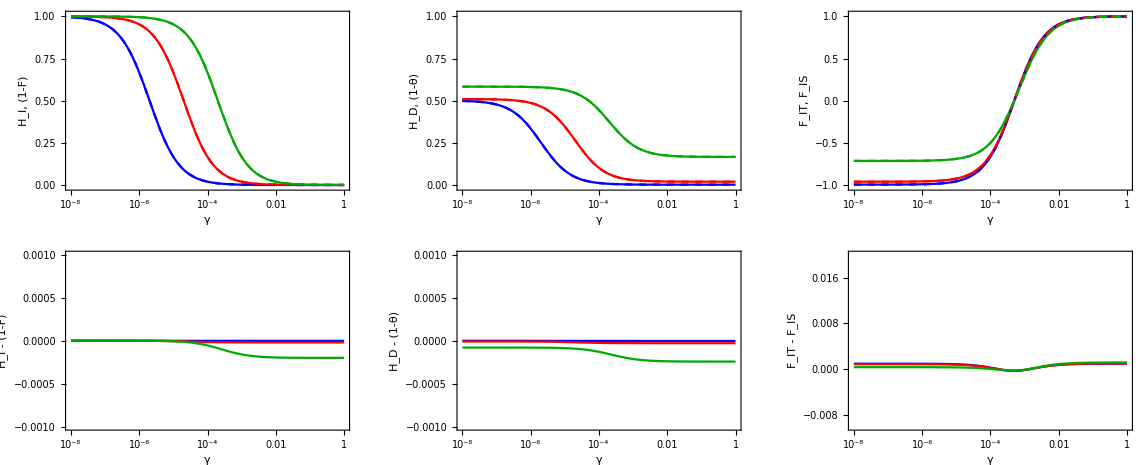

```mathematica
muvalues=10^{-6,-5,-4};
standardN=10^3;
γMin=10^-8;
yrange={-0.01,1.01};

(* actual plots: *)

plotHetIF=LogLinearPlot[Evaluate[Join[Table[equiHetI[γ,muvalues⟦i⟧,standardN],{i,3}],Table[1-Fhat[γ,muvalues⟦i⟧,standardN],{i,3}]]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I, (1-F)",20]}];

plotHetDθ=LogLinearPlot[Evaluate[Join[Table[equiHetD[γ,muvalues⟦i⟧,standardN],{i,3}],Table[1-θhat[γ,muvalues⟦i⟧,standardN],{i,3}]]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_D, (1-θ)",20]}];

plotFITFIS=LogLinearPlot[Evaluate[Join[Table[equiFIT[γ,muvalues⟦i⟧,standardN],{i,3}],Table[FIShat[γ,muvalues⟦i⟧,standardN],{i,3}]]],{γ,γMin,1},PlotRange->{{γMin,1},{-1.02,1.02}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["F_IT, F_IS",20]}];

plotΔHetIF=LogLinearPlot[Evaluate[Table[equiHetI[γ,muvalues⟦i⟧,standardN]-(1-Fhat[γ,muvalues⟦i⟧,standardN]),{i,3}]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.001,0.001}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I - (1-F)",20]}];

plotΔHetDθ=LogLinearPlot[Evaluate[Table[equiHetD[γ,muvalues⟦i⟧,standardN]-(1-θhat[γ,muvalues⟦i⟧,standardN]),{i,3}]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.001,0.001}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_D - (1-θ)",20]}];

plotΔFITFIS=LogLinearPlot[Evaluate[Table[equiFIT[γ,muvalues⟦i⟧,standardN]-FIShat[γ,muvalues⟦i⟧,standardN],{i,3}]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.01,0.02}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["F_IT - F_IS",20]}];

GraphicsGrid[{{plotHetIF,plotHetDθ,plotFITFIS},{plotΔHetIF,plotΔHetDθ,plotΔFITFIS}}]
```

### Corresponding quantities in sexual populations

```mathematica
HISexualhat[γ_,μ_,NN_]:=4NN μ/(1+4NN μ);
ESF4[a1_,a2_,a3_,a4_,θ_]:=(4!)/(θ(θ+1)(θ+2)(θ+3))θ^a1/(1^a1 a1!)θ^a2/(2^a2 a2!)θ^a3/(3^a3 a3!)θ^a4/(4^a4 a4!); (* Ewens sampling formula. Probability that, when sampling 4 alleles, a1 alleles are present in one copy, a2 in two copies and so on *)

HGSexualhat[γ_,μ_,NN_]:=1-ESF4[0,0,0,1,4NN μ]-ESF4[0,2,0,0,4NN μ]/3;
```

Checking properties of Ewens sampling formula:

```mathematica
FullSimplify[HGSexualhat[γ,μ,NN]==ESF4[4,0,0,0,4NN μ]+ESF4[2,1,0,0,4NN μ]+2ESF4[0,2,0,0,4NN μ]/3+ESF4[1,0,1,0,4NN μ]]
```

True

```mathematica
FullSimplify[4ESF4[4,0,0,0,4NN μ]+3ESF4[2,1,0,0,4NN μ]+2ESF4[0,2,0,0,4NN μ]+2ESF4[1,0,1,0,4NN μ]+ESF4[0,0,0,1,4NN μ]==1+(4NN μ)/(4NN μ+1)+(4NN μ)/(4NN μ+2)+(4NN μ)/(4NN μ+3)] (* expected number of alleles *)
```

True

Same quantities in inbreeding sexual populations:

```mathematica
solutionInbreeding=FullSimplify[Solve[{(1-HI)==(1-μ)^2(σ(1-HI/2)+(1-σ)(1-HT)),(1-HT)==(1-μ)^2(1/NN (1-HI/2)+(1-1/NN)(1-HT))},{HI,HT}]]
```

{{HI→(2 (-2+μ) μ (-(-1+μ)^2+NN (-1+(-1+μ)^2 σ)))/(1+(-2+μ) μ (-(-2+μ) μ+NN (-2+(-1+μ)^2 σ))),HT→((-2+μ) μ (-(-1+μ)^2+NN (-2+(-1+μ)^2 σ)))/(1+(-2+μ) μ (-(-2+μ) μ+NN (-2+(-1+μ)^2 σ)))}}

```mathematica
FullSimplify[solutionInbreeding/.{σ->0}]
```

{{HI→(2 (NN+(-1+μ)^2) (-2+μ) μ)/(-1+(-2+μ) μ (2 NN+(-2+μ) μ)),HT→((2 NN+(-1+μ)^2) (-2+μ) μ)/(-1+(-2+μ) μ (2 NN+(-2+μ) μ))}}

```mathematica
HIhatinbreeding[σ_,μ_,NN_]=(HI/.solutionInbreeding)⟦1⟧;
HThatinbreeding[σ_,μ_,NN_]=(HT/.solutionInbreeding)⟦1⟧;
FIThatinbreeding[σ_,μ_,NN_]:=FullSimplify[(HThatinbreeding[σ,μ,NN]-HIhatinbreeding[σ,μ,NN])/HThatinbreeding[σ,μ,NN]];
```

```mathematica
Simplify[FIThatinbreeding[σ,μ,NN]==(NN σ-1)/(1+NN (2/(1-μ)^2- σ))]
```

True

### Producing the final figure

This figure contains the results from the simple model (HI, HT, FIT) and the HG result from the more complex previous model. Also, it includes the simulation results and results for outbreeding sexual populations for comparison.

```mathematica
muvalues=10^{-6,-5,-4};
standardmu=10^-6;
standardN=10^3;
γMin=10^-8;
yrange={-0.01,1.01};

(* actual plots: *)
plotHetI=LogLinearPlot[Evaluate[Join[Table[1-Fhat[γ,muvalues⟦i⟧,standardN],{i,3}],Table[HISexualhat[γ,muvalues⟦i⟧,standardN],{i,3}]]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I",20]}];
plotHetT=LogLinearPlot[Evaluate[Join[Table[1-θhat[γ,muvalues⟦i⟧,standardN],{i,3}],Table[HISexualhat[γ,muvalues⟦i⟧,standardN],{i,3}]]],{γ,γMin,1},PlotRange->{{1γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_T",20]}];
plotFIT=LogLinearPlot[Evaluate[Join[Table[FIShat[γ,muvalues⟦i⟧,standardN],{i,3}],Table[0,{i,3}]]],{γ,γMin,1},PlotRange->{{γMin,1},{-1.02,1.02}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["F_IT",20]}];
plotHetG=LogLinearPlot[Evaluate[Join[Table[equiHetG[γ,muvalues⟦i⟧,standardN],{i,3}],Table[HGSexualhat[γ,muvalues⟦i⟧,standardN],{i,3}]]],{γ,γMin,1},PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_G",20]}];
```

Plots for simulation results:

```mathematica
μvalues=10^{-6,-5,-4};
γvalues=10^Range[-7,-1];
SetDirectory["/users/janengelstaedter/dropbox/projects/RecAutomixis"];
headings={"gamma","mu","Rep","p1","p2","p3","p4","p5","p6","p7","HI","HT","FIS","HG"};
allMeans={headings};
Do[
results=Import["Neutral diversity screen samplesize=500 sampleEvery1000gen randomIniPop Rep"<>ToString[rep]<>".xlsx"]⟦1⟧;
Do[
AppendTo[allMeans,Join[{γvalues⟦i⟧,μvalues⟦j⟧,rep},Mean[Select[results,(#⟦1⟧==γvalues⟦i⟧ && #⟦2⟧==μvalues⟦j⟧)&]⟦All,6;;16⟧]]];
allMeans⟦-1,13⟧= (allMeans⟦-1,12⟧-allMeans⟦-1,11⟧)/allMeans⟦-1,12⟧;(* re-calculate means for FIS based on means for HI and HT: *)
,{j,1,Length[μvalues]},{i,1,Length[γvalues]}]
,{rep,1,10}];
grandMeans=Drop[Prepend[Map[Mean,Partition[SortBy[allMeans,#⟦2⟧&],10]],headings],None,{3}];
StandardError[data_]:=StandardDeviation[data]/Sqrt[Length[data]];
grandMeans//TableForm
```

gamma | mu | p1 | p2 | p3 | p4 | p5 | p6 | p7 | HI | HT | FIS | HG
1/10000000 | 1/1000000 | 0.0001112 | 0.0003672 | 0. | 0. | 0.995216 | 0.0043058 | 0. | 0.999705 | 0.501021 | -0.995338 | 0.004673
1/1000000 | 1/1000000 | 0.350703 | 0.0024396 | 1.8×10^-6 | 0. | 0.64394 | 0.0029146 | 8.×10^-7 | 0.648076 | 0.325379 | -0.990723 | 0.0053568
1/100000 | 1/1000000 | 0.83836 | 0.0070374 | 0. | 0.000013 | 0.154138 | 0.0004512 | 0. | 0.158108 | 0.0809392 | -0.694947 | 0.0075016
1/10000 | 1/1000000 | 0.972901 | 0.0076802 | 2.×10^-6 | 0.000166 | 0.019088 | 0.000163 | 0. | 0.0230921 | 0.0136744 | -0.565644 | 0.0080112
1/1000 | 1/1000000 | 0.995414 | 0.0027652 | 2.×10^-7 | 0.001232 | 0.0005882 | 6.×10^-7 | 0. | 0.0019715 | 0.00290935 | 0.323017 | 0.003998
1/100 | 1/1000000 | 0.998084 | 0.0004154 | 0. | 0.0014924 | 8.2×10^-6 | 0. | 0. | 0.0002159 | 0.0017042 | 0.825567 | 0.0019078
1/10 | 1/1000000 | 0.998455 | 0.0000362 | 0. | 0.0015086 | 0. | 0. | 0. | 0.0000181 | 0.0015267 | 0.985096 | 0.0015448
1/10000000 | 1/100000 | 0.0133158 | 0.0008124 | 0. | 0. | 0.948431 | 0.0367236 | 0.0007176 | 0.986278 | 0.502882 | -0.961168 | 0.0382536
1/1000000 | 1/100000 | 0.0309424 | 0.0024252 | 9.4×10^-6 | 0. | 0.928843 | 0.0370704 | 0.0007098 | 0.96784 | 0.494156 | -0.958538 | 0.0402148
1/100000 | 1/100000 | 0.279462 | 0.0243132 | 0.0003658 | 0.0000778 | 0.668424 | 0.0265542 | 0.0008032 | 0.708121 | 0.367531 | -0.92573 | 0.0521142
1/10000 | 1/100000 | 0.813036 | 0.0530016 | 0.0009334 | 0.0025466 | 0.12531 | 0.0051454 | 0.0000266 | 0.15745 | 0.0965215 | -0.618389 | 0.0616536
1/1000 | 1/100000 | 0.95122 | 0.0276542 | 0.0004866 | 0.0130226 | 0.007347 | 0.0002692 | 2.×10^-7 | 0.0216868 | 0.0312119 | 0.297522 | 0.0414328
1/100 | 1/100000 | 0.978911 | 0.0037024 | 0.0000628 | 0.0172116 | 0.0001064 | 5.8×10^-6 | 0. | 0.0019948 | 0.0191832 | 0.893752 | 0.0209826
1/10 | 1/100000 | 0.981773 | 0.000345 | 7.2×10^-6 | 0.0178728 | 1.4×10^-6 | 2.×10^-7 | 0. | 0.0001777 | 0.0180534 | 0.989785 | 0.0182252
1/10000000 | 1/10000 | 8.6×10^-6 | 0.0001106 | 6.4×10^-6 | 0. | 0.715244 | 0.238042 | 0.0465882 | 0.999933 | 0.582804 | -0.715762 | 0.284748
1/1000000 | 1/10000 | 0.0015776 | 0.0009822 | 0.0001664 | 0. | 0.710524 | 0.241049 | 0.045701 | 0.997848 | 0.582407 | -0.713362 | 0.287898
1/100000 | 1/10000 | 0.0350076 | 0.0236294 | 0.0042642 | 0.0000524 | 0.664704 | 0.225098 | 0.0472446 | 0.950993 | 0.564551 | -0.684539 | 0.300289
1/10000 | 1/10000 | 0.24299 | 0.143482 | 0.0267986 | 0.0069228 | 0.413555 | 0.139898 | 0.026354 | 0.664947 | 0.443517 | -0.499199 | 0.343455
1/1000 | 1/10000 | 0.648154 | 0.164847 | 0.034262 | 0.0821812 | 0.0508408 | 0.016461 | 0.0032542 | 0.17011 | 0.239887 | 0.290076 | 0.301005
1/100 | 1/10000 | 0.809288 | 0.0297396 | 0.0061822 | 0.153551 | 0.000878 | 0.0002964 | 0.000065 | 0.0192003 | 0.175329 | 0.890544 | 0.189834
1/10 | 1/10000 | 0.828484 | 0.0028898 | 0.000561 | 0.168051 | 0.000013 | 1.4×10^-6 | 4.×10^-7 | 0.0017402 | 0.170064 | 0.989731 | 0.171503

```mathematica
style={Directive[Blue,PointSize[0.02]],Directive[Red,PointSize[0.02]],Directive[Darker[Green],PointSize[0.02]]};
plotHetISimul=ListLogLinearPlot[Partition[grandMeans⟦2;;Length[grandMeans],{1,10}⟧,7],PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->style,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I",20]}];
plotHetTSimul=ListLogLinearPlot[Partition[grandMeans⟦2;;Length[grandMeans],{1,11}⟧,7],PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->style,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I",20]}];
plotFITSimul=ListLogLinearPlot[Partition[grandMeans⟦2;;Length[grandMeans],{1,12}⟧,7],PlotRange->{{γMin,1},{-1.02,1.02}},PlotStyle->style,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I",20]}];
plotHetGSimul=ListLogLinearPlot[Partition[grandMeans⟦2;;Length[grandMeans],{1,13}⟧,7],PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->style,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["γ",20],Style["H_I",20]}];
```

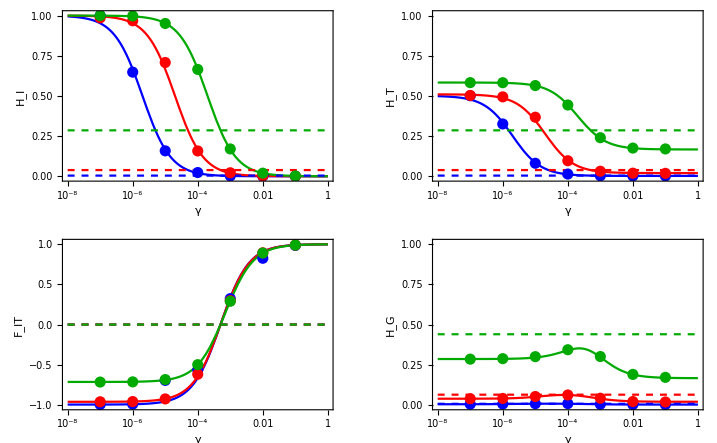

```mathematica
GraphicsGrid[{{Show[plotHetI,plotHetISimul],
Show[plotHetT,plotHetTSimul]},{
Show[plotFIT,plotFITSimul],
Show[plotHetG,plotHetGSimul]}}]
```

### Figure to show statistics as a function of map distance

```mathematica
N[gamma[1]]
```

0.00985149

```mathematica
muvalues=10^{-6,-5,-4};
standardN=10^3;
gamma[d_]:=1/3(1-Exp[-3d/100]);  (* γ as a function of map distance d in centiMorgans for central fusion automixis *)
dmax=2;
plotstyles={Directive[Blue,Thickness[0.007]],Directive[Red,Thickness[0.007]],Directive[Darker[Green],Thickness[0.007]],Directive[Blue,Dashed,Thickness[0.007]],Directive[Red,Dashed,Thickness[0.007]],Directive[Darker[Green],Dashed,Thickness[0.007]]};
```

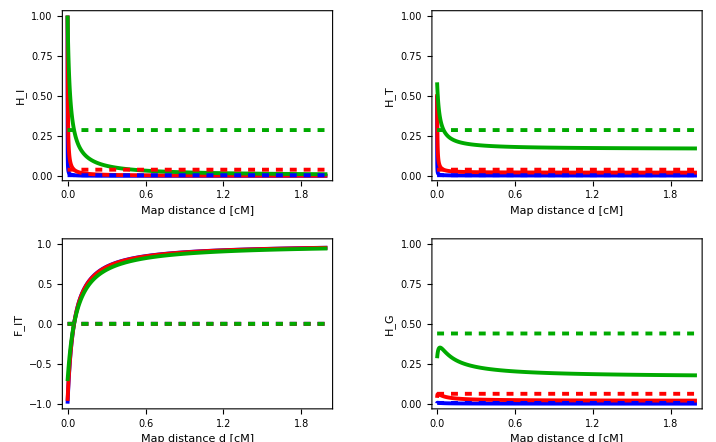

```mathematica
plotHetI=Plot[Evaluate[Join[Table[1-Fhat[gamma[d],muvalues⟦i⟧,standardN],{i,3}],Table[HISexualhat[gamma[d],muvalues⟦i⟧,standardN],{i,3}]]],{d,0,dmax},PlotRange->{{0,dmax},{-0.01,1.01}},PlotStyle->plotstyles,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["Map distance d [cM]",20],Style["H_I",20]}];
plotHetT=Plot[Evaluate[Join[Table[1-θhat[gamma[d],muvalues⟦i⟧,standardN],{i,3}],Table[HISexualhat[gamma[d],muvalues⟦i⟧,standardN],{i,3}]]],{d,0,dmax},PlotRange->{{0,dmax},{-0.01,1.01}},PlotStyle->plotstyles,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["Map distance d [cM]",20],Style["H_T",20]}];
plotFIT=Plot[Evaluate[Join[Table[FIShat[gamma[d],muvalues⟦i⟧,standardN],{i,3}],Table[0,{i,3}]]],{d,0,dmax},PlotRange->{{0,dmax},{-1.02,1.02}},PlotStyle->plotstyles,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["Map distance d [cM]",20],Style["F_IT",20]}];
plotHetG=Plot[Evaluate[Join[Table[equiHetG[gamma[d],muvalues⟦i⟧,standardN],{i,3}],Table[HGSexualhat[gamma[d],muvalues⟦i⟧,standardN],{i,3}]]],{d,0,dmax},PlotRange->{{0,dmax},{-0.01,1.01}},PlotStyle->plotstyles,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["Map distance d [cM]",20],Style["H_G",20]}];
GraphicsGrid[{{plotHetI,plotHetT},{plotFIT,plotHetG}}]
```

### Comparison to inbreeding populations

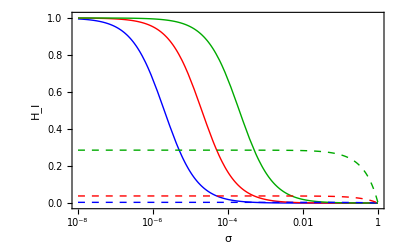

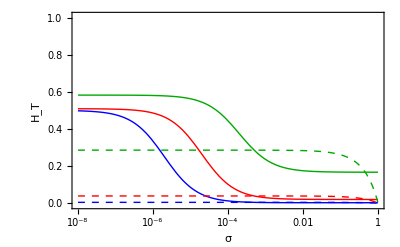

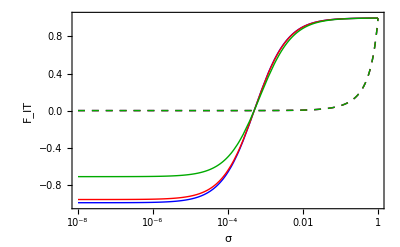

```mathematica
σMin=10^-8;
plotHIinbreeding=LogLinearPlot[Evaluate[Join[Table[1-Fhat[σ,muvalues⟦i⟧,standardN],{i,3}],Table[HIhatinbreeding[σ,muvalues⟦i⟧,standardN],{i,3}]]],{σ,σMin,1},PlotRange->{{γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["σ",20],Style["H_I",20]}]
plotHTinbreeding=LogLinearPlot[Evaluate[Join[Table[1-θhat[σ,muvalues⟦i⟧,standardN],{i,3}],Table[HIhatinbreeding[σ,muvalues⟦i⟧,standardN],{i,3}]]],{σ,σMin,1},PlotRange->{{1γMin,1},{-0.01,1.01}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["σ",20],Style["H_T",20]}]
plotFITinbreeding=LogLinearPlot[Evaluate[Join[Table[FIShat[σ,muvalues⟦i⟧,standardN],{i,3}],Table[FIThatinbreeding[σ,muvalues⟦i⟧,standardN],{i,3}]]],{σ,σMin,1},PlotRange->{{γMin,1},{-1.02,1.02}},PlotStyle->{Blue,Red,Darker[Green],Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Darker[Green],Dashed]},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{Style["σ",20],Style["F_IT",20]}]
```

## One-locus model

### Recursion equation with only locus A considered

#### Derivation

```mathematica
MutationStep1L[{paa_,pAa_,pAA_},muA_]:={paa (1-muA)^2+pAa muA(1-muA)+pAA muA^2,paa (2 muA(1-muA))+pAa ((1-muA)^2+muA^2)+pAA (2 muA(1-muA)),paa muA^2+pAa(muA(1-muA))+pAA(1-muA)^2};
AutomixisStep1L[{paa_,pAa_,pAA_},γA_]:={paa+pAa γA/2,pAa(1-γA),pAA+pAa γA/2};
SelectionStep1L[{paa_,pAa_,pAA_},hA_,sA_]:={paa,pAa(1+hA sA),pAA(1+sA)}/(1+pAa hA sA+pAA sA);
Recursion1L[{pAa_,pAA_},γA_,muA_,sA_,hA_]:=AutomixisStep1L[MutationStep1L[SelectionStep1L[{1-pAa-pAA,pAa,pAA},hA,sA],muA],γA]⟦2;;3⟧;
```

#### Final formula

```mathematica
FullSimplify[Recursion1L[{pAa,pAA},γ,mu,s,h]]
```

{-((pAa+2 (-1+mu) mu (-1+2 pAa)+(h (1+2 (-1+mu) mu) pAa-2 (-1+mu) mu pAA) s) (-1+γ))/(1+h pAa s+pAA s),(2 pAA (1+s)+2 mu^2 (-1-pAA s+pAa (2+h s)) (-1+γ)+pAa (1+h s) γ+2 mu (pAA (-2+s (-2+γ))+γ+pAa (1+h s-(2+h s) γ)))/(2+2 (h pAa+pAA) s)}

```mathematica
FullSimplify[Recursion1L[{pAa,pAA},γ,mu,s,h]=={((pAa+2mu (1-mu)(1-2 pAa)+(h (1-2 (1-mu) mu) pAa+2 mu(1-mu)  pAA) s) (1-γ))/(1+h pAa s+pAA s),
(2 pAA (1+s)+2 mu^2 (-1-pAA s+pAa (2+h s)) (-1+γ)+pAa (1+h s) γ+2 mu (pAA (-2+s (-2+γ))+γ+pAa (1+h s-(2+h s) γ)))/(2+2 (h pAa+pAA) s)}]
```

True

```mathematica
FullSimplify[Recursion1L[{pAa,pAA},γ,mu,s,h]=={(pAa+2mu (1-mu)(1-2 pAa)+(h (1-2 (1-mu) mu) pAa+2 mu(1-mu)  pAA) s) (1-γ),(pAA (1+s)+ mu^2 (1+pAA s-pAa (2+h s)) (1-γ)+pAa (1+h s) γ/2-mu (pAA (2+s (2-γ))-γ-pAa (1+h s-(2+h s) γ)))}/(1+h pAa s+pAA s)]
```

True

#### Recursion equation for sexual population

```mathematica
SexStep1L[{paa_,pAa_,pAA_}]:={paa^2+paa pAa+pAa^2/4,paa pAa+2paa pAA+pAa^2/2+pAa pAA,pAa^2/4+pAa pAA+pAA^2};
Recursion1LSexual[{pAa_,pAA_},muA_,sA_,hA_]:=SexStep1L[MutationStep1L[SelectionStep1L[{1-pAa-pAA,pAa,pAA},hA,sA],muA]]⟦2;;3⟧;
```

```mathematica
Simplify[Recursion1LSexual[{pAa,pAA},mu,s,h]]
```

{(-4 (-1+pAA) pAA (1+s)+pAa^2 (-1+h^2 s^2)+2 pAa (1+h s+pAA (-2-s+h s^2)))/(2 (1+h pAa s+pAA s)^2),(pAa+h pAa s+2 pAA (1+s))^2/(4 (1+h pAa s+pAA s)^2)}

### Plotting the evolutionary dynamics

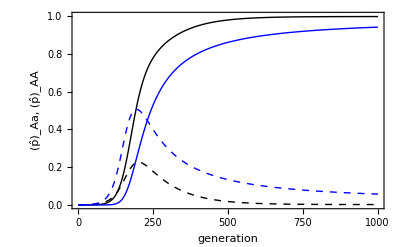

```mathematica
meannCA=0;
(*γ=1/3(1-Exp[-3meannCA/2]);*)
γ=0.01;
s=0.05;
h=1;
mu=0.00001;
gens=1000;
ps=Table[{0,0},{gens+1}];
ps⟦1⟧={0,0};
psSexual=ps;
For[g=1,g≤gens,g++,ps⟦g+1⟧=Recursion1L[ps⟦g⟧,γ,mu,s,h]];
For[g=1,g≤gens,g++,psSexual⟦g+1⟧=pnextAonlySexual[psSexual⟦g⟧,mu,s,h]];
ListLinePlot[Join[Transpose[ps],Transpose[psSexual]],PlotRange->{0,1},Frame->True,PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Black],Directive[Blue,Dashed],Directive[Blue]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["generation",20],Style["(p̂)_Aa, (p̂)_AA",20]}]
```

### Overdominance

#### Recursion equation without mutation:

```mathematica
FullSimplify[Recursion1L[{pAa,pAA},γ,0,s,h]=={(pAa (1+h s) (1-γ))/(1+h s pAa +pAA s),(pAA (1+s)+pAa (1+h s) γ/2)/(1+h s pAa+pAA s)}]
```

True

```mathematica
pnextAonlyNoMutation[{pAa_,pAA_},γ_,saa_,sAA_]:={(pAa (1-γ))/(1-(1-pAa-pAA) saa-pAA sAA),(pAA (1-sAA)+pAa γ/2)/(1-(1-pAa-pAA) saa-pAA sAA)};
```

```mathematica
FullSimplify[Recursion1LSexual[{pAa,pAA},0,s,h]=={((pAa(1+h s) +2 pAA (1+s)) (2-2 pAA-pAa (1-h s)))/(2 (1+h pAa s+pAA s)^2),(pAa(1+h s)+2 pAA (1+s))^2/(4 (1+h pAa s+pAA s)^2)}]
```

True

```mathematica
FullSimplify[Recursion1LSexual[{pAa,pAA},0,s,h]=={((1-pAa-pAA) pAa(1+h s)+2(1-pAa-pAA) pAA(1+s)+pAa^2/2(1+h s)^2+pAa pAA(1+s)(1+h s))/(1+h pAa s+pAA s)^2,(pAa(1+h s)+2 pAA (1+s))^2/(4 (1+h pAa s+pAA s)^2)}]
```

True

```mathematica
pnextAonlyNoMutationSexual[{pAa_,pAA_},saa_,sAA_]:={((1-pAa-pAA) pAa(1+saa)+2(1-pAa-pAA) pAA(1+saa)(1+sAA)+pAa^2/2+pAa pAA(1+sAA))/(1+(1- pAa -pAA)saa+pAA sAA)^2,(pAa+2 pAA (1+sAA))^2/(4 (1+(1- pAa -pAA)saa+pAA sAA)^2)};
```

#### Fixed point analysis

```mathematica
fixedPoints={pAa,pAA}/.FullSimplify[Solve[pnextAonlyNoMutation[{pAa,pAA},γ,saa,sAA]=={pAa,pAA},{pAa,pAA}]]
```

{{0,0},{0,1},{(2 (saa-γ) (-sAA+γ))/(-2 saa sAA+(saa+sAA) γ),(γ (-saa+γ))/(-2 saa sAA+(saa+sAA) γ)}}

```mathematica
Simplify[(2 (saa-γ) (-sAA+γ))/(-2 saa sAA+(saa+sAA) γ)==1-γ(saa+sAA-2γ)/(2 saa sAA-(saa+sAA) γ)]
```

True

```mathematica
fixedPointsSexual={pAa,pAA}/.FullSimplify[Solve[pnextAonlyNoMutationSexual[{pAa,pAA},saa,sAA]=={pAa,pAA},{pAa,pAA}]]
```

{{0,0},{0,1},{(2 saa sAA)/(saa+sAA)^2,saa^2/(saa+sAA)^2}}

Plotting the result:

```mathematica
pAahat[γ_,saa_,sAA_]:=If[γ<saa && γ<sAA,(2 (saa-γ) (sAA-γ))/(2 saa sAA-(saa+sAA) γ),"NA"];
pAAhat[γ_,saa_,sAA_]:=If[γ<saa && γ<sAA,(γ (saa-γ))/(2 saa sAA-(saa+sAA) γ),"NA"];
pAahatSexual[γ_,saa_,sAA_ ]:=(2 saa sAA)/(saa+sAA)^2;
pAAhatSexual[γ_,saa_,sAA_]:=saa^2/(saa+sAA)^2;
```

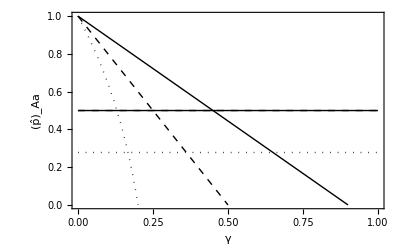

```mathematica
overdominancePlot=Show[Plot[{pAahat[γ,0.9,0.9],pAahatSexual[γ,0.9,0.9],pAahat[γ,0.5,0.5],pAahatSexual[γ,0.5,0.5],pAahat[γ,0.2,1],pAahatSexual[γ,0.2,1]},{γ,0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->{Directive[Thick,Black],Directive[Thin,Black],Directive[Thick,Black,Dashed],Directive[Thin,Black,Dashed],Directive[Thick,Black,Dotted],Directive[Black,Dotted]},FrameStyle->Directive[Black,16],ImageSize->400,FrameLabel->{Style["γ",20],Style["(p̂)_Aa",20]}]]
```

#### Stability analysis

```mathematica
Jacob[{pAa_,pAA_}]=FullSimplify[D[pnextAonlyNoMutation[{pAa,pAA},γ,saa,sAA],{{pAa,pAA}}]];
MatrixForm[Jacob[{pAa,pAA}]]
```

(-((1+(-1+pAA) saa-pAA sAA) (-1+γ))/(1+(-1+pAa+pAA) saa-pAA sAA)^2 | (pAa (saa-sAA) (-1+γ))/(1+(-1+pAa+pAA) saa-pAA sAA)^2
(2 pAA saa (-1+sAA)+γ-saa γ+pAA (saa-sAA) γ)/(2 (1+(-1+pAa+pAA) saa-pAA sAA)^2) | (-2 (1+(-1+pAa) saa) (-1+sAA)+pAa (-saa+sAA) γ)/(2 (1+(-1+pAa+pAA) saa-pAA sAA)^2))

```mathematica
For[i=1,i≤Length[fixedPoints],i++,
Print[MatrixForm[FullSimplify[Jacob[fixedPoints⟦i⟧],Assumptions->{γ>0&&γ<1&&sAA>0&&sAA<1&&saa>0&&saa<1}]]];
Print[FullSimplify[Eigenvalues[Jacob[fixedPoints⟦i⟧]],Assumptions->{γ>0&&γ<1&&sAA>0&&sAA<1&&saa>0&&saa<1}]];
];
```

((-1+γ)/(-1+saa) | 0
γ/(2-2 saa) | (-1+sAA)/(-1+saa))

{(-1+sAA)/(-1+saa),(-1+γ)/(-1+saa)}

((-1+γ)/(-1+sAA) | 0
-(-2 saa+γ)/(2 (-1+sAA)) | (-1+saa)/(-1+sAA))

{(-1+saa)/(-1+sAA),(-1+γ)/(-1+sAA)}

((sAA (-1+γ) γ+2 saa^2 (-sAA+γ)+saa (2 sAA-γ (1+γ)))/((-1+γ) (-2 saa sAA+(saa+sAA) γ)) | -(2 (saa-sAA) (saa-γ) (sAA-γ))/((-1+γ) (-2 saa sAA+(saa+sAA) γ))
-((saa-sAA) (2 saa-γ) γ)/(2 (-1+γ) (-2 saa sAA+(saa+sAA) γ)) | (-saa^2 γ+sAA (-1+sAA-γ) γ+saa (-2 sAA^2+(-1+γ) γ+2 sAA (1+γ)))/((-1+γ) (-2 saa sAA+(saa+sAA) γ)))

{(-1+saa)/(-1+γ),(-1+sAA)/(-1+γ)}

This stability analysis shows that:
  1) fixation of the aa genotype is unstable if sAA<saa or saa>γA,
  2) fixation of the AA genotype is unstable if saa>sAA or sAA>γA,
  3) genotype Aa is stably maintained in the population if γA<saa and γA<sAA

#### Segregation load

```mathematica
SegregationLoad[γ_,saa_,sAA_]:=(1-pAahat[γ, saa,sAA]-pAAhat[γ, saa,sAA])saa+pAAhat[γ, saa,sAA]sAA;
SegregationLoadSexual[γ_,saa_,sAA_]:=(1-pAahatSexual[γ, saa,sAA]-pAAhatSexual[γ, saa,sAA])saa+pAAhatSexual[γ, saa,sAA]sAA;
```

```mathematica
Simplify[SegregationLoadSexual[γ,saa,sAA]] (* formula in Crow & Kimura textbook p.304: (saa sAA)/(saa+sAA) *)
```

(saa sAA)/(saa+sAA)

```mathematica
FullSimplify[SegregationLoad[γ,saa,sAA]]
```

Piecewise[{{saa-2 NA saa+NA sAA, saa≤γ||sAA≤γ}, {γ, True}}]

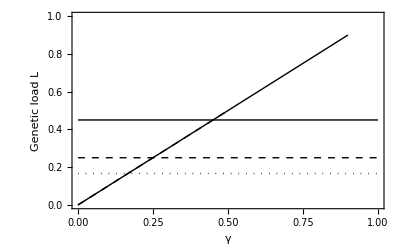

```mathematica
segregationLoadPlot=Show[Plot[{SegregationLoad[γA,0.9,0.9],SegregationLoadSexual[γA,0.9,0.9],SegregationLoad[γA,0.5,0.5],SegregationLoadSexual[γA,0.5,0.5],SegregationLoad[γA,0.2,1],SegregationLoadSexual[γA,0.2,1]},{γA,0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->{Directive[Thick,Black],Directive[Thin,Black],Directive[Thick,Black,Dashed],Directive[Thin,Black,Dashed],Directive[Thick,Black,Dotted],Directive[Thin,Black,Dotted]},FrameStyle->Directive[16,Black],ImageSize->400,FrameLabel->{Style["γ",20],Style["Genetic load L",20]}]]
```

```mathematica
Show[overdominancePlot]
```

-Graphics-

#### Comparison with sexual populations

Value of γ where there are the same frequencies of heterozygotes in the sexual and asexual population:

```mathematica
FullSimplify[Solve[(2 (s-γ) (s-γ))/(2 s s-(s+s) γ)==2(s s)/(s+s)^2,{γ}]]
FullSimplify[Solve[(2 (saa-γ) (sAA-γ))/(2 saa sAA-(saa+sAA) γ)==2(saa sAA)/(sAA+saa)^2,{γ}]]
```

{{γ→s/2}}

{{γ→(saa sAA)/(saa+sAA)},{γ→(saa^2+sAA^2)/(saa+sAA)}}

```mathematica
{{γ->(saa sAA)/(saa+sAA)},{γ->(saa^2+sAA^2)/(saa+sAA)}}/.{saa->0.1,sAA->1}
```

{{γ→0.0909091},{γ→0.918182}}

Value of γ where there the genetic load is the same in the sexual and asexual population:

```mathematica
FullSimplify[Solve[γ==(s s)/(s+s),{γ}]]
FullSimplify[Solve[γ==(saa sAA)/(saa+sAA),{γ}]]
```

{{γ→s/2}}

{{γ→(saa sAA)/(saa+sAA)}}

### Mutation-selection balance

#### Trying to analytically solve the original recursion equation

```mathematica
solutionRecessive={pAa,pAA}/.Solve[{pAa,pAA}==Recursion1L[{pAa,pAA},γA,muA,sA,hA],{pAa,pAA}]⟦3⟧
```

```mathematica
Simplify[solutionRecessive]
```

$Aborted

```mathematica
%/.{γA->0,muA->0.000001,sA->-0.01}
```

{{pAa→3.41364+1.02696×10^-15 ⅈ,pAA→0.000337998+1.45215×10^-15 ⅈ},{pAa→-0.00020004+4.77396×10^-15 ⅈ,pAA→1.0002-9.54696×10^-15 ⅈ},{pAa→0.58577-5.88418×10^-15 ⅈ,pAA→0.0000579831+8.31924×10^-15 ⅈ}}

#### Approximation of recursion equations assuming that mu is small and that there is no back mutation

```mathematica
MutationStep1LApprox[{paa_,pAa_,pAA_},muA_]:={paa (1-2muA),paa 2 muA+pAa (1-muA),pAa muA+pAA};
Simplify[AutomixisStep1L[MutationStep1LApprox[SelectionStep1L[{1-pAa-pAA,pAa,pAA},hA,-sA],muA],γA]⟦2;;3⟧]
```

{((pAa-hA pAa sA+muA (2-2 pAA+pAa (-3+hA sA))) (-1+γA))/(-1+hA pAa sA+pAA sA),(2 pAA (-1+sA)+pAa (-1+hA sA) γA+muA (2 (-1+pAA) γA+pAa (-2-hA sA (-2+γA)+3 γA)))/(2 (-1+hA pAa sA+pAA sA))}

```mathematica
Recursion1LApprox[{pAa_,pAA_},γ_,mu_,s_,h_]:={(((1-h s)(1-mu)pAa+2mu (1- pAA-pAa)) (1-γ))/(1-h s pAa -pAA s),((1-pAA -pAa )mu γ+pAa (1-h s)(γ/2+mu(1-γ/2))+pAA (1-s))/(1-h s pAa -pAA s)};
```

Checking that this is in line with the recursion equation using the approximate mutation step:

```mathematica
Simplify[Recursion1LApprox[{pAa,pAA},γA,muA,sA,hA]==AutomixisStep1L[MutationStep1LApprox[SelectionStep1L[{1-pAa-pAA,pAa,pAA},hA,-sA],muA],γA]⟦2;;3⟧]
```

True

Approximation for sexual evolution:

```mathematica
FullSimplify[SexStep1L[MutationStep1LApprox[SelectionStep1L[{1-pAa-pAA,pAa,pAA},hA,-sA],muA]]⟦2;;3⟧]
```

{-((-1+muA) (-2+pAa+2 pAA+hA pAa sA) (2 pAA (-1+sA)+pAa (-1+hA sA)+muA (-2+pAa+2 pAA+hA pAa sA)))/(2 (-1+hA pAa sA+pAA sA)^2),(2 pAA (-1+sA)+pAa (-1+hA sA)+muA (-2+pAa+2 pAA+hA pAa sA))^2/(4 (-1+hA pAa sA+pAA sA)^2)}

```mathematica
Recursion1LSexualApprox[{pAa_,pAA_},mu_,s_,h_]:={-((-1+mu) (-2+pAa+2 pAA+h pAa s) (2 pAA (-1+s)+pAa (-1+h s)+mu (-2+pAa+2 pAA+h pAa s)))/(2 (-1+h pAa s+pAA s)^2),(2 pAA (-1+s)+pAa (-1+h s)+mu (-2+pAa+2 pAA+h pAa s))^2/(4 (-1+h pAa s+pAA s)^2)};
```

```mathematica
FullSimplify[SexStep1L[MutationStep1LApprox[SelectionStep1L[{1-pAa-pAA,pAa,pAA},h,-s],mu]]⟦2;;3⟧==Recursion1LSexualApprox[{pAa,pAA},mu,s,h]]
```

True

#### Deriving the equilibrium of the approximated system

```mathematica
FullSimplify[Solve[Recursion1LApprox[{pAa,pAA},γ,mu,s,h]=={pAa,pAA},{pAa,pAA}],Assumptions->s>mu&&h>0&&h<1&&γ>γCO&&γ<1&&mu>0&&mu<0.01]
```

{{pAa→0,pAA→1},{pAa→(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),pAA→-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-10 h-3 h s)))+mu (5+h (-4+s (-7+2 h+4 h s)))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)) Sign[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))},{pAa→(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),pAA→-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-10 h-3 h s)))+mu (5+h (-4+s (-7+2 h+4 h s)))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)) Sign[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}}

```mathematica
Simplify[Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)]==Abs[mu (3-h (2+s)) (1-γ)+γ-s (1-h(1- γ))]]
```

True

```mathematica
Solve[mu (3-h (2+s)) (1-γ)+γ-s (1-h(1- γ))==0,γ]
```

{{γ→(-3 mu+2 h mu+s-h s+h mu s)/(1-3 mu+2 h mu-h s+h mu s)}}

```mathematica
γCO=1-(1-s)/(1-h s-mu (3-h (2+s))); (* cutoff above which the above term in the Abs[...] expression is positive *)
```

```mathematica
FullSimplify[Solve[Recursion1LApprox[{pAa,pAA},γ,mu,s,h]=={pAa,pAA},{pAa,pAA}],Assumptions->s>mu&&h>0&&h<1&&γ>(1-(1-s)/(1-h s-mu (3-h (2+s))))&&γ<1&&mu>0&&mu<0.01]
```

{{pAa→0,pAA→1},{pAa→(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),pAA→-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-10 h-3 h s)))+mu (5+h (-4+s (-7+2 h+4 h s)))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-(√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/Sign[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))},{pAa→(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),pAA→-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-10 h-3 h s)))+mu (5+h (-4+s (-7+2 h+4 h s)))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+(√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/Sign[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}}

```mathematica
%/.{γ->0.1,mu->0.00001, s->0.01,h->0.99999}
```

{{pAa→0,pAA→1},{pAa→0.000164962,pAA→0.000917602},{pAa→21.804,pAA→-10.9021}}

```mathematica
equi1[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-10 h-3 h s)))+mu (5+h (-4+s (-7+2 h+4 h s)))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)) Sign[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))};
equi2[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-10 h-3 h s)))+mu (5+h (-4+s (-7+2 h+4 h s)))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)) Sign[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}
```

```mathematica
FullSimplify[equi1[γ,mu,s,h],Assumptions->s>mu&&h>0&&h<1&&(mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))>0&&γ<1&&mu>0&&mu<0.01]
```

{(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ))))/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}

```mathematica
equi1gr0[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ))))/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))};
```

```mathematica
FullSimplify[equi2[γ,mu,s,h],Assumptions->s>mu&&h>0&&h<1&&(mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))>0&&γ<1&&mu>0&&mu<0.01]
```

{(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ))))/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}

```mathematica
equi2gr0[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ))))/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))};
```

```mathematica
FullSimplify[equi1[γ,mu,s,h],Assumptions->s>mu&&h>0&&h<1&&(mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))<0&&γ<1&&mu>0&&mu<0.01]
```

{(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}

```mathematica
equi1ls0[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))};
```

```mathematica
FullSimplify[equi2[γ,mu,s,h],Assumptions->s>mu&&h>0&&h<1&&(mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))<0&&γ<1&&mu>0&&mu<0.01]
```

{(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))}

```mathematica
equi2ls0[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))+√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) Abs[mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)])/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))};
```

```mathematica
γCO/.{h->0.5}
```

1-(1-s)/(1-0.5 s-mu (3-0.5 (2+s)))

```mathematica
Clear[mu,s]
FullSimplify[equi1gr0[γ,mu,s,0],Assumptions->s>mu&&h>0&&h<1&&γ>0&&γ<1&&mu>0&&mu<0.01]
```

{-(2 mu (mu-s) (-1+γ))/(s (-γ+mu (-2+3 γ))),mu/s}

```mathematica
Manipulate[GraphicsGrid[{{Plot[Evaluate[Log10/@{equi1ls0[γ,mu,s,h]}],{γ,0,0.2},PlotRange->{-6.2,0.2},Frame->True],Plot[Evaluate[Log10/@{equi1gr0[γ,mu,s,h]}],{γ,0,0.2},PlotRange->{-6.2,0.2},Frame->True]},{Plot[Evaluate[Log10/@{equi2ls0[γ,mu,s,h]}],{γ,0,0.2},PlotRange->{-6.2,0.2},Frame->True],Plot[Evaluate[Log10/@{equi2gr0[γ,mu,s,h]}],{γ,0,0.2},PlotRange->{-6.2,0.2},Frame->True]}}],{{mu,0.00001},0,0.001},{{s,0.01},0,0.1},{h,0,1}]
```

Plot::exclul: {Im[equi1ls0[γ, 0.00001, 0.01, 0]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[equi1gr0[γ, 0.00001, 0.01, 0]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[equi2ls0[γ, 0.00001, 0.01, 0]] - 0} must be a list of equalities or real-valued functions.

General::stop: Further output of Plot :: exclul will be suppressed during this calculation.

#### Final equilibrium formula and some approximations

```mathematica
equilibrium[γ_,mu_,s_,h_]:={(5 mu^2-3 mu s+h^2 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ))-h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ))))/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),-((2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2-√((mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ)))/(2 s (-2 (-1+h) (-h s+mu (-1+h (2+s)))+(-1+2 h) (1-h s+mu (-3+h (2+s))) γ)))};
```

Writing the equilibrium using some helper functions:

```mathematica
HELP1[γ_,mu_,s_,h_]:=(mu+h (-1+mu) s)^2+2 (mu-2 mu^2+h (-1+mu)^2 s-h^2 (-1+mu)^2 s^2) γ+(1-2 mu+h (-1+mu) s)^2 γ^2; 
HELP2[γ_,mu_,s_,h_]:=5 mu^2-3 mu s+h^2 (1-mu) s (s-mu (2+s)) (1-γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2;
HELP3[γ_,mu_,s_,h_]:=2(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s-mu (3-h (2+s))) γ);

HELP4[γ_,mu_,s_,h_]:=h (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))
HELP5[γ_,mu_,s_,h_]:=2 mu (-1+h s) (-h s+mu (-3+h (4+s)))+(h s (1-h s)+mu^2 (-13+h (14+s (12-h (10+3 s))))+mu (5+h (-4+s (-7+h (2+4 s))))) γ+(1-2 mu+h (-1+mu) s) (1-h s+mu (-3+h (2+s))) γ^2(* helpter functions *)
```

```mathematica
Simplify[equilibrium[γ,mu,s,h]=={2HELP2[γ,mu,s,h]-2 √HELP1[γ,mu,s,h] (mu (3-h (2+s)) (1-γ)+γ+s (-1+h-h γ))-2HELP4[γ,mu,s,h],√HELP1[γ,mu,s,h] (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ))-HELP5[γ,mu,s,h]}/ HELP3[γ,mu,s,h]]
```

True

Deriving approximations for the helper functions that discard all term in mu^2:

```mathematica
Collect[HELP1[γ,mu,s,h],mu]
Collect[HELP2[γ,mu,s,h],mu]
Collect[HELP3[γ,mu,s,h],mu]
Collect[HELP4[γ,mu,s,h],mu]
Collect[HELP5[γ,mu,s,h],mu]
```

h^2 s^2+2 h s γ-2 h^2 s^2 γ+γ^2-2 h s γ^2+h^2 s^2 γ^2+mu (-2 h s-2 h^2 s^2+2 γ-4 h s γ+4 h^2 s^2 γ-4 γ^2+6 h s γ^2-2 h^2 s^2 γ^2)+mu^2 (1+2 h s+h^2 s^2-4 γ+2 h s γ-2 h^2 s^2 γ+4 γ^2-4 h s γ^2+h^2 s^2 γ^2)

h^2 s^2 (1-γ)^2-s γ+γ^2+mu (-3 s-h^2 s^2 (1-γ)^2-h^2 s (2+s) (1-γ)^2+4 γ+4 s γ-5 γ^2)+mu^2 (5+h^2 s (2+s) (1-γ)^2-11 γ+6 γ^2)

2 (2 (-1+h) h s^2+(-1+2 h) s γ-h (-1+2 h) s^2 γ)+2 mu (-2 (-1+h) s (-1+h (2+s))+(1-2 h) s (3-h (2+s)) γ)

-h s (s-2 γ) (-1+γ)+h mu (s (6+s-7 γ)-2 γ) (-1+γ)+h mu^2 (-1+γ) (-6+4 γ+s (-2+5 γ))

h s (1-h s) γ+γ^2-2 h s γ^2+h^2 s^2 γ^2+mu (-2 h s (-1+h s)+(5+h (-4+s (-7+h (2+4 s)))) γ-2 γ^2+3 h s γ^2-h^2 s^2 γ^2+(-3+h (2+s)) γ^2-h s (-3+h (2+s)) γ^2)+mu^2 (2 (-1+h s) (-3+h (4+s))+(-13+h (14+s (12-h (10+3 s)))) γ-2 (-3+h (2+s)) γ^2+h s (-3+h (2+s)) γ^2)

```mathematica
HELP1Approx[γ_,mu_,s_,h_]:=h^2 s^2+2 h s γ-2 h^2 s^2 γ+γ^2-2 h s γ^2+h^2 s^2 γ^2+mu (-2 h s-2 h^2 s^2+2 γ-4 h s γ+4 h^2 s^2 γ-4 γ^2+6 h s γ^2-2 h^2 s^2 γ^2); 
HELP2Approx[γ_,mu_,s_,h_]:=h^2 s^2 (1-γ)^2-s γ+γ^2+mu (-3 s-h^2 s^2 (1-γ)^2-h^2 s (2+s) (1-γ)^2+4 γ+4 s γ-5 γ^2);
HELP3Approx[γ_,mu_,s_,h_]:=HELP3[γ,mu,s,h];

HELP4Approx[γ_,mu_,s_,h_]:=-h s (s-2 γ) (-1+γ)+h mu (s (6+s-7 γ)-2 γ) (-1+γ);
HELP5Approx[γ_,mu_,s_,h_]:=h s (1-h s) γ+γ^2-2 h s γ^2+h^2 s^2 γ^2+mu (-2 h s (-1+h s)+(5+h (-4+s (-7+h (2+4 s)))) γ-2 γ^2+3 h s γ^2-h^2 s^2 γ^2+(-3+h (2+s)) γ^2-h s (-3+h (2+s)) γ^2);
```

```mathematica
equilibriumApprox[γ_,mu_,s_,h_]:={2HELP2Approx[γ,mu,s,h]-2 √HELP1Approx[γ,mu,s,h] (mu (3-h (2+s)) (1-γ)+γ+s (-1+h-h γ))-2HELP4Approx[γ,mu,s,h],√HELP1Approx[γ,mu,s,h] (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ))-HELP5Approx[γ,mu,s,h]}/ HELP3Approx[γ,mu,s,h];
```

```mathematica
FullSimplify[equilibriumApprox[γ,mu,s,h]]
```

{(-h (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)) (-1+γ)+h^2 s^2 (-1+γ)^2+γ (-s+γ)-mu (s (3+2 h^2 (-1+γ)^2-4 γ)+2 h^2 s^2 (-1+γ)^2+γ (-4+5 γ))-(mu (-3+h (2+s)) (-1+γ)+γ+s (-1+h-h γ)) √(-h^2 (-1+2 mu) s^2 (-1+γ)^2+γ (mu (2-4 γ)+γ)+2 h s (-1+γ) (mu-γ+3 mu γ)))/(-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ),(h s (-1+h s) γ-γ^2+2 h s γ^2-h^2 s^2 γ^2+√(-h^2 (-1+2 mu) s^2 (-1+γ)^2+γ (mu (2-4 γ)+γ)+2 h s (-1+γ) (mu-γ+3 mu γ)) (γ-h s γ+mu (2-2 h s-3 γ+h (2+s) γ))+mu (5 (-1+γ) γ+2 h^2 s (-1+γ) (s (-1+γ)+γ)+h (-2 (-2+γ) γ+s (-2-7 (-1+γ) γ))))/(2 (-2 (-1+h) s (-h s+mu (-1+h (2+s)))+(-1+2 h) s (1-h s+mu (-3+h (2+s))) γ))}

#### Deriving the equilibrium of the sexual approximated system

```mathematica
FullSimplify[Solve[Recursion1LSexualApprox[{pAa,pAA},mu,s,h]=={pAa,pAA},{pAa,pAA}],Assumptions->s>mu&&h>0&&h<1&&mu>0&&mu<0.01]
```

{{pAa→0,pAA→1},{pAa→-(2 mu-4 h mu+h s-h^2 s+h mu s+h^2 mu^2 s+(1+h (-1+mu)) √(s ((4-8 h) mu+h^2 (1+mu)^2 s)))/((1-2 h)^2 s),pAA→((2-4 h) mu+h^2 (1+mu)^2 s+h √(s ((4-8 h) mu+h^2 (1+mu)^2 s))+h mu √(s ((4-8 h) mu+h^2 (1+mu)^2 s)))/(2 (1-2 h)^2 s)},{pAa→(-2 mu+4 h mu-h s+h^2 s-h mu s-h^2 mu^2 s+(1+h (-1+mu)) √(s ((4-8 h) mu+h^2 (1+mu)^2 s)))/((1-2 h)^2 s),pAA→((2-4 h) mu+h^2 (1+mu)^2 s-h √(s ((4-8 h) mu+h^2 (1+mu)^2 s))-h mu √(s ((4-8 h) mu+h^2 (1+mu)^2 s)))/(2 (1-2 h)^2 s)}}

```mathematica
%/.{mu->0.00001,s->0.02,h->0.1}
```

{{pAa→0,pAA→1},{pAa→-0.293336,pAA→0.0168521},{pAa→0.00958267,pAA→0.0000231796}}

```mathematica
equilibriumSexual[mu_,s_,h_]:={(-2 mu+4 h mu-h s+h^2 s-h mu s-h^2 mu^2 s+(1+h (-1+mu)) √(s ((4-8 h) mu+h^2 (1+mu)^2 s)))/((1-2 h)^2 s),((2-4 h) mu+h^2 (1+mu)^2 s-h √(s ((4-8 h) mu+h^2 (1+mu)^2 s))-h mu √(s ((4-8 h) mu+h^2 (1+mu)^2 s)))/(2 (1-2 h)^2 s)};
```

#### A few special cases

Recessive mutations:

```mathematica
FullSimplify[equilibrium[γ,mu,s,0],Assumptions->h≥0&&h≤1&&γ≥0&&γ≤1&&mu>0&&mu<0.01]
```

{-(2 mu (mu-s) (-1+γ))/(s (-γ+mu (-2+3 γ))),mu/s}

```mathematica
Simplify[(2 mu (s-mu) (1-γ))/(s (γ+mu (2-3 γ)))==-(2 mu (mu-s) (-1+γ))/(s (-γ+mu (-2+3 γ)))]
```

True

Dominant mutations:

```mathematica
FullSimplify[equilibrium[γ,mu,s,1],Assumptions->s>mu&&h≥0&&h≤1&&γ≥0&&γ≤1&&mu>0&&mu<0.01]
```

{1/((-1+mu) (-1+s) s γ)(5 mu^2-3 mu s+(-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2-(-1+s) (mu (-1+γ)-γ) √((mu+(-1+mu) s)^2+2 (mu-2 mu^2+(-1+mu)^2 s-(-1+mu)^2 s^2) γ+(1+mu (-2+s)-s)^2 γ^2)-(-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))),-1/(2 (-1+mu) s γ)(2 mu (mu+(-1+mu) s)-(s+mu (1+mu-4 s+3 mu s)) γ+(-1+mu) (1+mu (-2+s)-s) γ^2+(-mu (-2+γ)+γ) √((mu+(-1+mu) s)^2+2 (mu-2 mu^2+(-1+mu)^2 s-(-1+mu)^2 s^2) γ+(1+mu (-2+s)-s)^2 γ^2))}

Semidominant mutations:

```mathematica
FullSimplify[equilibrium[γ,mu,s,1/2],Assumptions->s>0&&h≥0&&h≤1&&γ≥0&&γ≤1&&mu>0&&mu<1]
```

{1/((-1+mu) s^2)2 (5 mu^2-3 mu s+1/4 (-1+mu) s (-s+mu (2+s)) (-1+γ)^2+4 mu γ-11 mu^2 γ-s γ+4 mu s γ+γ^2-5 mu γ^2+6 mu^2 γ^2+1/4 (s-mu (-4+s) (-1+γ)+(-2+s) γ) √((s-mu (2+s))^2-2 (4 mu (-1+2 mu)-2 (-1+mu)^2 s+(-1+mu)^2 s^2) γ+(2+mu (-4+s)-s)^2 γ^2)-1/2 (-1+γ) (-s (s-2 γ)+mu (s (6+s-7 γ)-2 γ)+mu^2 (-6+4 γ+s (-2+5 γ)))),-1/(4 (-1+mu) s^2)(2 mu (mu (-2+s)-s) (-2+s)-((-2+s) s-4 mu (3+(-3+s) s)+mu^2 (24+s (-14+3 s))) γ+(2+mu (-4+s)-s)^2 γ^2+√((s-mu (2+s))^2-2 (4 mu (-1+2 mu)-2 (-1+mu)^2 s+(-1+mu)^2 s^2) γ+(2+mu (-4+s)-s)^2 γ^2) ((-2+s) γ+mu (-4+2 s+4 γ-s γ)))}

Apomictic reproduction:

```mathematica
FullSimplify[equilibrium[0,mu,s,h],Assumptions->s>0&&h≥0&&h≤1&&mu>0&&mu<1&&s<1]
```

{Piecewise[{{(mu+(-1+h) s-h mu s)/((-1+h) s), mu+h mu s≥h s}, {(2 mu (2 mu-s))/(s (-h s+mu (-1+h (2+s)))), True}}],Piecewise[{{(mu-h mu s)/(s-h s), mu+h mu s≥h s}, {(2 mu^2 (-1+h s))/(s (-h s+mu (-1+h (2+s)))), True}}]}

First part of this result (mu>hs/(1+hs)):

```mathematica
Simplify[1-(mu(1-h s))/((1-h) s)==(mu+(-1+h) s-h mu s)/((-1+h) s)]
```

True

```mathematica
Simplify[(mu(1-h s))/(s(1-h))==(mu-h mu s)/(s-h s)]
```

True

```mathematica
sprime=(s(1-h ))/(1-s h);
Simplify[mu/sprime==(mu-h mu s)/(s-h s)]
```

True

```mathematica
Simplify[sprime==1-(1-s)/(1-h s)]
```

True

```mathematica
Simplify[1-(mu(1-h s))/((1-h) s)/.{mu->h s/(1+h s)}]
Simplify[(2 mu (2 mu-s))/(s (-h s+mu (-1+h (2+s))))/.{mu->h s/(1+h s)}]
```

-(1+h (-2+s))/((-1+h) (1+h s))

-(1+h (-2+s))/((-1+h) (1+h s))

Second part of this result (mu<hs/(1+hs)):

```mathematica
Simplify[1-(2 mu (2 mu-s))/(s (-h s+mu (-1+h (2+s))))-(2 mu^2 (-1+h s))/(s (-h s+mu (-1+h (2+s))))]
```

-((2 mu-s) (mu-h s+h mu s))/(s (-h s+mu (-1+h (2+s))))

```mathematica
Simplify[(2 mu (s-2 mu))/(s (h s+mu (1-h (2+s))))==(2 mu (2 mu-s))/(s (-h s+mu (-1+h (2+s))))]
```

True

```mathematica
Simplify[(2 mu^2 (1-h s))/(s (h s+mu (1-h (2+s))))==(2 mu^2 (-1+h s))/(s (-h s+mu (-1+h (2+s))))]
```

True

```mathematica
Simplify[(2 mu^2 (-1+h s))/(s (-h s+mu (-1+h (2+s))))/.{mu->s/2}]
```

1

Gamete duplication:

```mathematica
FullSimplify[equilibrium[1,mu,s,h],Assumptions->s>0&&h≥0&&h≤1&&γ≥0&&γ≤1&&mu>0&&mu<1]
```

{0,mu/s}

Special cases with sexual reproduction:

```mathematica
FullSimplify[equilibriumSexual[mu,s,0]]
FullSimplify[equilibriumSexual[mu,s,1/2],Assumptions->s>mu&&mu>0&&mu<0.01]
FullSimplify[equilibriumSexual[mu,s,1],Assumptions->s>mu&&mu>0&&mu<0.01]
```

{(2 (-mu+√(mu s)))/s,mu/s}

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,ComplexInfinity}

{(mu (2-(1+mu) s+√(s (-4 mu+(1+mu)^2 s))))/s,-(2 mu-(1+mu)^2 s+√(s (-4 mu+(1+mu)^2 s))+mu √(s (-4 mu+(1+mu)^2 s)))/(2 s)}

```mathematica
Simplify[-(2 mu-(1+mu)^2 s+√(s (-4 mu+(1+mu)^2 s))+mu √(s (-4 mu+(1+mu)^2 s)))/(2 s)==-(2 mu-(1+mu)^2 s+(1+mu) √(s (-4 mu+(1+mu)^2 s)))/(2 s)]
```

True

```mathematica
FullSimplify[Solve[Recursion1LSexualApprox[{pAa,pAA},mu,s,1/2]=={pAa,pAA},{pAa,pAA}],Assumptions->s>mu&&h>0&&h<1&&mu>0&&mu<0.01]
```

{{pAa→0,pAA→1},{pAa→(4 mu (mu (-2+s)+s))/((1+mu)^2 s^2),pAA→(4 mu^2)/((1+mu)^2 s^2)}}

Apomictic reproduction: starting again from the original recursion equation

```mathematica
FullSimplify[Recursion1LApprox[{pAa,pAA},0,mu,s,h]]
```

{(pAa (-1+h s)+mu (-2+3 pAa+2 pAA-h pAa s))/(-1+h pAa s+pAA s),(pAA (-1+s)+mu pAa (-1+h s))/(-1+h pAa s+pAA s)}

```mathematica
Recursion1LClonal[{pAa_,pAA_},mu_,s_,h_]:={(pAa (-1+h s)+mu (-2+3 pAa+2 pAA-h pAa s))/(-1+h pAa s+pAA s),(pAA (-1+s)+mu pAa (-1+h s))/(-1+h pAa s+pAA s)};
fixedPoints=FullSimplify[Solve[Recursion1LClonal[{pAa,pAA},mu,s,h]=={pAa,pAA},{pAa,pAA}],Assumptions->h≥0&&h≤1&&s>0&&s<1&&mu>0&&mu<1&&pAa≥0&&pAa≤1&&pAA≥0&&pAA≤1]
```

{{pAa→0,pAA→1},{pAa→(mu+(-1+h) s-h mu s)/((-1+h) s),pAA→(mu-h mu s)/(s-h s)},{pAa→(2 mu (2 mu-s))/(s (-h s+mu (-1+h (2+s)))),pAA→(2 mu^2 (-1+h s))/(s (-h s+mu (-1+h (2+s))))}}

```mathematica
Jacob=FullSimplify[D[Recursion1LClonal[{pAa,pAA},mu,s,h],{{pAa,pAA}}]];
```

```mathematica
FullSimplify[Eigenvalues[Jacob/.fixedPoints⟦1⟧]]
FullSimplify[Eigenvalues[Jacob/.fixedPoints⟦2⟧]]
FullSimplify[Eigenvalues[Jacob/.fixedPoints⟦3⟧]]
```

{(-1+2 mu)/(-1+s),-((-1+mu) (-1+h s))/(-1+s)}

{(1-2 mu)/((-1+mu) (-1+h s)),(1-s)/((-1+mu) (-1+h s))}

{(-1+s)/(-1+2 mu),-((-1+mu) (-1+h s))/(-1+2 mu)}

#### Plotting the results

```mathematica
eqFreqsRecessive⟦1⟧=numSol[0.0001,mu,s,0];
```

```mathematica
eqFreqsRecessiveSexualAnalytical=Table[√(mu/s),{γ,0,γmax,0.001}];
eqFreqsAdditiveSexualAnalytical=Table[2mu/s,{γ,0,γmax,0.001}];
eqFreqsDominantSexualAnalytical=Table[mu/s,{γ,0,γmax,0.001}];
```

```mathematica
eqFreqsRecessiveAnalytical=Table[MutSelAnalyticalApproxRecessive[γA,mu,-s],{γA,0,γmax,0.001}];
```

```mathematica
γmax=0.2;
s=0.05;
mu=0.00001;
```

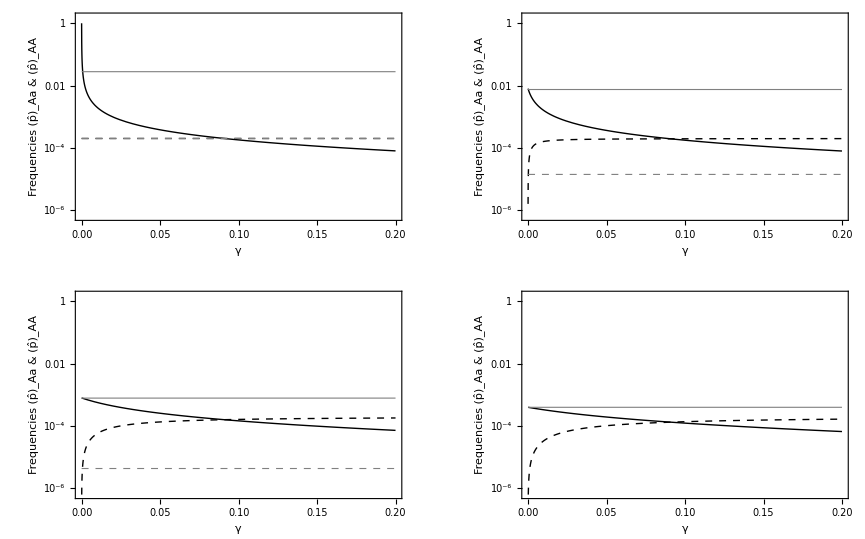

```mathematica
h=0;
plotRecessive=Plot[Evaluate[Log10/@Flatten/@{equilibrium[γ,mu,s,h],equilibriumSexual[mu,s,h]}],{γ,0,γmax},PlotRange->{-6.2,0.2},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thick,Black,Dashed],Directive[Thickness[0.002],Gray],Directive[Thickness[0.002],Gray,Dashed]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Frequencies (p̂)_Aa & (p̂)_AA",20]},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"0.001"},{-2,0.01},{-1,"0.1"},{0,1}},None},{Automatic, None}}];
h=0.05;
plotPRecessive=Plot[Evaluate[Log10/@Flatten/@{equilibrium[γ,mu,s,h],equilibriumSexual[mu,s,h]}],{γ,0,γmax},PlotRange->{-6.2,0.2},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thick,Black,Dashed],Directive[Thickness[0.002],Gray],Directive[Thickness[0.002],Gray,Dashed]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Frequencies (p̂)_Aa & (p̂)_AA",20]},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"0.001"},{-2,0.01},{-1,"0.1"},{0,1}},None},{Automatic, None}}];
h=0.499999;
plotAdditive=Plot[Evaluate[Log10/@Flatten/@{equilibrium[γ,mu,s,h],equilibriumSexual[mu,s,h]}],{γ,0,γmax},PlotRange->{-6.2,0.2},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thick,Black,Dashed],Directive[Thickness[0.002],Gray],Directive[Thickness[0.002],Gray,Dashed]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Frequencies (p̂)_Aa & (p̂)_AA",20]},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"0.001"},{-2,0.01},{-1,"0.1"},{0,1}},None},{Automatic, None}}];
h=1;
plotDominant=Plot[Evaluate[Log10/@Flatten/@{equilibrium[γ,mu,s,h],equilibriumSexual[mu,s,h]}],{γ,0,γmax},PlotRange->{-6.2,0.2},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thick,Black,Dashed],Directive[Thickness[0.002],Gray],Directive[Thickness[0.002],Gray,Dashed]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Frequencies (p̂)_Aa & (p̂)_AA",20]},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"0.001"},{-2,0.01},{-1,"0.1"},{0,1}},None},{Automatic, None}}];
GraphicsGrid[{{plotRecessive,plotPRecessive},{plotAdditive,plotDominant}}]
```

```mathematica
Clear[mu,s]
equilibriumSexual[mu,s,0]
```

{(-2 mu+2 √(mu s))/s,mu/s}

#### Genetic load in the population

```mathematica
Load[{pAa_,pAA_},s_,h_]:=pAa h s+pAA s;
```

```mathematica
Clear[mu,s,h,γ]
FullSimplify[Load[equilibrium[γ,mu,s,0],s,0]]
FullSimplify[Load[equilibrium[0,mu,s,h],s,h]]
```

1/2 (mu (3-2 γ)+γ-√((mu+γ-2 mu γ)^2))

1/2 (h s+mu (3-h s)-√((mu+h (-1+mu) s)^2))

```mathematica
γmax=0.2;
s=0.05;
mu=0.00001;
```

```mathematica
h=0.6;
Load[equilibriumSexual[mu,s,h],s,h]
```

0.0000200009

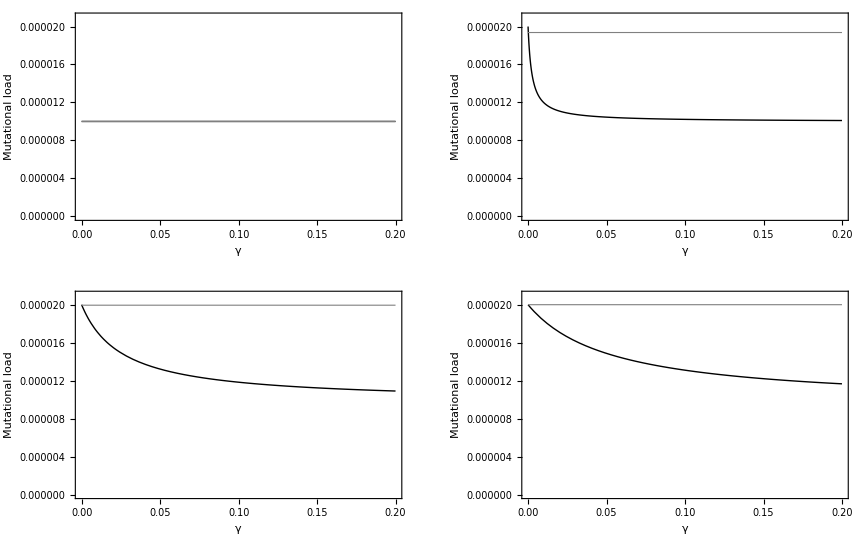

```mathematica
h=0;
plotLoadRecessive=Plot[Evaluate[{Load[equilibrium[γ,mu,s,h],s,h],Load[equilibriumSexual[mu,s,h],s,h]}],{γ,0,γmax},PlotRange->{0,0.000021},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thickness[0.002],Gray]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Mutational load",20]},FrameTicks->{{Automatic,None},{Automatic, None}}];
h=0.05;
plotLoadPRecessive=Plot[Evaluate[{Load[equilibrium[γ,mu,s,h],s,h],Load[equilibriumSexual[mu,s,h],s,h]}],{γ,0,γmax},PlotRange->{0,0.000021},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thickness[0.002],Gray]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Mutational load",20]},FrameTicks->{{Automatic,None},{Automatic, None}}];
h=0.499999;
plotLoadAdditive=Plot[Evaluate[{Load[equilibrium[γ,mu,s,h],s,h],Load[equilibriumSexual[mu,s,h],s,h]}],{γ,0,γmax},PlotRange->{0,0.000021},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thickness[0.002],Gray]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Mutational load",20]},FrameTicks->{{Automatic,None},{Automatic, None}}];
h=1;
plotLoadDominant=Plot[Evaluate[{Load[equilibrium[γ,mu,s,h],s,h],Load[equilibriumSexual[mu,s,h],s,h]}],{γ,0,γmax},PlotRange->{0,0.000021},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{Directive[Thick,Black],Directive[Thickness[0.002],Gray]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Mutational load",20]},FrameTicks->{{Automatic,None},{Automatic, None}}];
GraphicsGrid[{{plotLoadRecessive,plotLoadPRecessive},{plotLoadAdditive,plotLoadDominant}}]
```

All in a single plot:

{Hue[0,0.8,1],Hue[0.3,0.8,1],Hue[0.66,0.8,1],Hue[0.8,0.8,1]}

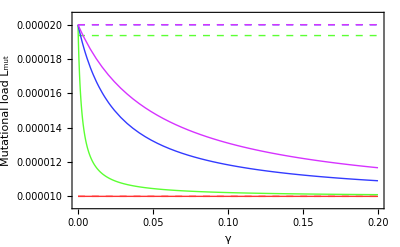

```mathematica
colours={Hue[0,0.8,1],Hue[0.3,0.8,1],Hue[0.66,0.8,1],Hue[0.8,0.8,1]}
Plot[Evaluate[{Load[equilibrium[γ,mu,s,0],s,0],Load[equilibriumSexual[mu,s,0],s,0],Load[equilibrium[γ,mu,s,0.05],s,0.05],Load[equilibriumSexual[mu,s,0.05],s,0.05],Load[equilibrium[γ,mu,s,0.4999],s,0.4999],Load[equilibriumSexual[mu,s,0.4999],s,0.4999],Load[equilibrium[γ,mu,s,1],s,1],Load[equilibriumSexual[mu,s,1],s,1]}],{γ,0,γmax},PlotRange->{0.0000095,0.0000205},Frame->True,FrameStyle->Directive[16,Black],PlotStyle->{colours⟦1⟧,Directive[Dashed,colours⟦1⟧],colours⟦2⟧,Directive[Dashed,colours⟦2⟧],colours⟦3⟧,Directive[Dashed,colours⟦3⟧],colours⟦4⟧,Directive[Dashed,colours⟦4⟧]},FrameStyle->16,ImageSize->400,FrameLabel->{Style["γ",20],Style["Mutational load L_mut",20]},FrameTicks->{{Automatic,None},{Automatic, None}}]
```

### Speed of adaptation

#### Recursion equation without mutation

```mathematica
FullSimplify[Recursion1L[{pAa,pAA},γ,0,s,h]=={(pAa (1+h s) (1-γ))/(1+pAa h s+pAA s),(pAA (1+s)+pAa (1+h s) γ/2)/(1+pAa h s+pAA s)}]
```

True

```mathematica
FullSimplify[Recursion1LSexual[{pAa,pAA},0,s,h]=={(2(pAa+pAa h s+2 pAA (1+s)) (2-2 pAA-pAa +pAa h s))/(4 (1+pAa h s+pAA s)^2),(pAa+pAa h s+2 pAA (1+s))^2/(4 (1+pAa h s+pAA s)^2)}]
```

True

#### Linearization of model for small pAa and pAA

Writing the approximated model in matrix form:

```mathematica
RecursionLinear[{pAa_,pAA_},γ_,s_,h_]:={pAa (1+h s) (1-γ),pAA (1+s)+pAa (1+h s) γ/2};
```

```mathematica
M[γ_,s_,h_]:=({{(1+h s)(1-γ), 0}, {(1+h s) γ/2, (1+s)}});
Simplify[RecursionLinear[{pAa,pAA},γ,s,h]==M[γ,s,h].{pAa,pAA}]
```

True

Diagonalisation of M as M=B^-1 Mdiag B:

```mathematica
MDiag[γ_,s_,h_]:=DiagonalMatrix[Eigenvalues[M[γ,s,h]]];
B[γ_,s_,h_]:=Transpose[Eigenvectors[M[γ,s,h]]];
Simplify[M[γ,s,h]==B[γ,s,h].MDiag[γ,s,h].Inverse[B[γ,s,h]]]
```

True

Using this to come up with a solution for the linear difference equation:

```mathematica
solutionLinear[t_,{pAa0_,pAA0_},γ_,s_,h_]:=Simplify[B[γ,s,h].MatrixPower[MDiag[γ,s,h],t].Inverse[B[γ,s,h]].{pAa0,pAA0}];
κ=(1+h s) (1-γ);
Simplify[solutionLinear[t,{pAa0,pAA0},γ,s,h]=={pAa0 κ^t,(pAa0 (1+h s) ((1+s)^t-κ^t) γ+2 pAA0 (1+s)^t (1+s-κ))/(2 (1+s-κ))}]
Simplify[solutionLinear[t,{pAa0,0},γ,s,h]=={pAa0 κ^t,(pAa0 (1+h s) γ((1+s)^t-κ^t))/(2 (1+s-κ))}]
```

True

True

More direct way of obtaining the solution using RSolve:

```mathematica
Simplify[RSolve[{pAa[t+1]==pAa[t] (1+h s) (1-γ),pAA[t+1]==pAA[t] (1+s)+pAa[t] (1+h s) γ/2,pAa[0]==pAa0,pAA[0]==0},{pAa[t],pAA[t]},t]]
```

{{pAa[t]→pAa0 (-(1+h s) (-1+γ))^t,pAA[t]→(pAa0 (1+h s) ((1+s)^t-(-(1+h s) (-1+γ))^t) γ UnitStep[-1+t])/(2 (s (1+h (-1+γ))+γ))}}

Checking if this is indeed the solution:

```mathematica
t=10;
Simplify[Nest[RecursionLinear[#,γ,s,h]&,{pAa0,pAA0},t]==solutionLinear[t,{pAa0,pAA0},γ,s,h]]
```

True

Plotting the solution:

```mathematica
Manipulate[ListPlot[Transpose[Table[solutionLinear[t,{0.000001,0},γ,s,h],{t,0,5000}]],PlotRange->All],{γ,0,1},{s,0,0.1},{h,0,1}]
```

Transpose::nmtx: The first two levels of {solutionLinear[0, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[1, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[2, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 45 », solutionLinear[48, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[49, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

Transpose::nmtx: The first two levels of {solutionLinear[0, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[1., {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[2., {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 45 », solutionLinear[48., {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[49., {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

Transpose::nmtx: The first two levels of {solutionLinear[0., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], solutionLinear[1., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], solutionLinear[2., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 45 », solutionLinear[48., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], solutionLinear[49., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{solutionLinear[0., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], solutionLinear[1., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 47 », solutionLinear[49., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 4951 »}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {solutionLinear[0, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[1, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[2, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 46 », solutionLinear[49, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

Transpose::nmtx: The first two levels of {solutionLinear[0, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[1., {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 47 », solutionLinear[49., {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

Transpose::nmtx: The first two levels of {solutionLinear[0., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], solutionLinear[1., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 47 », solutionLinear[49., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{solutionLinear[0., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], solutionLinear[1., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 47 », solutionLinear[49., {1.×10^-6, 0.}, 0.001, 0.002, 0.01], « 4951 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of the one-dimensional list {solutionLinear[0, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[1, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[2, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[3, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[4, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[5, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 40 », solutionLinear[46, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[47, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[48, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[49, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 4951 »} cannot be transposed.

ListPlot::lpn: Transpose[{solutionLinear[0, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[1, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[2, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[3, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[4, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[5, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 40 », solutionLinear[46, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[47, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[48, {1.×10^-6, 0}, 0.001, 0.002, 0.01], solutionLinear[49, {1.×10^-6, 0}, 0.001, 0.002, 0.01], « 4951 »}] is not a list of numbers or pairs of numbers.

Futher approximating the system (Taylor expansion assuming small s and γ):

```mathematica
Clear[t]
Simplify[Normal[Series[((1+h s) (1-γ))^t,{s,0,1}]]==(1-γ)^t(1+h s t)]
Simplify[Normal[Series[(1+s)^t-((1+h s) (1-γ))^t,{s,0,1}]]==1+s t-(1+h s t )(1-γ)^t]
```

True

True

```mathematica
Normal[Series[((1+h s) (1-γ))^t,{s,0,1},{γ,0,1}]]
Normal[Series[(1+s)^t-((1+h s) (1-γ))^t,{s,0,1},{γ,0,1}]]
```

1-t γ+s (h t-h t^2 γ)

t γ+s (t-h t+h t^2 γ)

```mathematica
solutionLinearApprox[t_,pAa0_,γ_,s_,h_]:={pAa0 (1+h s t-γ t(1+h s t)),(pAa0 (1+h s) γ t(s (1-h )+γ(1+h s t)))/(2 (1+s-κ))};
```

```mathematica
pAa0=0.000001;
Manipulate[ListPlot[Transpose[Table[Log[Flatten[{solutionLinear[t,{pAa0,0},γ,s,h]⟦1⟧,solutionLinearApprox[t,pAa0,γ,s,h]}]],{t,0,1000}]],PlotRange->All],{γ,0,1},{s,0,0.1},{h,0,1}]
```

How does mean fitness in the population change through time?

```mathematica
solutionLinearApproxwbar[t_,pAa0_,γ_,s_,h_]:=1+solutionLinearApprox[t,pAa0,γ,s,h].{h s,s};
FullSimplify[solutionLinearApproxwbar[t,pAa0,γ,s,h]]
FullSimplify[solutionLinearApproxwbar[t+1,pAa0,γ,s,h]]-FullSimplify[solutionLinearApproxwbar[t,pAa0,γ,s,h]]
FullSimplify[solutionLinearApproxwbar[t+1,pAa0,γ,s,h]]/FullSimplify[solutionLinearApproxwbar[t,pAa0,γ,s,h]]
```

1-h pAa0 s (1+h s t) (-1+t γ)+(pAa0 s (1+h s) t γ (s-h s+γ+h s t γ))/(2 (1+s-κ))

h pAa0 s (1+h s t) (-1+t γ)-h pAa0 s (1+h s (1+t)) (-1+γ+t γ)-(pAa0 s (1+h s) t γ (s-h s+γ+h s t γ))/(2 (1+s-κ))+(pAa0 s (1+h s) (1+t) γ (γ+s (1+h (-1+γ+t γ))))/(2 (1+s-κ))

(1-h pAa0 s (1+h s (1+t)) (-1+γ+t γ)+(pAa0 s (1+h s) (1+t) γ (γ+s (1+h (-1+γ+t γ))))/(2 (1+s-κ)))/(1-h pAa0 s (1+h s t) (-1+t γ)+(pAa0 s (1+h s) t γ (s-h s+γ+h s t γ))/(2 (1+s-κ)))

Comparing automictic spread with relatively large γ to spread of beneficial mutation in sexual population:

```mathematica
pAa0=0.000001;
Manipulate[ListPlot[Transpose[Table[{pAa0 ((1+h s)γ)/(2(1+s-(1+h s) (1-γ)))(1+s)^t ,pAa0(1+h s)^t},{t,0,1000}]],PlotRange->All],{{γ,0.01},0,1},{{s,0.01},0,0.1},{{h,0.5},0,1}]
```

## Two-locus model with infinite population size

### Plotting the evolutionary dynamics

```mathematica
meannCA=0.0001;
meannAB=0.0001;

sA=0.1;
hA=0.01;
sB=0.1;
hB=0.01;
mu=0.00001;
gens=2000;
p0={1,0,0,0,0,0,0,0,0,0};
```

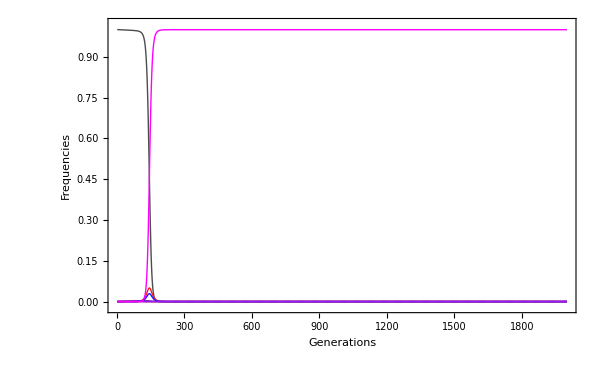

```mathematica
ps=Simulate[p0,gens,meannCA,meannAB,"CentralFusion",mu,mu,sA,hA,sB,hB];
PlotDynamics[ps]
```

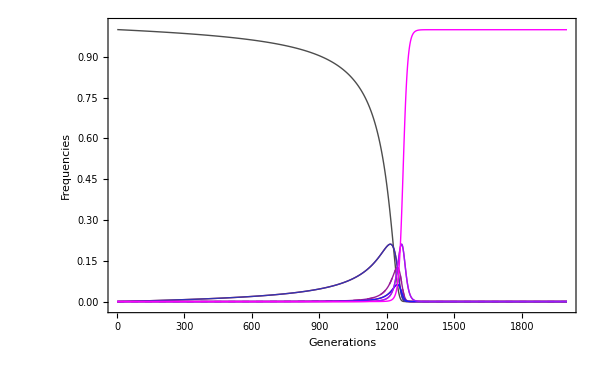

```mathematica
psSex=Simulate[p0,gens,meannCA,meannAB,"Sex",mu,mu,sA,hA,sB,hB];
PlotDynamics[psSex]
```

```mathematica
1+0.99(sA+sB+sA sB)
getMeanFitness[ps[[1120]],sA,hA,sB,hB]
```

1.2079

1.2079

```mathematica
1+0.99(sA+sB+sA sB)
getMeanFitness[psSex[[220]],sA,hA,sB,hB]
```

1.2079

1.20758

### Fractions of metaphase recombinant genotypes under various assumptions for crossovers

#### Defining the two crossover matrices:

```mathematica
matrixRecCA=({{0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1/2, 0, 1/2, 0}, {0, 0, 1/2, 0, 0, 1/2, 0}, {1/2, 0, 0, 0, 1/2, 0, 0}, {0, 0, 1/2, 1/2, 0, 0, 0}, {0, 1/2, 0, 0, 0, 0, 1/2}});
matrixRecAB=({{0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {1/4, 1/4, 1/2, 0, 0, 0, 0}, {0, 0, 0, 0, 1/4, 1/2, 1/4}, {0, 0, 0, 1/2, 1/2, 0, 0}, {0, 0, 0, 1/2, 0, 1/2, 0}, {0, 0, 0, 1/2, 0, 0, 1/2}});
```

#### No crossovers between A and B:

```mathematica
recfracsCAonly=FullSimplify[{1,0,0,0,0,0,0}.∑_(nCA=0)^∞ meannCA^nCA*Exp[-meannCA]/Factorial[nCA]MatrixPower[matrixRecCA,nCA]]
```

{1/3+2/3 ⅇ^(-3 meannCA/2),0,0,0,2/3-2/3 ⅇ^(-3 meannCA/2),0,0}

```mathematica
FullSimplify[recfracsCAonly=={1/3(1+2 ⅇ^(-3 meannCA/2)),0,0,0,2/3(1- ⅇ^(-3 meannCA/2)),0,0}]
```

True

#### No crossovers between C and A:

```mathematica
recfracsABonly=FullSimplify[{1,0,0,0,0,0,0}.(Exp[-meannAB]IdentityMatrix[7]+∑_(nAB=1)^∞ meannAB^nAB*Exp[-meannAB]/Factorial[nAB]MatrixPower[matrixRecAB,nAB])]
```

{1/6 (1+2 ⅇ^(-3 meannAB/2)+3 ⅇ^-meannAB),1/6 (1+2 ⅇ^(-3 meannAB/2)-3 ⅇ^-meannAB),2/3-2/3 ⅇ^(-3 meannAB/2),0,0,0,0}

```mathematica
FullSimplify[recfracsABonly=={1/6 (1+2 ⅇ^(-3 meannAB/2)+3 ⅇ^-meannAB),1/6 (1+2 ⅇ^(-3 meannAB/2)-3 ⅇ^-meannAB),2/3(1-ⅇ^(-3 meannAB/2)),0,0,0,0}]
```

True

#### Free recombination between C and A:

```mathematica
matrixRecCApowerinf=FullSimplify[Limit[MatrixPower[matrixRecCA,n],n->∞]];
recfracsfreeCA=FullSimplify[Exp[-meannAB]{1,0,0,0,0,0,0}.(matrixRecCApowerinf+∑_(nAB=1)^∞ meannAB^nAB/Factorial[nAB]MatrixPower[matrixRecAB.matrixRecCApowerinf,nAB])]
```

{1/18 ⅇ^-meannAB (5+ⅇ^meannAB-meannAB),1/18 (1-ⅇ^-meannAB (1+meannAB)),1/9 (2+ⅇ^-meannAB (-2+meannAB)),1/9 (2+ⅇ^-meannAB (-2+meannAB)),1/9 ⅇ^-meannAB (5+ⅇ^meannAB-meannAB),1/9 (2+ⅇ^-meannAB (-2+meannAB)),1/9-1/9 ⅇ^-meannAB (1+meannAB)}

```mathematica
%/.{meannAB->0}
```

{1/3,0,0,0,2/3,0,0}

#### Free recombination between A and B:

```mathematica
matrixRecABpowerinf=FullSimplify[Limit[MatrixPower[matrixRecAB,n],n->∞]];
recfracsfreeAB=FullSimplify[Exp[-meannCA]{1,0,0,0,0,0,0}.(matrixRecABpowerinf+∑_(nCA=1)^∞ meannCA^nCA/Factorial[nCA]MatrixPower[matrixRecCA.matrixRecABpowerinf,nCA])]
```

{1/18+1/9 ⅇ^(-3 meannCA/2),1/18+1/9 ⅇ^(-3 meannCA/2),2/9+4/9 ⅇ^(-3 meannCA/2),2/9-2/9 ⅇ^(-3 meannCA/2),1/9-1/9 ⅇ^(-3 meannCA/2),2/9-2/9 ⅇ^(-3 meannCA/2),1/9-1/9 ⅇ^(-3 meannCA/2)}

```mathematica
%/.{meannCA->0}
```

{1/6,1/6,2/3,0,0,0,0}

#### Free recombination both between C and A and between A and B:

```mathematica
recfracsfreeACAB=FullSimplify[{1,0,0,0,0,0,0}.matrixRecCApowerinf.matrixRecABpowerinf]
```

{1/18,1/18,2/9,2/9,1/9,2/9,1/9}

A few tests to see if the approach of just multiplying the matrices is justified:

```mathematica
FullSimplify[recfracsfreeACAB=={1,0,0,0,0,0,0}.Limit[MatrixPower[matrixRecCA.matrixRecAB,n],n->∞]]
FullSimplify[recfracsfreeACAB=={1,0,0,0,0,0,0}.Limit[MatrixPower[matrixRecAB.matrixRecCA,n],n->∞]]
FullSimplify[recfracsfreeACAB=={1,0,0,0,0,0,0}.Limit[MatrixPower[matrixRecCA.matrixRecCA.matrixRecAB,n],n->∞]]
FullSimplify[recfracsfreeACAB=={1,0,0,0,0,0,0}.Limit[MatrixPower[matrixRecAB.matrixRecCA.matrixRecCA,n],n->∞]]
FullSimplify[recfracsfreeACAB=={1,0,0,0,0,0,0}.matrixRecCApowerinf.matrixRecABpowerinf]
```

True

True

True

«2 more identical outputs»

#### How different are numerically obtained recfracs to those obtained by assuming independence of COs on both DNA segments?

```mathematica
recfracsIndep=FullSimplify[Exp[-meannCA]Exp[-meannAB]{1,0,0,0,0,0,0}.(IdentityMatrix[7]+∑_(nCA=1)^∞ meannCA^nCA/Factorial[nCA]MatrixPower[matrixRecCA,nCA]).(IdentityMatrix[7]+∑_(nAB=1)^∞ meannAB^nAB/Factorial[nAB]MatrixPower[matrixRecAB,nAB])]
```

{1/18 ⅇ^(-3/2 (meannAB+meannCA)) (2+ⅇ^(3 meannCA/2)) (2+ⅇ^(meannAB/2) (3+ⅇ^meannAB)),1/18 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^(meannAB/2))^2 (2+ⅇ^(meannAB/2)) (2+ⅇ^(3 meannCA/2)),2/9 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^(3 meannAB/2)) (2+ⅇ^(3 meannCA/2)),2/9 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^(3 meannAB/2)) (-1+ⅇ^(3 meannCA/2)),1/18 ⅇ^(-3/2 (meannAB+meannCA)) (1+9 ⅇ^meannAB+2 ⅇ^(3 meannAB/2)) (-1+ⅇ^(3 meannCA/2)),1/9 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^(meannAB/2))^2 (1+2 ⅇ^(meannAB/2)) (-1+ⅇ^(3 meannCA/2)),1/18 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^(meannAB/2))^2 (1+2 ⅇ^(meannAB/2)) (-1+ⅇ^(3 meannCA/2))}

```mathematica
FullSimplify[recfracsIndep==Exp[-meannCA]Exp[-meannAB]{1,0,0,0,0,0,0}.(IdentityMatrix[7]+∑_(nAB=1)^∞ meannAB^nAB/Factorial[nAB]MatrixPower[matrixRecAB,nAB]).(IdentityMatrix[7]+∑_(nCA=1)^∞ meannCA^nCA/Factorial[nCA]MatrixPower[matrixRecCA,nCA])]
```

{0,0,0,0,1/6 ⅇ^(-3/2 (meannAB+meannCA)) (-1-2 ⅇ^(meannAB/2)+3 ⅇ^meannAB) (-1+ⅇ^(3 meannCA/2)),-1/3 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^meannAB) (-1+ⅇ^(3 meannCA/2)),-1/6 ⅇ^(-3/2 (meannAB+meannCA)) (-1+ⅇ^(meannAB/2))^2 (-1+ⅇ^(3 meannCA/2))}=={0,0,0,0,0,0,0}

==> It can be seen that a different result is obtained depending on the order with which the two matrices are multiplied, i.e. there is a differencce between all COs between C and A occuring first, followed by all COs between A and B, or the other way around. Mixed orders of COs therefore will likely yield yet different recfrac proportions of metaphase genotypes.

```mathematica
TableForm[{N[recfracsIndep],PHRecombinantFractionsPoisson[meannCA,meannAB]}/.{meannCA->2, meannAB->2}]
```

0.091972 | 0.0423683 | 0.232184 | 0.200645 | 0.282989 | 0.0998936 | 0.0499468
0.104508 | 0.0380743 | 0.223952 | 0.192404 | 0.2137 | 0.17109 | 0.0562721

### Automixis matrices for varying recombination rates

```mathematica
recValues=Round[10^Range[-5,-1,0.25],0.0000000001];
SetDirectory["/Users/jan/documents/projects/recent/RecAutomixis"];
Get["AutomixisMatrices BACKUP.dat"];
(*AutomixisMatrices={{"RepMode","recCA","recAB","AutomixisMatrix"}};*)
Do[
meannCA=convertMToCOs[recValues⟦irecCA⟧];
meannAB=convertMToCOs[recValues⟦irecAB⟧];
AutomixisMatrix=N[getAutomixisMatrix[meannCA,meannAB,"CentralFusion"]];
AutomixisMatrices=Append[AutomixisMatrices,{"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧,AutomixisMatrix}];
DeleteFile["AutomixisMatrices.dat"];
Save["AutomixisMatrices.dat",AutomixisMatrices]
,{irecCA,Length[recValues]},{irecAB,Length[recValues]}
];
```

```mathematica
(*recValues=Range[0,0.02,0.001];*)
(*SexTensors={{"recAB","SexTensor"}};*)
SetDirectory["/Users/jan/documents/projects/recent/RecAutomixis"];
Get["SexTensors BACKUP.dat"];
Do[
SexTensors=Append[SexTensors,{recValues⟦irecAB⟧,N[getSexTensor[0,convertMToCOs[recValues⟦irecAB⟧]]]}];
DeleteFile["SexTensors.dat"];
Save["SexTensors.dat",SexTensors]
,{irecAB,Length[recValues]}
];
```

### Linkage of two recessive deleterious mutations: associative overdominance

#### Plotting the dynamics

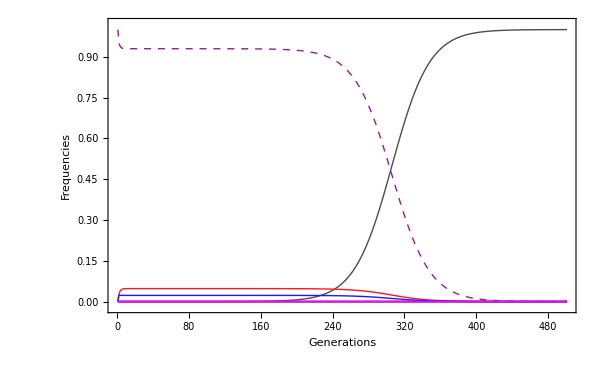

```mathematica
meannCA=0.1;
meannAB=0.0000001;

sA=-0.999;
hA=0.0;
sB=-0.5;
hB=0.0;
mu=0;
gens=500;
p0={0,0,0,0,0,1,0,0,0,0};
ps=Simulate[p0,gens,meannCA,meannAB,"CentralFusion",mu,mu,sA,hA,sB,hB];
PlotDynamics[ps]
```

Figure for paper:

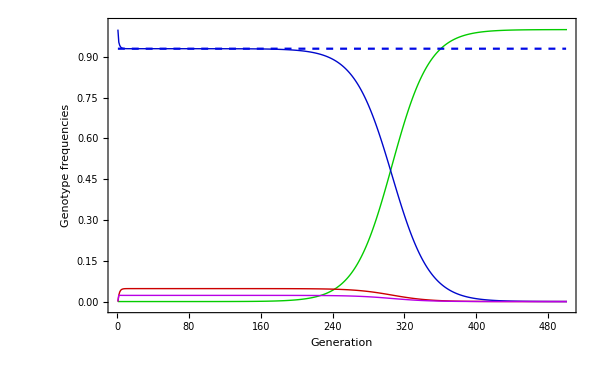

```mathematica
γ=1/3(1-ⅇ^(-3 meannCA/2));
saa=-sB;
sAA=-sA;
approxLine=Table[(2 (saa-γ) (sAA-γ))/(2 saa sAA-(saa+sAA) γ),{gens}];
ListLinePlot[Join[Transpose[ps⟦All,{1,3,6,8}⟧],{approxLine}],PlotRange->{-0.02,1.02},Frame->True,ImageSize->600,FrameStyle->18,PlotStyle->{Directive[Thick, Hue[0.33,1,0.8]],Directive[Thick, Hue[0,1,0.8]],Directive[Thick,Hue[0.66,1,0.8]],Directive[Thick, Hue[0.8,1,0.9]],Directive[Dashed, Hue[0.66,1,0.9]]}, FrameLabel->{Style["Generation",26],Style["Genotype frequencies",26]},ImageSize->400(*,AspectRatio->1*)]
```

Formula for approximation in paper:

```mathematica
Simplify[(2 (saa-γ) (sAA-γ))/(2 saa sAA-(saa+sAA) γ)==(2 (1+3sB-ⅇ^(-3 meannCA/2)) (1+3sA-ⅇ^(-3 meannCA/2)))/(18 sB sA+3(sB+sA)(1-ⅇ^(-3 meannCA/2)))]
```

True

#### Screen of parameter space

```mathematica
meannCAvalues=10^Range[-5,0,0.2];
meannABvalues=10^Range[-5,0,0.2];
sA=-0.99;
hA=0.001;
sB=-0.99;
hB=0.001;
mu=0;
p0={0,0,0,0,0,1,0,0,0,0};
pThresh=0.01;
```

```mathematica
gens=10000;
resultsCF={{"Log(nCA)","Log(nAB)","Log(gens)"}};
Do[
meannCA=meannCAvalues⟦i⟧;
meannAB=meannABvalues⟦j⟧;
ps=Simulate[p0,gens,meannCA,meannAB,"CentralFusion",mu,mu,sA,hA,sB,hB];
firstgen=Position[ps⟦All,6⟧,g_/;g<pThresh,1,1];
If[firstgen=={},firstgen=gens];
AppendTo[resultsCF,Flatten[{Log10[meannCA],Log10[meannAB],N[Log10[firstgen]]}]];
,
{i,1,Length[meannCAvalues]},{j,1,Length[meannABvalues]}
];
```

```mathematica
gens=1000;
resultsTF={{"Log(nCA)","Log(nAB)","Log(gens)"}};
Do[
meannCA=meannCAvalues⟦i⟧;
meannAB=meannABvalues⟦j⟧;
ps=Simulate[p0,gens,meannCA,meannAB,"TerminalFusion",mu,mu,sA,hA,sB,hB];
firstgen=Position[ps⟦All,6⟧,g_/;g<pThresh,1,1];
If[firstgen==Missing["NotFound"],firstgen=gens];
AppendTo[resultsTF,Flatten[{Log10[meannCA],Log10[meannAB],N[Log10[firstgen]]}]];
,
{i,1,Length[meannCAvalues]},{j,1,Length[meannABvalues]}
];
```

```mathematica
gens=1000;
resultsSex={{"Log(nCA)","Log(nAB)","Log(gens)"}};
Do[
meannCA=meannCAvalues⟦i⟧;
meannAB=meannABvalues⟦j⟧;
ps=Simulate[p0,gens,meannCA,meannAB,"Sex",mu,mu,sA,hA,sB,hB];
firstgen=Position[ps⟦All,6⟧,g_/;g<pThresh,1,1];
If[firstgen==Missing["NotFound"],firstgen=gens];
AppendTo[resultsSex,Flatten[{Log10[meannCA],Log10[meannAB],N[Log10[firstgen]]}]];
,
{i,1,Length[meannCAvalues]},{j,1,Length[meannABvalues]}
];
```

```mathematica
max=4;
min=1;
ColourFunction[x_]:=Hue[0.66,(x-min)/(max-min),1];
nTickMarks={{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
plotCF=ListDensityPlot[resultsCF⟦2;;Length[resultsCF⟦All,1⟧]⟧, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(ColourFunction[#]&),ColorFunctionScaling->False,FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameStyle->18,FrameLabel->{{Style["m̄",26],None},{Style["n̄",26],Style["Central Fusion",26]}},ImageSize->400];
plotTF=ListDensityPlot[resultsTF⟦2;;Length[resultsTF⟦All,1⟧]⟧, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(ColourFunction[#]&),ColorFunctionScaling->False,FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameStyle->18,FrameLabel->{{Style[" ",26],None},{Style["n̄",26],Style["Terminal Fusion",26]}},ImageSize->400];
plotSex=ListDensityPlot[resultsSex⟦2;;Length[resultsSex⟦All,1⟧]⟧, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(ColourFunction[#]&),ColorFunctionScaling->False,FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameStyle->18,FrameLabel->{{Style[" ",26],None},{Style["n̄",26],Style["Sex",26]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,{{0,"1"},{1,"10"},{2,"100"},{3,"10^3"},{4,"10^4"}}},{None,None}},ColorFunctionScaling->False,ColorFunction->(ColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{55,300},FrameStyle->18];
GraphicsGrid[{{plotCF,plotTF,plotSex,legend}},Alignment->Left]
```

```mathematica
max=4;
min=1;
ColourFunction[x_]:=Hue[0.66,(x-min)/(max-min),1];
nTickMarks={{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
plotCF=ListDensityPlot[resultsCF⟦2;;Length[resultsCF⟦All,1⟧]⟧, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(ColourFunction[#]&),ColorFunctionScaling->False,FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameStyle->18,FrameLabel->{{Style["m̄",26],None},{Style["n̄",26],Style["Central Fusion",26]}},ImageSize->400];
plotTF=ListDensityPlot[resultsTF⟦2;;Length[resultsTF⟦All,1⟧]⟧, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(ColourFunction[#]&),ColorFunctionScaling->False,FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameStyle->18,FrameLabel->{{Style[" ",26],None},{Style["n̄",26],Style["Terminal Fusion",26]}},ImageSize->400];
plotSex=ListDensityPlot[resultsSex⟦2;;32⟧, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(ColourFunction[#]&),ColorFunctionScaling->False,FrameTicks->{{nTickMarks,None},{{{-5," "}},None}},FrameStyle->18,FrameLabel->{{Style[" ",26],None},{Style[" ",26],Style["Sex",26]}},ImageSize->135.2,AspectRatio->5];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,{{0,"1"},{1,"10"},{2,"100"},{3,"10^3"},{4,"10^4"}}},{None,None}},ColorFunctionScaling->False,ColorFunction->(ColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{55,300},FrameStyle->18];
GraphicsGrid[{{plotCF,plotTF,plotSex,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci

```mathematica
mu=0.00001;
maxgens=1000000;
recValues=Range[0,0.02,0.001];
sA=0.1;
sB=0.1;
hA=0.05;
hB=0.05;
reps=1;
wThresh=1+0.99(sA+sB+sA sB);
results={{"RepMode","recCA","recAB","sA","hA","sB","hB","mu","N","Rep","gens"}};
SetDirectory["/Users/jan/documents/projects/recent/RecAutomixis"];
Get["AutomixisMatrices.dat"];
Get["SexTensors.dat"];
filename="expSpeedAdapt 3.tsv";
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=convertMToCOs[recValues⟦irecCA⟧];
meannAB=convertMToCOs[recValues⟦irecAB⟧];
(*AutomixisMatrix=N[getAutomixisMatrix[meannCA,meannAB,"CentralFusion"]];*)   (* old version, in which this matrix is calculated *)
AutomixisMatrix=Select[AutomixisMatrices,#⟦1;;3⟧=={"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧}&]⟦1,4⟧;(* new version in which the matrix is loaded from pre-calculated file *)

p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=Recursion[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧,sA,hA,sB,hB,mu,"Inf",rep,g}];
,{irecCA,Length[recValues]},{irecAB,Length[recValues]}
];

(* same simulations with sexual reproduction; here recCA is not screened because it is irrelevant *)
Do[
meannAB=convertMToCOs[recValues⟦irecAB⟧];
SexTensor=Select[SexTensors,(#⟦1⟧==recValues⟦irecAB⟧)&]⟦1,2⟧;
(*SexTensor=N[getSexTensor[0,meannAB]];*)

p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexual[p,SexTensor,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",0,recValues⟦irecAB⟧,sA,hA,sB,hB,mu,"Inf",rep,g}];

,{irecAB,Length[recValues]}
];
Export[filename,results];
ClearMemory;
,{rep,reps}];
```

```mathematica
SetDirectory["/Users/jan/documents/projects/recent/RecAutomixis"];
results=Import[filename];
```

```mathematica
TableForm[results]
```

```mathematica
meanAutomixisGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",Round[recValues⟦irecCA⟧,0.00001],Round[recValues⟦irecAB⟧,0.00001]}&]⟦All,11⟧]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
meanSexGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[recValues⟦irecAB⟧,0.00001]}&]⟦All,11⟧]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
meanRelativeGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
N[Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",Round[recValues⟦irecCA⟧,0.00001],Round[recValues⟦irecAB⟧,0.00001]}&]⟦All,11⟧]/Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[recValues⟦irecAB⟧,0.00001]}&]⟦All,11⟧]]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
```

```mathematica
N[meanRelativeGens]//TableForm
```

```mathematica
max=2;
min=1/8;
RedBlueColourFunction[x_]:=If[x>1,Hue[0,Log[2,x]/Log[2,max],1],Hue[0.7,Log[2,x]/Log[2,min],1]];
plot=ListDensityPlot[meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->20,FrameLabel->{Style["r_CA",26],Style["r_AB",26]},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,All},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{55,300},FrameStyle->20];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci: h=0.01

```mathematica
mu=0.00001;
maxgens=1000000;
meannCAValues=10^Range[-5,0,0.2];
meannABValues=10^Range[-5,0,0.2];
sA=0.1;
sB=0.1;
hA=0.01;
hB=0.01;
wThresh=1+0.99(sA+sB+sA sB);
NN=Infinity;
results={{"RepMode","Log(nCA)","Log(nAB)","sA","hA","sB","hB","mu","N","Rep","gens"}};
```

```mathematica
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=Recursion[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,1,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexual[p,SexTensor,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,1,g}];
,{imeannAB,Length[meannABValues]}
];
```

```mathematica
LogmeannCAValues=Round[Log10[meannCAValues],0.1];
LogmeannABValues=Round[Log10[meannABValues],0.1];
meanAutomixisGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
meanSexGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
Log2meanRelativeGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
N[Log2[Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",Round[LogmeannCAValues⟦inCA⟧,0.0000000001],Round[LogmeannABValues⟦inAB⟧,0.0000000001]}&]⟦All,11⟧]/Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[LogmeannABValues⟦inAB⟧,0.0000000001]}&]⟦All,11⟧]]]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
```

```mathematica
max=3.5;
min=-3.5;
nTickMarks={{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
RedBlueColourFunction[x_]:=If[x>0,Hue[0,x/max,1],Hue[0.7,x/min,1]];
plot=ListDensityPlot[Log2meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->Directive[Black,18],FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameLabel->{{Style["m̄",26],None},{Style["n̄",26,Black],Style["Recessive, no drift",26,Black]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,Table[{i,N[2^i]},{i,-4,4}]},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{75,300},FrameStyle->18];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci: h=0.5

```mathematica
mu=0.00001;
maxgens=1000000;
meannCAValues=10^Range[-5,0,0.2];
meannABValues=10^Range[-5,0,0.2];
sA=0.1;
sB=0.1;
hA=0.5;
hB=0.5;
wThresh=1+0.99(sA+sB+sA sB);
NN=Infinity;
results={{"RepMode","Log(nCA)","Log(nAB)","sA","hA","sB","hB","mu","N","Rep","gens"}};
```

```mathematica
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=Recursion[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,1,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexual[p,SexTensor,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,1,g}];
,{imeannAB,Length[meannABValues]}
];
```

```mathematica
TableForm[results]
```

```mathematica
LogmeannCAValues=Round[Log10[meannCAValues],0.1];
LogmeannABValues=Round[Log10[meannABValues],0.1];
meanAutomixisGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
meanSexGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
Log2meanRelativeGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
N[Log2[Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",Round[LogmeannCAValues⟦inCA⟧,0.0000000001],Round[LogmeannABValues⟦inAB⟧,0.0000000001]}&]⟦All,11⟧]/Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[LogmeannABValues⟦inAB⟧,0.0000000001]}&]⟦All,11⟧]]]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
```

```mathematica
Max[Log2meanRelativeGens⟦All,3⟧]
Min[Log2meanRelativeGens⟦All,3⟧]
```

-0.0696055

-0.899071

```mathematica
max=3.5(*Log2[16]*);
min=-3.5(*Log2[1/16]*);
nTickMarks={{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
RedBlueColourFunction[x_]:=If[x>0,Hue[0,x/max,1],Hue[0.7,x/min,1]];
plot=ListDensityPlot[Log2meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->Directive[Black,18],FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameLabel->{{Style["m̄",26],None},{Style["n̄",26,Black],Style["Additive, no drift",26,Black]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,Table[{i,N[2^i]},{i,-4,4}]},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{75,300},FrameStyle->18];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci: h=0.99

```mathematica
mu=0.00001;
maxgens=1000000;
meannCAValues=10^Range[-5,0,0.2];
meannABValues=10^Range[-5,0,0.2];
sA=0.1;
sB=0.1;
hA=0.99;
hB=0.99;
wThresh=1+0.99(sA+sB+sA sB);
NN=Infinity;
results={{"RepMode","Log(nCA)","Log(nAB)","sA","hA","sB","hB","mu","N","Rep","gens"}};
```

```mathematica
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=Recursion[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,1,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexual[p,SexTensor,mu,mu,sA,hA,sB,hB];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,1,g}];
,{imeannAB,Length[meannABValues]}
];
```

```mathematica
LogmeannCAValues=Round[Log10[meannCAValues],0.1];
LogmeannABValues=Round[Log10[meannABValues],0.1];
meanAutomixisGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
meanSexGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
Log2meanRelativeGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
N[Log2[Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",Round[LogmeannCAValues⟦inCA⟧,0.0000000001],Round[LogmeannABValues⟦inAB⟧,0.0000000001]}&]⟦All,11⟧]/Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[LogmeannABValues⟦inAB⟧,0.0000000001]}&]⟦All,11⟧]]]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
```

```mathematica
Max[Log2meanRelativeGens⟦All,3⟧]
Min[Log2meanRelativeGens⟦All,3⟧]
```

-0.0696055

-0.899071

```mathematica
max=3.5(*Log2[16]*);
min=-3.5(*Log2[1/16]*);
nTickMarks={{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
RedBlueColourFunction[x_]:=If[x>0,Hue[0,x/max,1],Hue[0.7,x/min,1]];
plot=ListDensityPlot[Log2meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->Directive[Black,18],FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameLabel->{{Style["m̄",26],None},{Style["n̄",26,Black],Style["Dominant, no drift",26,Black]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,Table[{i,N[2^i]},{i,-4,4}]},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{75,300},FrameStyle->18];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

## Two-locus model with finite population size

### Plotting the evolutionary dynamics

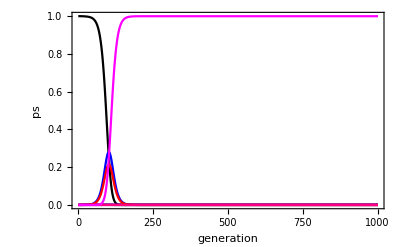

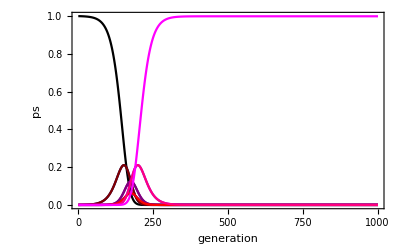

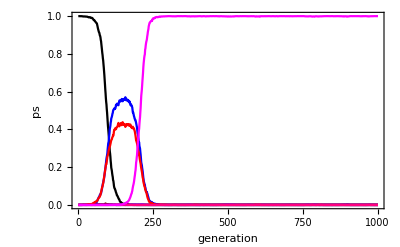

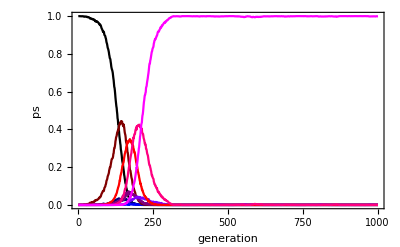

```mathematica
sA=0.1;
sB=0.1;
hA=0.5;
hB=0.5;
muA=0.00001;
muB=0.00001;
meannCA=0.1;
meannAB=0.1;
gens=1000;
NN=10000;
p0={1,0,0,0,0,0,0,0,0,0};
ps=Simulate[p0,gens,meannCA,meannAB,"CentralFusion",muA,muB,sA,hA,sB,hB];
ListLinePlot[Transpose[ps],PlotRange->{0,1},Frame->True,PlotStyle->genotypeColours,FrameStyle->16,ImageSize->400,FrameLabel->{Style["generation",20],Style["ps",20]}]
ps=Simulate[p0,gens,meannCA,meannAB,"Sex",muA,muB,sA,hA,sB,hB];
ListLinePlot[Transpose[ps],PlotRange->{0,1},Frame->True,PlotStyle->genotypeColours,FrameStyle->16,ImageSize->400,FrameLabel->{Style["generation",20],Style["ps",20]}]
ps=SimulateFiniteN[p0,gens,meannCA,meannAB,"CentralFusion",muA,muB,sA,hA,sB,hB,NN];
ListLinePlot[Transpose[ps],PlotRange->{0,1},Frame->True,PlotStyle->genotypeColours,FrameStyle->16,ImageSize->400,FrameLabel->{Style["generation",20],Style["ps",20]}]
ps=SimulateFiniteN[p0,gens,meannCA,meannAB,"Sex",muA,muB,sA,hA,sB,hB,NN];
ListLinePlot[Transpose[ps],PlotRange->{0,1},Frame->True,PlotStyle->genotypeColours,FrameStyle->16,ImageSize->400,FrameLabel->{Style["generation",20],Style["ps",20]}]
```

### Speed of adapatation at two linked loci

```mathematica
mu=0.00001;
maxgens=1000000;
recValues=Round[10^Range[-5,-1,0.25],0.0000000001];
sA=0.1;
sB=0.1;
hA=0.5;
hB=0.5;
NN=10000;
reps=1000;
wThresh=1+0.99(sA+sB+sA sB);
results={{"RepMode","recCA","recAB","sA","hA","sB","hB","mu","N","Rep","gens"}};
SetDirectory["/Users/jan/documents/projects/recent/RecAutomixis"];
Get["AutomixisMatrices.dat"];
Get["SexTensors.dat"];
filename="expSpeedAdapt 8";
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=convertMToCOs[recValues⟦irecCA⟧];
meannAB=convertMToCOs[recValues⟦irecAB⟧];
(*AutomixisMatrix=N[getAutomixisMatrix[meannCA,meannAB,"CentralFusion"]];*)   (* old version, in which this matrix is calculated *)
AutomixisMatrix=Select[AutomixisMatrices,#⟦1;;3⟧=={"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧}&]⟦1,4⟧;(* new version in which the matrix is loaded from pre-calculated file *)

p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionFiniteN[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧,sA,hA,sB,hB,mu,NN,rep,g}];
,{irecCA,Length[recValues]},{irecAB,Length[recValues]}
];

(* same simulations with sexual reproduction; here recCA is not screened because it is irrelevant *)
Do[
meannAB=convertMToCOs[recValues⟦irecAB⟧];
SexTensor=Select[SexTensors,(#⟦1⟧==recValues⟦irecAB⟧)&]⟦1,2⟧;
(*SexTensor=N[getSexTensor[0,meannAB]];*)

p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexualFiniteN[p,SexTensor,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",0,recValues⟦irecAB⟧,sA,hA,sB,hB,mu,NN,rep,g}];

,{irecAB,Length[recValues]}
];
Export[StringJoin[filename," ", ToString[rep],".tsv"],results];
ClearMemory;
,{rep,1,reps}];
```

```mathematica
SetDirectory["/Users/jan/documents/projects/recent/RecAutomixis/Exploration results"];
results=Import["expSpeedAdapt 6.tsv"];
```

```mathematica
meanAutomixisGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧}&]⟦All,11⟧]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
```

```mathematica
meanAutomixisGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",recValues⟦irecCA⟧,recValues⟦irecAB⟧}&]⟦All,11⟧]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
meanSexGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[recValues⟦irecAB⟧,0.0000000001]}&]⟦All,11⟧]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
```

```mathematica
meanRelativeGens=Flatten[Table[{recValues⟦irecCA⟧,recValues⟦irecAB⟧,
N[Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",Round[recValues⟦irecCA⟧,0.0000000001],Round[recValues⟦irecAB⟧,0.0000000001]}&]⟦All,11⟧]/Mean[Select[results,#⟦{1,3}⟧=={"Sex",Round[recValues⟦irecAB⟧,0.0000000001]}&]⟦All,11⟧]]},
{irecCA,1,Length[recValues]},{irecAB,1,Length[recValues]}],1];
```

```mathematica
max=2;
min=1/8;
RedBlueColourFunction[x_]:=If[x>1,Hue[0,Log[2,x]/Log[2,max],1],Hue[0.7,Log[2,x]/Log[2,min],1]];
plot=ListDensityPlot[meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->20,FrameLabel->{Style["r_CA",26],Style["r_AB",26]},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,All},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{55,300},FrameStyle->20];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci - Improved screening with h=0.01

```mathematica
mu=0.00001;
maxgens=1000000;
meannCAValues=10^Range[-5,0,0.2];
meannABValues=10^Range[-5,0,0.2];
sA=0.1;
sB=0.1;
hA=0.01;
hB=0.01;
NN=10000;
reps=1000;
wThresh=1+0.99(sA+sB+sA sB);
results={{"RepMode","Log(nCA)","Log(nAB)","sA","hA","sB","hB","mu","N","Rep","gens"}};
SetDirectory["/Users/janengelstaedter/dropbox/projects/RecAutomixis"];
filename="expSpeedAdapt 9";
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionFiniteN[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexualFiniteN[p,SexTensor,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA]],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannAB,Length[meannABValues]}
];

If[Mod[rep,10]==0,Export[StringJoin[filename," Rep", ToString[rep],".tsv"],results]];
ClearMemory;
,{rep,801,1000}];
```

```mathematica
SetDirectory["/Users/janengelstaedter/dropbox/projects/RecAutomixis/Exploration Results"];
```

```mathematica
results=Import["expSpeedAdapt 9 Means.tsv"];
```

```mathematica
TableForm[results⟦1;;50⟧]
```

```mathematica
LogmeannCAValues=Round[Log10[meannCAValues],0.1];
LogmeannABValues=Round[Log10[meannABValues],0.1];
meanAutomixisGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
meanSexGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
Log2meanRelativeGens=Transpose[{meanAutomixisGens⟦All,1⟧,meanAutomixisGens⟦All,2⟧,Log2[meanAutomixisGens⟦All,3⟧/meanSexGens⟦All,3⟧]}];
```

```mathematica
max=3.5;
min=-3.5;
nTickMarks={{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
RedBlueColourFunction[x_]:=If[x>0,Hue[0,x/max,1],Hue[0.7,x/min,1]];
plot=ListDensityPlot[Log2meanRelativeGens2, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->Directive[Black,18],FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameLabel->{{Style["m̄",26],None},{Style["n̄",26,Black],Style["Recessive, with drift",26,Black]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,Table[{i,N[2^i]},{i,-4,4}]},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{75,300},FrameStyle->18];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci - Improved screening with h=0.5

```mathematica
mu=0.00001;
maxgens=1000000;
meannCAValues=10^Range[-5,0,0.2];
meannABValues=10^Range[-5,0,0.2];
sA=0.1;
sB=0.1;
hA=0.5;
hB=0.5;
NN=10000;
reps=1000;
wThresh=1+0.99(sA+sB+sA sB);
results={{"RepMode","Log(nCA)","Log(nAB)","sA","hA","sB","hB","mu","N","Rep","gens"}};
SetDirectory["/Users/janengelstaedter/dropbox/projects/RecAutomixis"];
filename="expSpeedAdapt 10";
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionFiniteN[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexualFiniteN[p,SexTensor,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA]],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannAB,Length[meannABValues]}
];

If[Mod[rep,10]==0,Export[StringJoin[filename," Rep", ToString[rep],".tsv"],results]];
ClearMemory;
,{rep,1,1000}];
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionFiniteN[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexualFiniteN[p,SexTensor,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA]],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannAB,Length[meannABValues]}
];

If[Mod[rep,10]==0,Export[StringJoin[filename," Rep", ToString[rep],".tsv"],results]];
ClearMemory;
,{rep,500,1000}];
```

```mathematica
SetDirectory["/Users/janengelstaedter/dropbox/projects/RecAutomixis/Exploration Results"];
```

```mathematica
results1=Import["expSpeedAdapt 10 Rep500.tsv"];
results2=Import["expSpeedAdapt 10 Rep1000.tsv"];
results=Join[results1,Drop[results2,1]];
```

```mathematica
LogmeannCAValues=Round[Log10[meannCAValues],0.1];
LogmeannABValues=Round[Log10[meannABValues],0.1];
meanAutomixisGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
meanSexGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
Mean[Select[results,#⟦{1,3}⟧=={"Sex",LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
Log2meanRelativeGens=Transpose[{meanAutomixisGens⟦All,1⟧,meanAutomixisGens⟦All,2⟧,Log2[meanAutomixisGens⟦All,3⟧/meanSexGens⟦All,3⟧]}];
```

```mathematica
max=3.5;
min=-3.5;
nTickMarks={{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"0.01"},{-1,"0.1"},{0,"1"}};
RedBlueColourFunction[x_]:=If[x>0,Hue[0,x/max,1],Hue[0.7,x/min,1]];
plot=ListDensityPlot[Log2meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->Directive[Black,18],FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameLabel->{{Style["m̄",26],None},{Style["n̄",26,Black],Style["Additive, with drift",26,Black]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,Table[{i,N[2^i]},{i,-4,4}]},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{75,300},FrameStyle->18];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

### Speed of adapatation at two linked loci - Additional, very coarse but broader screening with h=0.5

```mathematica
mu=0.00001;
maxgens=1000000;
meannCAValues=Join[{0},10^Range[-8,0,2]];
meannABValues=Join[{0},10^Range[-8,0,2]];
sA=0.1;
sB=0.1;
hA=0.5;
hB=0.5;
NN=10000;
reps=1000;
wThresh=1+0.99(sA+sB+sA sB);
results={{"RepMode","Log(nCA)","Log(nAB)","sA","hA","sB","hB","mu","N","Rep","gens"}};
SetDirectory["/Users/janengelstaedter/dropbox/projects/RecAutomixis"];
filename="expSpeedAdapt 11";
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionFiniteN[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexualFiniteN[p,SexTensor,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA]],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannAB,Length[meannABValues]}
];

If[Mod[rep,10]==0,Export[StringJoin[filename," Rep", ToString[rep],".tsv"],results]];
ClearMemory;
,{rep,1,500}];
```

```mathematica
Do[
(* run simulations with automixis: *)
Do[
meannCA=meannCAValues⟦imeannCA⟧;
meannAB=meannABValues⟦imeannAB⟧;
AutomixisMatrix=N[getAutomixisMatrixPoisson[meannCA,meannAB,"CentralFusion"]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionFiniteN[p,AutomixisMatrix,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"CentralFusion",Round[Log10[meannCA],0.1],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannCA,Length[meannCAValues]},{imeannAB,Length[meannABValues]}
];

(* run simulations with sex: *)
Do[
meannAB=meannABValues⟦imeannAB⟧;
SexTensor=N[getSexTensor[meannCA,meannAB]];
p={1,0,0,0,0,0,0,0,0,0};
g=1;
meanw=1;
While[(meanw<wThresh) &&( g<maxgens),
p=RecursionSexualFiniteN[p,SexTensor,mu,mu,sA,hA,sB,hB,NN];
g=g+1;
meanw=getMeanFitness[p,sA,hA,sB,hB];
];
results=Append[results,{"Sex",Round[Log10[meannCA]],Round[Log10[meannAB],0.1],sA,hA,sB,hB,mu,NN,rep,g}];
,{imeannAB,Length[meannABValues]}
];

If[Mod[rep,10]==0,Export[StringJoin[filename," Rep", ToString[rep],".tsv"],results]];
ClearMemory;
,{rep,500,1000}];
```

```mathematica
SetDirectory["/Users/janengelstaedter/dropbox/projects/RecAutomixis/Exploration Results"];
```

```mathematica
results1=Import["expSpeedAdapt 11 Rep500.tsv"];
results2=Import["expSpeedAdapt 11 Rep1000.tsv"];
results=Join[results1,Drop[results2,1]];
```

```mathematica
results=results/.{"-Infinity"->-∞};
LogmeannCAValues=Round[Log10[meannCAValues],0.1];
LogmeannABValues=Round[Log10[meannABValues],0.1];
meanAutomixisGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
N[Mean[Select[results,#⟦1;;3⟧=={"CentralFusion",LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
meanSexGens=Flatten[Table[{LogmeannCAValues⟦inCA⟧,LogmeannABValues⟦inAB⟧,
N[Mean[Select[results,#⟦{1,3}⟧=={"Sex",LogmeannABValues⟦inAB⟧}&]⟦All,11⟧]]},
{inCA,1,Length[LogmeannCAValues]},{inAB,1,Length[LogmeannABValues]}],1];
Log2meanRelativeGens=Transpose[{meanAutomixisGens⟦All,1⟧,meanAutomixisGens⟦All,2⟧,Log2[meanAutomixisGens⟦All,3⟧/meanSexGens⟦All,3⟧]}];
```

```mathematica
meanAutomixisGens
meanSexGens
Log2meanRelativeGens
```

{{-∞,-∞,778.284},{-∞,-8.,788.207},{-∞,-6.,782.512},{-∞,-4.,711.351},{-∞,-2.,624.253},{-∞,0.,604.737},{-8.,-∞,787.075},{-8.,-8.,783.413},{-8.,-6.,771.859},{-8.,-4.,709.876},{-8.,-2.,632.388},{-8.,0.,592.262},{-6.,-∞,772.514},{-6.,-8.,772.168},{-6.,-6.,767.793},{-6.,-4.,700.388},{-6.,-2.,623.764},{-6.,0.,600.992},{-4.,-∞,577.841},{-4.,-8.,576.778},{-4.,-6.,566.941},{-4.,-4.,557.464},{-4.,-2.,521.511},{-4.,0.,493.562},{-2.,-∞,349.721},{-2.,-8.,348.44},{-2.,-6.,345.019},{-2.,-4.,347.784},{-2.,-2.,334.029},{-2.,0.,320.193},{0.,-∞,279.341},{0.,-8.,279.05},{0.,-6.,276.237},{0.,-4.,276.556},{0.,-2.,283.369},{0.,0.,277.047}}

{{-∞,-∞,443.205},{-∞,-8.,445.23},{-∞,-6.,446.54},{-∞,-4.,428.981},{-∞,-2.,356.873},{-∞,0.,332.32},{-8.,-∞,443.205},{-8.,-8.,445.23},{-8.,-6.,446.54},{-8.,-4.,428.981},{-8.,-2.,356.873},{-8.,0.,332.32},{-6.,-∞,443.205},{-6.,-8.,445.23},{-6.,-6.,446.54},{-6.,-4.,428.981},{-6.,-2.,356.873},{-6.,0.,332.32},{-4.,-∞,443.205},{-4.,-8.,445.23},{-4.,-6.,446.54},{-4.,-4.,428.981},{-4.,-2.,356.873},{-4.,0.,332.32},{-2.,-∞,443.205},{-2.,-8.,445.23},{-2.,-6.,446.54},{-2.,-4.,428.981},{-2.,-2.,356.873},{-2.,0.,332.32},{0.,-∞,443.205},{0.,-8.,445.23},{0.,-6.,446.54},{0.,-4.,428.981},{0.,-2.,356.873},{0.,0.,332.32}}

{{-10,-10,0.812323},{-10,-8.,0.824024},{-10,-6.,0.809323},{-10,-4.,0.729647},{-10,-2.,0.806719},{-10,0.,0.863737},{-8.,-10,0.828527},{-8.,-8.,0.815222},{-8.,-6.,0.789547},{-8.,-4.,0.726653},{-8.,-2.,0.825398},{-8.,0.,0.833663},{-6.,-10,0.801588},{-6.,-8.,0.794364},{-6.,-6.,0.781927},{-6.,-4.,0.70724},{-6.,-2.,0.80559},{-6.,0.,0.854774},{-4.,-10,0.382699},{-4.,-8.,0.373467},{-4.,-6.,0.344408},{-4.,-4.,0.377964},{-4.,-2.,0.547288},{-4.,0.,0.570661},{-2.,-10,-0.341768},{-2.,-8.,-0.353642},{-2.,-6.,-0.372115},{-2.,-4.,-0.302721},{-2.,-2.,-0.095438},{-2.,0.,-0.0536308},{0.,-10,-0.665948},{0.,-8.,-0.674027},{0.,-6.,-0.692886},{0.,-4.,-0.63334},{0.,-2.,-0.332731},{0.,0.,-0.262441}}

```mathematica
max=3.5(*Log2[16]*);
min=-3.5(*Log2[1/16]*);
Log2meanRelativeGens=Log2meanRelativeGens/.{-∞->-10}; (* so it can be plotted*)
nTickMarks={{-10,"0"},{-8,"10^-8"},{-6,"10^-6"},{-4,"10^-4"},{-2,"0.01"},{0,"1"}};
RedBlueColourFunction[x_]:=If[x>0,Hue[0,x/max,1],Hue[0.7,x/min,1]];
plot=ListDensityPlot[Log2meanRelativeGens, InterpolationOrder->0,PlotRange->{min,max},ColorFunction->(RedBlueColourFunction[#]&),ColorFunctionScaling->False,FrameStyle->Directive[Black,18],FrameTicks->{{nTickMarks,None},{nTickMarks,None}},FrameLabel->{{Style["m̄",26],None},{Style["n̄",26,Black],Style["Additive, with drift",26,Black]}},ImageSize->400];
legend=ContourPlot[y,{x,0,1},{y,min,max},FrameTicks->{{None,Table[{i,N[2^i]},{i,-4,4}]},{None,None}},ColorFunctionScaling->False,ColorFunction->(RedBlueColourFunction[#]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{75,300},FrameStyle->18];
GraphicsGrid[{{plot,legend}},Alignment->Left]
```

## Competition between two different subpopulations

### Overdominance

With central fusion, reduced numbers of COs are favoured:

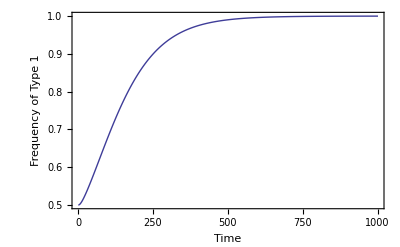

```mathematica
p0={0,0.5,0,0,0,0,0,0,0,0};
q0={0,0.5,0,0,0,0,0,0,0,0};
s=0.1;
h=1.5;
mu=0;
meann1=0.01;
meann2=0.02;
gens=1000;
pq=SimulateCompetition[p0,q0,gens,meann1,meann1,meann2,meann2,"CentralFusion","CentralFusion",mu,mu,s,h,s,h];
ListLinePlot[Total[pq,{3}][[1]],Frame->True,FrameLabel->{{"Frequency of Type 1",None},{"Time",None}}]
```

### Mutation-selection balance

With central fusion, increased numbers of COs are favoured (but only weakly so):

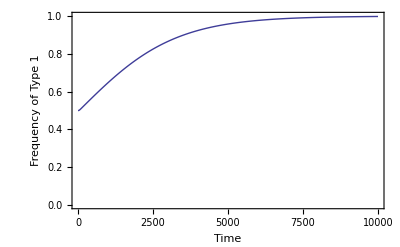

```mathematica
p0={0.5,0,0,0,0,0,0,0,0,0};
q0={0.5,0,0,0,0,0,0,0,0,0};
s=-0.1;
h=0.5;
mu=0.001;
meannCA1=0.2;
meannCA2=0.0;
gens=10000;
pq=SimulateCompetition[p0,q0,gens,meannCA1,0,meannCA2,0,"CentralFusion","CentralFusion",mu,0,s,h,0,0];
ListLinePlot[Total[pq,{3}][[1]],PlotRange->{0,1},Frame->True,FrameLabel->{{"Frequency of Type 1",None},{"Time",None}}]
```